# 7+1: the octonions and the Clifford algebra of 7+1 spacetime

## A real realization of the octonions and a real 16×16 realization of the Clifford algebra, built from — and mirroring — the split octonions and the 16×16 Dirac matrices of 4+4.nb

Prepared for Nash's 7+1 project (github.com/once-ere/7+1). Wolfram Language 15.0.1. This notebook was generated by tools/make_7p1_nb.py and evaluated in Wolfram 15.0.1; every claim in it is checked by a cell of the form check["name", test].

Summary. Starting from the real 8×8 matrices τ[A] and the real 16×16 Dirac matrices T16[A] of 4+4.nb (split octonions and the Clifford algebra Cl(4,4)), this notebook constructs: (i) a real realization of the octonions, τO[A] = τ[A] for A ≤ 3 and τO[A] = τ[A].σ for A ≥ 4, whose multiplication table is produced by exactly the same vielbein formula as the split-octonion table of 4+4.nb; (ii) the Clifford algebra of 7+1 spacetime (x0 = time = the octonion unit, x1 … x7 = space) as REAL 16×16 matrices Γ17[A] built from T16; this is possible because the octonions’ own quadratic form Re(x x) = x0.b2 − x1.b2 − … − x7.b2 has signature (1,7) and Cl(1,7) ≅ ℝ(16); (iii) a proof that with the opposite overall sign (the sign convention of 4+4.nb, metric η71) no real 16×16 realization exists, because Cl(7,1) ≅ ℍ(8); for that convention the notebook gives the minimal complexification Γ71 (the exact block form of T16 with a single factor i) and a real 32×32 realization; (iv) examples: Fano plane, Moufang identities, the eight-square identity, Cayley–Dickson doubling, so(1,7), a boost and a rotation, the 7+1 Dirac operator, real on-shell spinor amplitudes, real massless and massive spinor fields, and the classification of all nine signatures p+q = 8. All checks are collected in the last section.

## 0. How to use this notebook

Evaluate the whole notebook in order (Evaluation ▸ Evaluate Notebook). Each verification is a cell check["name", test]; it prints name → True and stores the result in the association checks. Section 6 lists all checks; allChecksPassed must be True.

The notebook has its own private context (CellContext → Notebook), so its symbols cannot collide with the symbols of 4+4.nb (which protects, for example, unit and hUSE) when both notebooks are open.

Index conventions: A, B, K, L run over 0 … 7 and label the coordinates x0 … x7, the octonion units e[0] … e[7] and the generators Γ17[0] … Γ17[7]; i, j run over the imaginary/space values 1 … 7. Mathematica lists are 1-based, hence the frequent [[A+1, B+1]]. The letters C, D, E, I, N, O are built-in Wolfram symbols and are never used as variables here.

```mathematica
{$Version, $Context}
```

{15.0.1 for Microsoft Windows (64-bit) (July 2, 2026),Notebook$$38$50910`}

```mathematica
(* bookkeeping for all verifications in this notebook *)
checks = <||>;
check[name_String, test_] := Module[{r = TrueQ[test]}, AssociateTo[checks, name -> r]; name -> r];
```

## 1. Conventions, coordinates and notation

### 1.1 Coordinates X = {x0, …, x7}

4+4.nb and this notebook use the SAME eight coordinate symbols X = {x0, x1, x2, x3, x4, x5, x6, x7} (never x1, …, x8). Their physical meaning is different:

```mathematica
X = {x0, x1, x2, x3, x4, x5, x6, x7};
Grid[Prepend[{
   {"x0", "hidden space-like dimension", "ordinary time; octonion unit e[0] = 1"},
   {"x1, x2, x3", "ordinary 3-space", "ordinary 3-space; imaginary units e[1], e[2], e[3]"},
   {"x4", "ordinary time", "auxiliary space-like; e[4] = ℓ (Cayley-Dickson doubling unit)"},
   {"x5, x6, x7", "3 auxiliary time-like dimensions (superluminal deflating time)", "auxiliary space-like; e[5], e[6], e[7]"}},
  {"coordinate", "meaning in 4+4.nb (signature 4+4)", "meaning in 7+1.nb (signature 7+1)"}],
 Frame -> All, Alignment -> Left, Background -> {None, {LightGray}}]
```

coordinate | meaning in 4+4.nb (signature 4+4) | meaning in 7+1.nb (signature 7+1)
x0 | hidden space-like dimension | ordinary time; octonion unit e[0] = 1
x1, x2, x3 | ordinary 3-space | ordinary 3-space; imaginary units e[1], e[2], e[3]
x4 | ordinary time | auxiliary space-like; e[4] = ℓ (Cayley-Dickson doubling unit)
x5, x6, x7 | 3 auxiliary time-like dimensions (superluminal deflating time) | auxiliary space-like; e[5], e[6], e[7]

### 1.2 Metrics and sign conventions

4+4.nb uses the sign convention “space-like = +1, time-like = −1”: η4488 = diag(+1,+1,+1,+1,−1,−1,−1,−1) (x0 … x3 space-like, x4 … x7 time-like), and its Dirac matrices obey T16[A].T16[B] + T16[B].T16[A] = 2 η4488[[A+1,B+1]] ID16. In the same convention the 7+1 metric is η71 = diag(−1,+1,+1,+1,+1,+1,+1,+1).

We also use its negative, η17 = −η71 = diag(+1,−1,…,−1) (“mostly minus”). It is the quadratic form that the octonions themselves produce: for x = x0 e[0] + … + x7 e[7] the real part of x·x is x0.b2 − x1.b2 − … − x7.b2 = X.η17.X (section 4.7). The names tell which Clifford algebra each metric generates when v.b2 = Q(v): η71 has 7 plus signs and 1 minus sign, signature (7,1); η17 has 1 plus and 7 minus, signature (1,7). Both describe the same spacetime: one time, seven space dimensions.

gO = ID8 is the norm metric of the octonions (Euclidean, N(x) = x0.b2 + … + x7.b2); it replaces g_AB = η4488, the norm metric of the split octonions in 4+4.nb.

```mathematica
ID4 = IdentityMatrix[4]; ID8 = IdentityMatrix[8]; ID16 = IdentityMatrix[16]; ID32 = IdentityMatrix[32];
Zero4 = ConstantArray[0, {4, 4}]; Zero8 = ConstantArray[0, {8, 8}]; Zero16 = ConstantArray[0, {16, 16}];
zero8 = ConstantArray[0, 8];
η4488 = DiagonalMatrix[{1, 1, 1, 1, -1, -1, -1, -1}];  (* 4+4.nb, unchanged *)
η71 = DiagonalMatrix[{-1, 1, 1, 1, 1, 1, 1, 1}];       (* 7+1, sign convention of 4+4.nb *)
η17 = -η71;                                       (* 7+1, octonionic (mostly minus) convention *)
gO = ID8;                                                   (* octonion norm metric *)
Row[{"η4488 = ", MatrixForm[η4488], "   η71 = ", MatrixForm[η71], "   η17 = ", MatrixForm[η17], "   gO = ", MatrixForm[gO]}]
```

η4488 = (1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)   η71 = (-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)   η17 = (1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)   gO = (1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

### 1.3 Dictionary: names in 4+4.nb → names in this notebook

4+4.nb used the Notation package (Symbolize) to create 2-D symbols such as τ̄, T16^A, E^A_a and E^a_A. They are hard to read (T16^A[A1] looks like a power of T16) and easy to confuse with indices, so this notebook uses plain one-line names. Nothing else changes: every object of 4+4.nb that is used here is redefined below with exactly the formula of 4+4.nb.

```mathematica
Grid[Prepend[{
   {"σ (= σ88)", "σ", "8×8 split metric on spinor space, {{0, ID4}, {ID4, 0}}"},
   {"s4by4[h], t4by4[h], ζ[A]", "unchanged", "self-dual / anti-self-dual 4×4 blocks and the 8×8 ζ[A] built from them"},
   {"τ[A]", "τ[A]", "split-octonion 8×8 matrices, A = 0 … 7"},
   {"τ̄[A]   (Symbolize)", "τbar[A]", "σ.Transpose[τ[A]].σ"},
   {"T16^A[A1]   (Symbolize)", "T16[A]", "4+4 Dirac matrices {{0, τbar[A]}, {τ[A], 0}}; T16[8] = product of all eight"},
   {"P_L, P_R", "PL44, PR44", "4+4 chiral projectors (ID16 −/+ T16[8])/2"},
   {"𝕦 (eigenvectors of σ / √2)", "uBasis", "orthonormal eigenbasis of σ"},
   {"unit = 𝕦[[hUSE]], hUSE = 8", "unit, hUSE", "unit spinor u = (1,0,0,0,1,0,0,0)/√2 used for the vielbeins"},
   {"g_AB", "gAB44 (= η4488)", "split-octonion norm metric"},
   {"E^A_a[h], E^a_A[h]   (Symbolize)", "E44[h], E44inv[h]", "4+4 vielbein (rows u.σ.τbar[B]) and its inverse"},
   {"eA[1] … eA[8], EA", "eA[1] … eA[8], EA", "split-octonion basis, 1-based: eA[B] ↔ τ[B−1] ↔ x(B−1)"},
   {"gridx", "gridx44", "split-octonion multiplication table"},
   {"—", "τO[A], τObar[A]", "NEW: octonion 8×8 matrices"},
   {"—", "gO = ID8", "NEW: octonion norm metric"},
   {"—", "EO, EOinv", "NEW: octonion vielbein (same unit spinor u)"},
   {"—", "e[0] … e[7], eList", "NEW: octonion basis, 0-based: e[A] ↔ τO[A] ↔ xA"},
   {"—", "LO[A]", "NEW: left multiplication by e[A] in the e-basis"},
   {"—", "gridO", "NEW: octonion multiplication table"},
   {"—", "oMul, oConj, oNorm2, oRe, oInv", "NEW: octonion product, conjugate, norm, real part, inverse"},
   {"—", "T16O[A]", "NEW: 16×16 generators of Cl(8,0), the exact mirror of T16"},
   {"—", "Γ17[A]", "NEW: REAL 16×16 generators of the 7+1 Clifford algebra, metric η17 = −η71"},
   {"—", "Γ71[A]", "NEW: COMPLEX 16×16 generators, metric η71 (4+4.nb sign convention)"},
   {"—", "Γ71R32[A]", "NEW: REAL 32×32 generators, metric η71"}},
  {"4+4.nb", "7+1.nb (this notebook)", "meaning"}],
 Frame -> All, Alignment -> Left, Background -> {None, {LightGray}}]
```

4+4.nb | 7+1.nb (this notebook) | meaning
σ (= σ88) | σ | 8×8 split metric on spinor space, {{0, ID4}, {ID4, 0}}
s4by4[h], t4by4[h], ζ[A] | unchanged | self-dual / anti-self-dual 4×4 blocks and the 8×8 ζ[A] built from them
τ[A] | τ[A] | split-octonion 8×8 matrices, A = 0 … 7
τ̄[A]   (Symbolize) | τbar[A] | σ.Transpose[τ[A]].σ
T16^A[A1]   (Symbolize) | T16[A] | 4+4 Dirac matrices {{0, τbar[A]}, {τ[A], 0}}; T16[8] = product of all eight
P_L, P_R | PL44, PR44 | 4+4 chiral projectors (ID16 −/+ T16[8])/2
𝕦 (eigenvectors of σ / √2) | uBasis | orthonormal eigenbasis of σ
unit = 𝕦[[hUSE]], hUSE = 8 | unit, hUSE | unit spinor u = (1,0,0,0,1,0,0,0)/√2 used for the vielbeins
g_AB | gAB44 (= η4488) | split-octonion norm metric
E^A_a[h], E^a_A[h]   (Symbolize) | E44[h], E44inv[h] | 4+4 vielbein (rows u.σ.τbar[B]) and its inverse
eA[1] … eA[8], EA | eA[1] … eA[8], EA | split-octonion basis, 1-based: eA[B] ↔ τ[B−1] ↔ x(B−1)
gridx | gridx44 | split-octonion multiplication table
— | τO[A], τObar[A] | NEW: octonion 8×8 matrices
— | gO = ID8 | NEW: octonion norm metric
— | EO, EOinv | NEW: octonion vielbein (same unit spinor u)
— | e[0] … e[7], eList | NEW: octonion basis, 0-based: e[A] ↔ τO[A] ↔ xA
— | LO[A] | NEW: left multiplication by e[A] in the e-basis
— | gridO | NEW: octonion multiplication table
— | oMul, oConj, oNorm2, oRe, oInv | NEW: octonion product, conjugate, norm, real part, inverse
— | T16O[A] | NEW: 16×16 generators of Cl(8,0), the exact mirror of T16
— | Γ17[A] | NEW: REAL 16×16 generators of the 7+1 Clifford algebra, metric η17 = −η71
— | Γ71[A] | NEW: COMPLEX 16×16 generators, metric η71 (4+4.nb sign convention)
— | Γ71R32[A] | NEW: REAL 32×32 generators, metric η71

### 1.4 The two definitions [1A] and [1B], and four corrections

[1A] Octonions 𝕆. An 8-dimensional, non-associative, non-commutative normed division algebra over ℝ with basis e[0] = 1, e[1], …, e[7]; e[i].b2 = −1 (i = 1 … 7); products of distinct imaginary units follow the oriented lines of the Fano plane, each line spanning a quaternion subalgebra. Conjugation x̄ = x0 − Σ xi e[i] is an anti-automorphism, (xy)̄ = ȳ x̄. Re(x) = (x + x̄)/2 = x0. Norm N(x) = x x̄ = x̄ x = x0.b2 + … + x7.b2, multiplicative: N(xy) = N(x) N(y). Inverse x⁻.b9 = x̄/N(x). Alternative: x(xy) = (xx)y, (yx)x = y(xx); power-associative. Cayley–Dickson: 𝕆 = ℍ ⊕ ℍ as pairs of quaternions.

[1B] Clifford algebra of an 8-dimensional space. Cl(V,Q) = T(V)/I_Q(V), with I_Q(V) the two-sided ideal generated by v⊗v − Q(v)1. In the quotient v.b2 = Q(v)1 and vw + wv = 2B(v,w)1 with B(v,w) = (Q(v+w) − Q(v) − Q(w))/2. For an orthogonal basis e_A: e_A.b2 = Q(e_A) and e_A e_B = −e_B e_A (A ≠ B). Dimension 2^8 = 256, graded by binomial(8,k). Over ℂ every signature gives Cl_8(ℂ) ≅ ℂ(16), acting on ℂ^16 (complex Dirac spinors).

Corrections found while verifying these definitions (each is checked by a cell of this notebook):

(1) The second Cayley–Dickson formula of [1A], (a,b)(c,d) = (ac − d̄b, ād + cb), does NOT define the octonions: it is not alternative and its norm is not multiplicative (explicit counterexample in section 3.5). A correct formula of the same shape is (a,b)(c,d) = (ac − d b̄, ā d + c b) (J. Baez, The Octonions, 2002, section 2.2); the octonions of this notebook satisfy it exactly, with x = a + ℓ b and ℓ = e[4]. The first formula of [1A] contains a stray symbol “x” and cannot be read unambiguously.

(2) The grade-4 dimension is binomial(8,4) = 70, not 72: 1 + 8 + 28 + 56 + 70 + 56 + 28 + 8 + 1 = 256.

(3) The classification table of [1B] is not correct for the stated relation v.b2 = Q(v). With p = number of generators squaring to +1: Cl(8,0) ≅ ℝ(16), Cl(7,1) ≅ ℍ(8), Cl(6,2) ≅ ℍ(8), Cl(5,3) ≅ ℝ(16), Cl(4,4) ≅ ℝ(16), Cl(3,5) ≅ ℍ(8), Cl(2,6) ≅ ℍ(8), Cl(1,7) ≅ ℝ(16), Cl(0,8) ≅ ℝ(16). ℂ(16) can never occur: it has real dimension 512, while every Cl(p,q) with p + q = 8 has real dimension 256. Several “Metric Signs” entries were also mistyped. Section 5.6 computes the whole table.

(4) Split octonions are NOT a division algebra: they have zero divisors, e.g. (eA[1] + eA[5])(eA[1] − eA[5]) = 0 in the table of 4+4.nb (section 2.4). They are a composition algebra whose norm is indefinite, of signature (4,4).

Consequence for this project. With v.b2 = Q(v) and the sign convention of 4+4.nb (Q = η71), the Clifford algebra of 7+1 spacetime is Cl(7,1) ≅ ℍ(8): no rearrangement of indices and no real change of basis can give real 16×16 matrices (proof in section 4.4). With the opposite overall sign (Q = η17, the octonions’ own quadratic form Re(x x)) the algebra is Cl(1,7) ≅ ℝ(16), and section 4.2 builds it from the real 4+4 matrices. Section 4.3 gives, for η71, the complexification of the 4+4 matrices (one factor i), and section 4.5 a real 32×32 realization.

## 2. Recap: the 4+4 objects, reproduced exactly from 4+4.nb

Every definition in this section is copied from 4+4.nb (renamed only as in the dictionary of section 1.3). The checks repeat the checks of 4+4.nb; together they show that the 4+4 construction is remembered exactly.

### 2.1 σ, the self-dual and anti-self-dual blocks, ζ, τ and τbar

```mathematica
σ = ArrayFlatten[{{Zero4, ID4}, {ID4, Zero4}}];
Qa[h_, p_, q_] := Signature[{h, p, q, 4}];
Qb[h_, p_, q_] := ID4[[p, 4]]*ID4[[q, h]] - ID4[[p, h]]*ID4[[q, 4]];
SelfDualAntiSymmetric[h_, p_, q_] := Qa[h, p, q] - Qb[h, p, q];
AntiSelfDualAntiSymmetric[h_, p_, q_] := Qa[h, p, q] + Qb[h, p, q];
Do[s4by4[h] = Table[Table[SelfDualAntiSymmetric[h, p, q], {q, 4}], {p, 4}], {h, 1, 3}];
Do[t4by4[h] = Table[Table[AntiSelfDualAntiSymmetric[h, p, q], {q, 4}], {p, 4}], {h, 1, 3}];
ζ[0] = ID8;
Table[ζ[7 - h] = ArrayFlatten[{{0, t4by4[h]}, {-t4by4[h], 0}}], {h, 1, 3}];
Table[ζ[h] = ArrayFlatten[{{0, s4by4[h]}, {s4by4[h], 0}}], {h, 1, 3}];
ζ[7] = ζ[1].ζ[2].ζ[3].ζ[4].ζ[5].ζ[6];
τ[0] = ID8; Do[τ[A] = ζ[A], {A, 1, 7}];
τbar[0] = ID8; Do[τbar[A] = σ.Transpose[τ[A]].σ, {A, 1, 7}];
{Row[Table[MatrixForm[s4by4[h]], {h, 3}], "  "], Row[Table[MatrixForm[t4by4[h]], {h, 3}], "  "]}
```

{    (0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0)(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0)(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),    (0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0)(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0)}

```mathematica
Grid[Partition[Table[Column[{Style["τ[" <> ToString[A] <> "]", Bold], MatrixForm[τ[A]]}, Alignment -> Center], {A, 0, 7}], 4], Spacings -> {2, 2}]
```

τ[0]
(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1) | τ[1]
(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | τ[2]
(0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0) | τ[3]
(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0)
τ[4]
(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0) | τ[5]
(0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0) | τ[6]
(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | τ[7]
(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
check["4+4: ζ[7] == diag(-1,-1,-1,-1,1,1,1,1)", ζ[7] == DiagonalMatrix[{-1, -1, -1, -1, 1, 1, 1, 1}]]
check["4+4: σ == ζ[1].ζ[2].ζ[3]", σ == ζ[1].ζ[2].ζ[3]]
check["4+4: (ζ[A].ζ[B] + ζ[B].ζ[A])/2 == -η4488[[A+1,B+1]] ID8 (A,B = 1..7)",
  And @@ Flatten[Table[(ζ[A].ζ[B] + ζ[B].ζ[A])/2 == -η4488[[A + 1, B + 1]] ID8, {A, 1, 7}, {B, 1, 7}]]]
check["4+4: -η4488[[A+1,A+1]] ζ[A] == Transpose[ζ[A]] (A = 1..7)",
  And @@ Table[-η4488[[A + 1, A + 1]] ζ[A] == Transpose[ζ[A]], {A, 1, 7}]]
check["4+4: (τ[A].τbar[B] + τ[B].τbar[A])/2 == η4488[[A+1,B+1]] ID8",
  And @@ Flatten[Table[(τ[A].τbar[B] + τ[B].τbar[A])/2 == η4488[[A + 1, B + 1]] ID8, {A, 0, 7}, {B, 0, 7}]]]
check["4+4: (τbar[A].τ[B] + τbar[B].τ[A])/2 == η4488[[A+1,B+1]] ID8",
  And @@ Flatten[Table[(τbar[A].τ[B] + τbar[B].τ[A])/2 == η4488[[A + 1, B + 1]] ID8, {A, 0, 7}, {B, 0, 7}]]]
check["4+4: τ[1].τ[2]...τ[7] == ID8", Dot @@ Table[τ[A], {A, 1, 7}] == ID8]
check["4+4: σ == τ[1].τ[2].τ[3] == τ[4].τ[5].τ[6].τ[7]",
  σ == τ[1].τ[2].τ[3] == τ[4].τ[5].τ[6].τ[7]]
check["4+4: σ commutes with τ[1..3] and anticommutes with τ[4..7]; σ.σ == ID8",
  And @@ Table[σ.τ[A] == τ[A].σ, {A, 1, 3}] && And @@ Table[σ.τ[A] == -τ[A].σ, {A, 4, 7}] && σ.σ == ID8]
```

4+4: ζ[7] == diag(-1,-1,-1,-1,1,1,1,1)→True

4+4: σ == ζ[1].ζ[2].ζ[3]→True

4+4: (ζ[A].ζ[B] + ζ[B].ζ[A])/2 == -η4488[[A+1,B+1]] ID8 (A,B = 1..7)→True

4+4: -η4488[[A+1,A+1]] ζ[A] == Transpose[ζ[A]] (A = 1..7)→True

4+4: (τ[A].τbar[B] + τ[B].τbar[A])/2 == η4488[[A+1,B+1]] ID8→True

4+4: (τbar[A].τ[B] + τbar[B].τ[A])/2 == η4488[[A+1,B+1]] ID8→True

4+4: τ[1].τ[2]...τ[7] == ID8→True

4+4: σ == τ[1].τ[2].τ[3] == τ[4].τ[5].τ[6].τ[7]→True

4+4: σ commutes with τ[1..3] and anticommutes with τ[4..7]; σ.σ == ID8→True

### 2.2 The 4+4 Dirac matrices T16 and the chiral projectors

```mathematica
Do[T16[A] = ArrayFlatten[{{0, τbar[A]}, {τ[A], 0}}], {A, 0, 7}];
T16[8] = Dot @@ Table[T16[A], {A, 0, 7}];
σ16 = T16[0].T16[1].T16[2].T16[3];
PL44 = (ID16 - T16[8])/2; PR44 = (ID16 + T16[8])/2;
check["4+4: (T16[A].T16[B] + T16[B].T16[A])/2 == η4488[[A+1,B+1]] ID16",
  And @@ Flatten[Table[(T16[A].T16[B] + T16[B].T16[A])/2 == η4488[[A + 1, B + 1]] ID16, {A, 0, 7}, {B, 0, 7}]]]
check["4+4: T16[A] real (entries 0, ±1)", And @@ Table[SubsetQ[{-1, 0, 1}, Union[Flatten[T16[A]]]], {A, 0, 7}]]
check["4+4: T16[8] == diag(-ID8, ID8)", T16[8] == ArrayFlatten[{{-ID8, 0}, {0, ID8}}]]
check["4+4: σ16 == diag(-σ, σ)", σ16 == ArrayFlatten[{{-σ, 0}, {0, σ}}]]
check["4+4: PL44 + PR44 == ID16, PL44.PL44 == PL44, PR44.PR44 == PR44, PL44.PR44 == 0",
  PL44 + PR44 == ID16 && PL44.PL44 == PL44 && PR44.PR44 == PR44 && PL44.PR44 == Zero16]
```

4+4: (T16[A].T16[B] + T16[B].T16[A])/2 == η4488[[A+1,B+1]] ID16→True

4+4: T16[A] real (entries 0, ±1)→True

4+4: T16[8] == diag(-ID8, ID8)→True

4+4: σ16 == diag(-σ, σ)→True

4+4: PL44 + PR44 == ID16, PL44.PL44 == PL44, PR44.PR44 == PR44, PL44.PR44 == 0→True

### 2.3 The split-octonion multiplication constants (gridx of 4+4.nb) and how they come from τ

How the split octonions are related to the 8×8 matrices τ[A]: choose the unit spinor u = unit, an eigenvector of σ with σ.u = u and u.σ.u = 1. The vielbein E44 has rows u.σ.τbar[B] (B = 0 … 7); its inverse has columns η4488[[B+1,B+1]] τ[B].u. The left multiplication by the split-octonion unit eA[B] is the 8×8 matrix gAB44[[B,B]] E44.τ[B−1].E44inv, i.e.

eA[B] eA[C] = Σ_D ( gAB44[[B,B]] E44.τ[B−1].E44inv )[[D,C]] eA[D].

So the split-octonion multiplication constants are the matrix elements of the τ matrices, written in the octonion basis by the vielbein, times the metric sign g_BB. This is exactly the table gridx of 4+4.nb:

```mathematica
uBasis = {{0, 0, 0, -1, 0, 0, 0, 1}, {0, 0, -1, 0, 0, 0, 1, 0}, {0, -1, 0, 0, 0, 1, 0, 0}, {-1, 0, 0, 0, 1, 0, 0, 0},
    {0, 0, 0, 1, 0, 0, 0, 1}, {0, 0, 1, 0, 0, 0, 1, 0}, {0, 1, 0, 0, 0, 1, 0, 0}, {1, 0, 0, 0, 1, 0, 0, 0}}/Sqrt[2];
{evalues, evecs} = Eigensystem[σ];
check["4+4: uBasis == evecs/Sqrt[2] from Eigensystem[σ] (the basis of 4+4.nb)", uBasis == evecs/Sqrt[2] && evalues == {-1, -1, -1, -1, 1, 1, 1, 1}]
hUSE = 8; unit = uBasis[[hUSE]];
check["4+4: unit == (1,0,0,0,1,0,0,0)/Sqrt[2], σ.unit == unit, unit.unit == 1, unit.σ.unit == 1",
  unit == {1, 0, 0, 0, 1, 0, 0, 0}/Sqrt[2] && σ.unit == unit && unit.unit == 1 && unit.σ.unit == 1]
gAB44 = η4488;
E44[h_] := Table[uBasis[[h]].σ.τbar[B], {B, 0, 7}];
E44inv[h_] := E44inv[h] = FullSimplify[Inverse[E44[h]]];
check["4+4 (In[294]): E44inv[h] == (u.σ.u) Transpose[Table[η4488[[B,B]] τ[B-1].u, {B,1,8}]] for h = 1..8",
  And @@ Table[FullSimplify[E44inv[h] - (uBasis[[h]].σ.uBasis[[h]]) Transpose[Table[η4488[[B, B]] τ[B - 1].uBasis[[h]], {B, 1, 8}]]] == Zero8, {h, 1, 8}]]
```

4+4: uBasis == evecs/Sqrt[2] from Eigensystem[σ] (the basis of 4+4.nb)→True

4+4: unit == (1,0,0,0,1,0,0,0)/Sqrt[2], σ.unit == unit, unit.unit == 1, unit.σ.unit == 1→True

4+4 (In[294]): E44inv[h] == (u.σ.u) Transpose[Table[η4488[[B,B]] τ[B-1].u, {B,1,8}]] for h = 1..8→True

```mathematica
EA = Array[eA, 8];
gridx44 = Grid[Partition[Flatten[{{{x}, EA}, Table[({{x}, FullSimplify[ExpandAll[gAB44[[B, B]] EA.E44[hUSE].τ[B - 1].E44inv[hUSE]]]} /. {x -> ToExpression["eA[" <> ToString[B] <> "]"]}), {B, 1, 8}]}], 9], Frame -> All]
```

x | eA[1] | eA[2] | eA[3] | eA[4] | eA[5] | eA[6] | eA[7] | eA[8]
eA[1] | eA[1] | eA[2] | eA[3] | eA[4] | eA[5] | eA[6] | eA[7] | eA[8]
eA[2] | eA[2] | -eA[1] | -eA[4] | eA[3] | -eA[6] | eA[5] | eA[8] | -eA[7]
eA[3] | eA[3] | eA[4] | -eA[1] | -eA[2] | -eA[7] | -eA[8] | eA[5] | eA[6]
eA[4] | eA[4] | -eA[3] | eA[2] | -eA[1] | -eA[8] | eA[7] | -eA[6] | eA[5]
eA[5] | eA[5] | eA[6] | eA[7] | eA[8] | eA[1] | eA[2] | eA[3] | eA[4]
eA[6] | eA[6] | -eA[5] | eA[8] | -eA[7] | -eA[2] | eA[1] | -eA[4] | eA[3]
eA[7] | eA[7] | -eA[8] | -eA[5] | eA[6] | -eA[3] | eA[4] | eA[1] | -eA[2]
eA[8] | eA[8] | eA[7] | -eA[6] | -eA[5] | -eA[4] | -eA[3] | eA[2] | eA[1]

```mathematica
(* the table exactly as printed by 4+4.nb (Out[325]) *)
gridx44From4p4nb = {{x, eA[1], eA[2], eA[3], eA[4], eA[5], eA[6], eA[7], eA[8]},
   {eA[1], eA[1], eA[2], eA[3], eA[4], eA[5], eA[6], eA[7], eA[8]},
   {eA[2], eA[2], -eA[1], -eA[4], eA[3], -eA[6], eA[5], eA[8], -eA[7]},
   {eA[3], eA[3], eA[4], -eA[1], -eA[2], -eA[7], -eA[8], eA[5], eA[6]},
   {eA[4], eA[4], -eA[3], eA[2], -eA[1], -eA[8], eA[7], -eA[6], eA[5]},
   {eA[5], eA[5], eA[6], eA[7], eA[8], eA[1], eA[2], eA[3], eA[4]},
   {eA[6], eA[6], -eA[5], eA[8], -eA[7], -eA[2], eA[1], -eA[4], eA[3]},
   {eA[7], eA[7], -eA[8], -eA[5], eA[6], -eA[3], eA[4], eA[1], -eA[2]},
   {eA[8], eA[8], eA[7], -eA[6], -eA[5], -eA[4], -eA[3], eA[2], eA[1]}};
check["4+4: gridx44 is identical to the split-octonion table printed by 4+4.nb", First[gridx44] === gridx44From4p4nb]
```

4+4: gridx44 is identical to the split-octonion table printed by 4+4.nb→True

For later use: the split product in 0-based form. LS[A] is the left multiplication by eA[A+1]; a split octonion is the coefficient list {x0, …, x7} of x0 eA[1] + … + x7 eA[8].

```mathematica
LS[A_] := LS[A] = FullSimplify[gAB44[[A + 1, A + 1]] E44[hUSE].τ[A].E44inv[hUSE]];
sMul[xx_List, yy_List] := Sum[xx[[A + 1]] LS[A], {A, 0, 7}].yy;
sConj[xx_List] := Join[{xx[[1]]}, -Rest[xx]];
sNorm2[xx_List] := xx.gAB44.xx;
check["4+4: LS[A] are signed permutation matrices (constants 0, ±1)",
  And @@ Table[MatrixQ[LS[A], IntegerQ] && LS[A].Transpose[LS[A]] == ID8, {A, 0, 7}]]
```

4+4: LS[A] are signed permutation matrices (constants 0, ±1)→True

### 2.4 Split octonions: composition algebra, but not a division algebra

```mathematica
xs = Array[a, 8, 0]; ys = Array[b, 8, 0]; zs = Array[c, 8, 0];
check["split: eA[1] is the identity; eA[2..4]^2 == -eA[1]; eA[5..8]^2 == +eA[1]",
  And @@ Table[sMul[UnitVector[8, 1], UnitVector[8, k]] == UnitVector[8, k] && sMul[UnitVector[8, k], UnitVector[8, 1]] == UnitVector[8, k], {k, 1, 8}] &&
  And @@ Table[sMul[UnitVector[8, k], UnitVector[8, k]] == -UnitVector[8, 1], {k, 2, 4}] &&
  And @@ Table[sMul[UnitVector[8, k], UnitVector[8, k]] == UnitVector[8, 1], {k, 5, 8}]]
check["split: x x̄ == N(x) eA[1] with N = η4488 (symbolic)", Expand[sMul[xs, sConj[xs]] - sNorm2[xs] UnitVector[8, 1]] === zero8]
check["split: N(xy) == N(x) N(y) (symbolic)", Expand[sNorm2[sMul[xs, ys]] - sNorm2[xs] sNorm2[ys]] === 0]
check["split: alternative x(xy) == (xx)y and (yx)x == y(xx) (symbolic)",
  Expand[sMul[xs, sMul[xs, ys]] - sMul[sMul[xs, xs], ys]] === zero8 && Expand[sMul[sMul[ys, xs], xs] - sMul[ys, sMul[xs, xs]]] === zero8]
zeroDivisor = sMul[UnitVector[8, 1] + UnitVector[8, 5], UnitVector[8, 1] - UnitVector[8, 5]]
check["split: (eA[1] + eA[5])(eA[1] - eA[5]) == 0 with both factors nonzero: NOT a division algebra", zeroDivisor == zero8]
```

split: eA[1] is the identity; eA[2..4]^2 == -eA[1]; eA[5..8]^2 == +eA[1]→True

split: x x̄ == N(x) eA[1] with N = η4488 (symbolic)→True

split: N(xy) == N(x) N(y) (symbolic)→True

split: alternative x(xy) == (xx)y and (yx)x == y(xx) (symbolic)→True

{0,0,0,0,0,0,0,0}

split: (eA[1] + eA[5])(eA[1] - eA[5]) == 0 with both factors nonzero: NOT a division algebra→True

## 3. The octonions: a real realization mirroring the split octonions

### 3.1 From the split matrices τ to the octonionic matrices τO

The split matrices τ[1], τ[2], τ[3] already square to −ID8, but τ[4], …, τ[7] square to +ID8, whereas all seven imaginary octonion units must square to −1. The 4+4 matrix σ = τ[1].τ[2].τ[3] = τ[4].τ[5].τ[6].τ[7] commutes with τ[1..3], anticommutes with τ[4..7] and squares to +ID8. Multiplying the four split matrices by σ therefore turns them into matrices that square to −ID8, without disturbing τ[1..3] or any anticommutation relation:

(τ[k].σ).(τ[k].σ) = −τ[k].τ[k].σ.σ = −ID8   (k = 4, …, 7).

Over the complex numbers one would multiply τ[k] by i; the real matrix σ is the real substitute for that factor i. Definition (all entries 0, ±1):

τO[0] = ID8,   τO[A] = τ[A] (A = 1, 2, 3),   τO[A] = τ[A].σ (A = 4, …, 7),   τObar[A] = Transpose[τO[A]].

```mathematica
τO[0] = ID8;
Do[τO[A] = τ[A], {A, 1, 3}];
Do[τO[A] = τ[A].σ, {A, 4, 7}];
Do[τObar[A] = Transpose[τO[A]], {A, 0, 7}];
Grid[Partition[Table[Column[{Style["τO[" <> ToString[A] <> "]", Bold], MatrixForm[τO[A]]}, Alignment -> Center], {A, 0, 7}], 4], Spacings -> {2, 2}]
```

τO[0]
(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1) | τO[1]
(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | τO[2]
(0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0) | τO[3]
(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0)
τO[4]
(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0) | τO[5]
(0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0) | τO[6]
(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0) | τO[7]
(0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

```mathematica
check["τO[A] (A = 1..7): real, antisymmetric, τO[A].τO[A] == -ID8",
  And @@ Table[SubsetQ[{-1, 0, 1}, Union[Flatten[τO[A]]]] && Transpose[τO[A]] == -τO[A] && τO[A].τO[A] == -ID8, {A, 1, 7}]]
check["τO[A] anticommute: τO[A].τO[B] == -τO[B].τO[A] (A != B, A,B = 1..7)",
  And @@ Flatten[Table[If[A != B, τO[A].τO[B] == -τO[B].τO[A], True], {A, 1, 7}, {B, 1, 7}]]]
check["mirror of 4+4: (τO[A].τObar[B] + τO[B].τObar[A])/2 == gO[[A+1,B+1]] ID8",
  And @@ Flatten[Table[(τO[A].τObar[B] + τO[B].τObar[A])/2 == gO[[A + 1, B + 1]] ID8, {A, 0, 7}, {B, 0, 7}]]]
check["mirror of 4+4: (τObar[A].τO[B] + τObar[B].τO[A])/2 == gO[[A+1,B+1]] ID8",
  And @@ Flatten[Table[(τObar[A].τO[B] + τObar[B].τO[A])/2 == gO[[A + 1, B + 1]] ID8, {A, 0, 7}, {B, 0, 7}]]]
check["mirror of 4+4: τO[1].τO[2]...τO[7] == ID8", Dot @@ Table[τO[A], {A, 1, 7}] == ID8]
check["mirror of 4+4: τObar[A] == gO.Transpose[τO[A]].gO, as τbar[A] == σ.Transpose[τ[A]].σ",
  And @@ Table[τObar[A] == gO.Transpose[τO[A]].gO, {A, 0, 7}]]
check["τO[4..7] are products of three split τ: τO[4] == τ[5].τ[6].τ[7], τO[5] == -τ[4].τ[6].τ[7], τO[6] == τ[4].τ[5].τ[7], τO[7] == -τ[4].τ[5].τ[6]",
  τO[4] == τ[5].τ[6].τ[7] && τO[5] == -τ[4].τ[6].τ[7] && τO[6] == τ[4].τ[5].τ[7] && τO[7] == -τ[4].τ[5].τ[6]]
```

τO[A] (A = 1..7): real, antisymmetric, τO[A].τO[A] == -ID8→True

τO[A] anticommute: τO[A].τO[B] == -τO[B].τO[A] (A != B, A,B = 1..7)→True

mirror of 4+4: (τO[A].τObar[B] + τO[B].τObar[A])/2 == gO[[A+1,B+1]] ID8→True

mirror of 4+4: (τObar[A].τO[B] + τObar[B].τO[A])/2 == gO[[A+1,B+1]] ID8→True

mirror of 4+4: τO[1].τO[2]...τO[7] == ID8→True

mirror of 4+4: τObar[A] == gO.Transpose[τO[A]].gO, as τbar[A] == σ.Transpose[τ[A]].σ→True

τO[4..7] are products of three split τ: τO[4] == τ[5].τ[6].τ[7], τO[5] == -τ[4].τ[6].τ[7], τO[6] == τ[4].τ[5].τ[7], τO[7] == -τ[4].τ[5].τ[6]→True

Meaning of the relation τO[A].τObar[B] + τO[B].τObar[A] = 2 δ_AB ID8: for x = Σ x^A e[A] put τO(x) = Σ x^A τO[A]; then τO(x).τObar(x) = N(x) ID8 with N(x) = (x^0).b2 + … + (x^7).b2. This is the matrix form of x x̄ = N(x). In 4+4.nb the same relation holds with η4488 instead of gO, i.e. with the split norm.

### 3.2 The octonion vielbein (the same unit spinor u as in 4+4.nb)

In 4+4.nb the vielbein rows are u.σ.τbar[B]: σ is the split metric on spinor space. For the octonions the spinor metric is Euclidean, σ → gO = ID8, and the rows become u.τObar[B]. We keep the SAME unit spinor u = unit = (1,0,0,0,1,0,0,0)/√2: it has unit length for both metrics (u.u = u.σ.u = 1), and σ.u = u, hence τO[A].u = τ[A].u for every A.

```mathematica
EO = Table[unit.gO.τObar[B], {B, 0, 7}];
EOinv = FullSimplify[Inverse[EO]];
check["σ.unit == unit, hence τO[A].unit == τ[A].unit (A = 0..7)", σ.unit == unit && And @@ Table[τO[A].unit == τ[A].unit, {A, 0, 7}]]
check["EO is orthogonal: EOinv == Transpose[EO]", FullSimplify[EOinv - Transpose[EO]] == Zero8]
check["mirror of 4+4.nb In[294]: EOinv == (u.gO.u) Transpose[Table[gO[[B,B]] τO[B-1].u, {B,1,8}]]",
  FullSimplify[EOinv - (unit.gO.unit) Transpose[Table[gO[[B, B]] τO[B - 1].unit, {B, 1, 8}]]] == Zero8]
check["EO == η4488.E44[hUSE]: the two vielbeins differ only by the signs of rows 5..8", FullSimplify[EO - η4488.E44[hUSE]] == Zero8]
MatrixForm[EO]
```

σ.unit == unit, hence τO[A].unit == τ[A].unit (A = 0..7)→True

EO is orthogonal: EOinv == Transpose[EO]→True

mirror of 4+4.nb In[294]: EOinv == (u.gO.u) Transpose[Table[gO[[B,B]] τO[B-1].u, {B,1,8}]]→True

EO == η4488.E44[hUSE]: the two vielbeins differ only by the signs of rows 5..8→True

(1/(√2) | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0
0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | -1/(√2)
0 | 0 | 1/(√2) | 0 | 0 | 0 | 1/(√2) | 0
0 | -1/(√2) | 0 | 0 | 0 | -1/(√2) | 0 | 0
0 | -1/(√2) | 0 | 0 | 0 | 1/(√2) | 0 | 0
0 | 0 | 1/(√2) | 0 | 0 | 0 | -1/(√2) | 0
0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | -1/(√2)
-1/(√2) | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0)

### 3.3 The octonion multiplication constants: gridO, the mirror of gridx

Exactly as in 4+4.nb, the left multiplication by e[A] in the e-basis is LO[A] = gO[[A+1,A+1]] EO.τO[A].EOinv, and e[A] e[K] = Σ_L LO[A][[L+1, K+1]] e[L]. The basis is now 0-based, e[A] ↔ τO[A] ↔ xA, so the index shift B−1 of 4+4.nb disappears. The table is computed with the formula of gridx, letter for letter:

```mathematica
eList = Array[e, 8, 0];
LO[A_] := LO[A] = FullSimplify[gO[[A + 1, A + 1]] EO.τO[A].EOinv];
gridO = Grid[Partition[Flatten[{{{x}, eList}, Table[({{x}, FullSimplify[ExpandAll[gO[[B, B]] eList.EO.τO[B - 1].EOinv]]} /. {x -> e[B - 1]}), {B, 1, 8}]}], 9], Frame -> All]
```

x | e[0] | e[1] | e[2] | e[3] | e[4] | e[5] | e[6] | e[7]
e[0] | e[0] | e[1] | e[2] | e[3] | e[4] | e[5] | e[6] | e[7]
e[1] | e[1] | -e[0] | -e[3] | e[2] | -e[5] | e[4] | e[7] | -e[6]
e[2] | e[2] | e[3] | -e[0] | -e[1] | -e[6] | -e[7] | e[4] | e[5]
e[3] | e[3] | -e[2] | e[1] | -e[0] | -e[7] | e[6] | -e[5] | e[4]
e[4] | e[4] | e[5] | e[6] | e[7] | -e[0] | -e[1] | -e[2] | -e[3]
e[5] | e[5] | -e[4] | e[7] | -e[6] | e[1] | -e[0] | e[3] | -e[2]
e[6] | e[6] | -e[7] | -e[4] | e[5] | e[2] | -e[3] | -e[0] | e[1]
e[7] | e[7] | e[6] | -e[5] | -e[4] | e[3] | e[2] | -e[1] | -e[0]

```mathematica
(* the same table, computed independently by the Python program tools/ref71.py *)
gridOExpected = {{x, e[0], e[1], e[2], e[3], e[4], e[5], e[6], e[7]},
   {e[0], e[0], e[1], e[2], e[3], e[4], e[5], e[6], e[7]},
   {e[1], e[1], -e[0], -e[3], e[2], -e[5], e[4], e[7], -e[6]},
   {e[2], e[2], e[3], -e[0], -e[1], -e[6], -e[7], e[4], e[5]},
   {e[3], e[3], -e[2], e[1], -e[0], -e[7], e[6], -e[5], e[4]},
   {e[4], e[4], e[5], e[6], e[7], -e[0], -e[1], -e[2], -e[3]},
   {e[5], e[5], -e[4], e[7], -e[6], e[1], -e[0], e[3], -e[2]},
   {e[6], e[6], -e[7], -e[4], e[5], e[2], -e[3], -e[0], e[1]},
   {e[7], e[7], e[6], -e[5], -e[4], e[3], e[2], -e[1], -e[0]}};
check["gridO equals the octonion table computed independently in Python", First[gridO] === gridOExpected]
check["LO[A] are signed permutation matrices (all multiplication constants are 0, ±1)",
  And @@ Table[MatrixQ[LO[A], IntegerQ] && LO[A].Transpose[LO[A]] == ID8, {A, 0, 7}]]
```

gridO equals the octonion table computed independently in Python→True

LO[A] are signed permutation matrices (all multiplication constants are 0, ±1)→True

Octonions as coefficient lists. An octonion x = x0 e[0] + … + x7 e[7] is stored as the list {x0, …, x7}. Because LO[A] is the matrix of left multiplication by e[A], the product of x and y is (Σ_A x^A LO[A]).y.

```mathematica
oMul[xx_List, yy_List] := Sum[xx[[A + 1]] LO[A], {A, 0, 7}].yy;
oConj[xx_List] := Join[{xx[[1]]}, -Rest[xx]];
oNorm2[xx_List] := xx.gO.xx;
oRe[xx_List] := xx[[1]];
oInv[xx_List] := oConj[xx]/oNorm2[xx];
oAssoc[xx_List, yy_List, zz_List] := oMul[oMul[xx, yy], zz] - oMul[xx, oMul[yy, zz]];
toE[xx_List] := xx.eList;
ev[A_] := UnitVector[8, A + 1];
check["oMul reproduces gridO on all 64 pairs of basis units",
  And @@ Flatten[Table[toE[oMul[ev[A], ev[K]]] === First[gridO][[A + 2, K + 2]], {A, 0, 7}, {K, 0, 7}]]]
```

oMul reproduces gridO on all 64 pairs of basis units→True

### 3.4 The properties listed in [1A], verified

#### Units, squares and anticommutation

```mathematica
check["e[0] is a two-sided identity", And @@ Table[oMul[ev[0], ev[A]] == ev[A] && oMul[ev[A], ev[0]] == ev[A], {A, 0, 7}]]
check["e[i] e[i] == -e[0] (i = 1..7)", And @@ Table[oMul[ev[i], ev[i]] == -ev[0], {i, 1, 7}]]
check["e[i] e[j] == -e[j] e[i] (i != j, i,j = 1..7): non-commutative",
  And @@ Flatten[Table[If[i != j, oMul[ev[i], ev[j]] == -oMul[ev[j], ev[i]], True], {i, 1, 7}, {j, 1, 7}]]]
```

e[0] is a two-sided identity→True

e[i] e[i] == -e[0] (i = 1..7)→True

e[i] e[j] == -e[j] e[i] (i != j, i,j = 1..7): non-commutative→True

#### The Fano plane

Every product of two distinct imaginary units is ± a third one. The 7 triples {i, j, k} with e[i]e[j] = ±e[k] are the 7 lines of the Fano plane; on each line the order (a, b, c) with e[a]e[b] = +e[c] is cyclic, and each line together with e[0] spans a copy of the quaternions.

```mathematica
fanoLines = Union[Flatten[Table[Sort[{i, j, First[Flatten[Position[Abs[oMul[ev[i], ev[j]]], 1]]] - 1}], {i, 1, 7}, {j, i + 1, 7}], 1]];
orientedLines = Table[First[Select[Permutations[l], oMul[ev[#[[1]]], ev[#[[2]]]] == ev[#[[3]]] &]], {l, fanoLines}];
{fanoLines, orientedLines}
```

{{{1,2,3},{1,4,5},{1,6,7},{2,4,6},{2,5,7},{3,4,7},{3,5,6}},{{1,3,2},{1,5,4},{1,6,7},{2,6,4},{2,7,5},{3,7,4},{3,5,6}}}

```mathematica
check["7 Fano lines; every pair of distinct imaginary units lies on exactly one line",
  Length[fanoLines] == 7 && Sort[Flatten[Subsets[#, {2}] & /@ fanoLines, 1]] == Subsets[Range[7], {2}]]
check["each oriented line (a,b,c) is cyclic: e[a]e[b] == e[c], e[b]e[c] == e[a], e[c]e[a] == e[b]",
  And @@ Table[oMul[ev[t[[1]]], ev[t[[2]]]] == ev[t[[3]]] && oMul[ev[t[[2]]], ev[t[[3]]]] == ev[t[[1]]] && oMul[ev[t[[3]]], ev[t[[1]]]] == ev[t[[2]]], {t, orientedLines}]]
check["each line spans a quaternion subalgebra: {e[0], e[a], e[b], e[c]} closed and associative",
  And @@ Table[With[{s = Prepend[l, 0]}, And @@ Flatten[Table[SubsetQ[s, Flatten[Position[Abs[oMul[ev[u], ev[v]]], 1]] - 1] && oAssoc[ev[u], ev[v], ev[w]] == zero8, {u, s}, {v, s}, {w, s}]]], {l, fanoLines}]]
```

7 Fano lines; every pair of distinct imaginary units lies on exactly one line→True

each oriented line (a,b,c) is cyclic: e[a]e[b] == e[c], e[b]e[c] == e[a], e[c]e[a] == e[b]→True

each line spans a quaternion subalgebra: {e[0], e[a], e[b], e[c]} closed and associative→True

the picture's 7 lines are exactly fanoLines→True

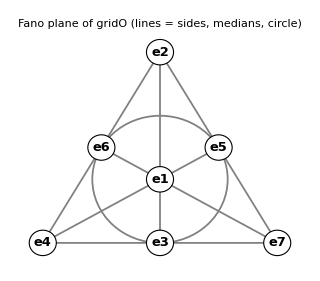

```mathematica
fanoPicture = Module[{pos, lines},
   pos = <|1 -> {0, 0}, 2 -> {0, 2}, 4 -> {-Sqrt[3], -1}, 7 -> {Sqrt[3], -1}, 6 -> {-Sqrt[3]/2, 1/2}, 5 -> {Sqrt[3]/2, 1/2}, 3 -> {0, -1}|>;
   Graphics[{Thickness[0.004], Gray,
     Line[{pos[2], pos[4]}], Line[{pos[4], pos[7]}], Line[{pos[7], pos[2]}],
     Line[{pos[2], pos[3]}], Line[{pos[4], pos[5]}], Line[{pos[7], pos[6]}], Circle[{0, 0}, 1],
     Table[{White, EdgeForm[Black], Disk[pos[k], 0.2], Black, Text[Style["e" <> ToString[k], 13, Bold], pos[k]]}, {k, 1, 7}]},
    ImageSize -> 320, PlotLabel -> Style["Fano plane of gridO (lines = sides, medians, circle)", 12]]];
check["the picture's 7 lines are exactly fanoLines", Sort[Sort /@ {{2, 6, 4}, {4, 3, 7}, {7, 5, 2}, {2, 1, 3}, {4, 1, 5}, {7, 1, 6}, {6, 5, 3}}] == fanoLines]
fanoPicture
```

#### Alternativity, Moufang identities, norm, conjugation, inverse (symbolic proofs)

xs, ys, zs are general octonions with symbolic components a[0..7], b[0..7], c[0..7]. Identities that are linear in some arguments (Moufang) are proven by letting those arguments run over the basis, which is enough by linearity.

```mathematica
check["left alternative: x(xy) == (xx)y (symbolic)", Expand[oMul[xs, oMul[xs, ys]] - oMul[oMul[xs, xs], ys]] === zero8]
check["right alternative: (yx)x == y(xx) (symbolic)", Expand[oMul[oMul[ys, xs], xs] - oMul[ys, oMul[xs, xs]]] === zero8]
check["flexible: (xy)x == x(yx) (symbolic)", Expand[oMul[oMul[xs, ys], xs] - oMul[xs, oMul[ys, xs]]] === zero8]
check["associator is alternating: [x,y,z] == -[y,x,z] == -[x,z,y] (symbolic)",
  Expand[oAssoc[xs, ys, zs] + oAssoc[ys, xs, zs]] === zero8 && Expand[oAssoc[xs, ys, zs] + oAssoc[xs, zs, ys]] === zero8]
check["power associativity: x(xx) == (xx)x (symbolic)", Expand[oMul[xs, oMul[xs, xs]] - oMul[oMul[xs, xs], xs]] === zero8]
check["Moufang: z(x(zy)) == ((zx)z)y, x(z(yz)) == ((xz)y)z, (zx)(yz) == (z(xy))z (x, y basis units, z symbolic)",
  And @@ Flatten[Table[With[{xx = ev[A], yy = ev[K]},
      Expand[oMul[zs, oMul[xx, oMul[zs, yy]]] - oMul[oMul[oMul[zs, xx], zs], yy]] === zero8 &&
      Expand[oMul[xx, oMul[zs, oMul[yy, zs]]] - oMul[oMul[oMul[xx, zs], yy], zs]] === zero8 &&
      Expand[oMul[oMul[zs, xx], oMul[yy, zs]] - oMul[oMul[zs, oMul[xx, yy]], zs]] === zero8], {A, 0, 7}, {K, 0, 7}]]]
check["x x̄ == x̄ x == N(x) e[0] (symbolic)",
  Expand[oMul[xs, oConj[xs]] - oNorm2[xs] ev[0]] === zero8 && Expand[oMul[oConj[xs], xs] - oNorm2[xs] ev[0]] === zero8]
check["conjugation is an anti-automorphism: conj(xy) == conj(y) conj(x) (symbolic)",
  Expand[oConj[oMul[xs, ys]] - oMul[oConj[ys], oConj[xs]]] === zero8]
check["Re(x) == (x + x̄)/2 == x0", (xs + oConj[xs])/2 == oRe[xs] ev[0] && oRe[xs] === a[0]]
check["norm is multiplicative: N(xy) == N(x) N(y) (symbolic; Degen's eight-square identity)",
  Expand[oNorm2[oMul[xs, ys]] - oNorm2[xs] oNorm2[ys]] === 0]
check["inverse x^-1 = x̄/N(x): x x^-1 == x^-1 x == e[0] (symbolic)",
  Simplify[oMul[xs, oInv[xs]] - ev[0]] === zero8 && Simplify[oMul[oInv[xs], xs] - ev[0]] === zero8]
check["every x satisfies x x - 2 Re(x) x + N(x) e[0] == 0, so the subalgebra generated by x is ℝ or ℂ",
  Expand[oMul[xs, xs] - 2 oRe[xs] xs + oNorm2[xs] ev[0]] === zero8]
```

left alternative: x(xy) == (xx)y (symbolic)→True

right alternative: (yx)x == y(xx) (symbolic)→True

flexible: (xy)x == x(yx) (symbolic)→True

associator is alternating: [x,y,z] == -[y,x,z] == -[x,z,y] (symbolic)→True

power associativity: x(xx) == (xx)x (symbolic)→True

Moufang: z(x(zy)) == ((zx)z)y, x(z(yz)) == ((xz)y)z, (zx)(yz) == (z(xy))z (x, y basis units, z symbolic)→True

x x̄ == x̄ x == N(x) e[0] (symbolic)→True

conjugation is an anti-automorphism: conj(xy) == conj(y) conj(x) (symbolic)→True

Re(x) == (x + x̄)/2 == x0→True

norm is multiplicative: N(xy) == N(x) N(y) (symbolic; Degen's eight-square identity)→True

inverse x^-1 = x̄/N(x): x x^-1 == x^-1 x == e[0] (symbolic)→True

every x satisfies x x - 2 Re(x) x + N(x) e[0] == 0, so the subalgebra generated by x is ℝ or ℂ→True

Degen’s eight-square identity, explicitly: the eight components of x y are bilinear forms, and the sum of their squares equals (a0.b2 + … + a7.b2)(b0.b2 + … + b7.b2). Hence N(x) = 0 forces x = 0, and xy = 0 forces x = 0 or y = 0: unlike the split octonions, the octonions have no zero divisors (a division algebra).

```mathematica
TableForm[Thread[{Table["(x y)_" <> ToString[k], {k, 0, 7}], oMul[xs, ys]}]]
```

(x y)_0 | a[0] b[0]-a[1] b[1]-a[2] b[2]-a[3] b[3]-a[4] b[4]-a[5] b[5]-a[6] b[6]-a[7] b[7]
(x y)_1 | a[1] b[0]+a[0] b[1]+a[3] b[2]-a[2] b[3]+a[5] b[4]-a[4] b[5]-a[7] b[6]+a[6] b[7]
(x y)_2 | a[2] b[0]-a[3] b[1]+a[0] b[2]+a[1] b[3]+a[6] b[4]+a[7] b[5]-a[4] b[6]-a[5] b[7]
(x y)_3 | a[3] b[0]+a[2] b[1]-a[1] b[2]+a[0] b[3]+a[7] b[4]-a[6] b[5]+a[5] b[6]-a[4] b[7]
(x y)_4 | a[4] b[0]-a[5] b[1]-a[6] b[2]-a[7] b[3]+a[0] b[4]+a[1] b[5]+a[2] b[6]+a[3] b[7]
(x y)_5 | a[5] b[0]+a[4] b[1]-a[7] b[2]+a[6] b[3]-a[1] b[4]+a[0] b[5]-a[3] b[6]+a[2] b[7]
(x y)_6 | a[6] b[0]+a[7] b[1]+a[4] b[2]-a[5] b[3]-a[2] b[4]+a[3] b[5]+a[0] b[6]-a[1] b[7]
(x y)_7 | a[7] b[0]-a[6] b[1]+a[5] b[2]+a[4] b[3]-a[3] b[4]-a[2] b[5]+a[1] b[6]+a[0] b[7]

#### Non-associativity and a numerical example

```mathematica
nonAssociativeTriples = Select[Tuples[Range[0, 7], 3], oAssoc[ev[#[[1]]], ev[#[[2]]], ev[#[[3]]]] =!= zero8 &];
check["exactly 168 of the 512 ordered basis triples are non-associative (= 7*6*4: distinct imaginary units not on one Fano line)",
  Length[nonAssociativeTriples] == 168 && AllTrue[nonAssociativeTriples, (Min[#] >= 1 && Length[Union[#]] == 3 && ! MemberQ[fanoLines, Sort[#]]) &]]
check["example: (e[1]e[2])e[4] == e[7] but e[1](e[2]e[4]) == -e[7]",
  toE[oMul[oMul[ev[1], ev[2]], ev[4]]] === e[7] && toE[oMul[ev[1], oMul[ev[2], ev[4]]]] === -e[7]]
```

exactly 168 of the 512 ordered basis triples are non-associative (= 7*6*4: distinct imaginary units not on one Fano line)→True

example: (e[1]e[2])e[4] == e[7] but e[1](e[2]e[4]) == -e[7]→True

```mathematica
xNum = {1, 2, 0, 0, -1, 0, 0, 3}; yNum = {-2, 0, 1, 0, 0, 1, 0, 0}; zNum = {0, 0, 0, 1, 0, 0, 1, 0};
Grid[{{"x", toE[xNum]}, {"y", toE[yNum]}, {"z", toE[zNum]}, {"x y", toE[oMul[xNum, yNum]]}, {"y x", toE[oMul[yNum, xNum]]},
   {"N(x), N(y), N(x y)", {oNorm2[xNum], oNorm2[yNum], oNorm2[oMul[xNum, yNum]]}}, {"x^-1", toE[oInv[xNum]]},
   {"x x^-1", toE[oMul[xNum, oInv[xNum]]]}, {"(x y) z - x (y z)", toE[oAssoc[xNum, yNum, zNum]]}}, Frame -> All, Alignment -> Left]
```

x | e[0]+2 e[1]-e[4]+3 e[7]
y | -2 e[0]+e[2]+e[5]
z | e[3]+e[6]
x y | -2 e[0]-3 e[1]+4 e[2]-2 e[3]+4 e[4]-2 e[5]-e[6]-6 e[7]
y x | -2 e[0]-5 e[1]-2 e[2]+2 e[3]+4 e[5]+e[6]-6 e[7]
N(x), N(y), N(x y) | {15,6,90}
x^-1 | e[0]/15-(2 e[1])/15+e[4]/15-e[7]/5
x x^-1 | e[0]
(x y) z - x (y z) | -6 e[1]-2 e[2]-6 e[3]+6 e[4]+2 e[5]+6 e[6]+6 e[7]

```mathematica
check["numerical example: N(x y) == N(x) N(y) == 15*6 == 90 and x x^-1 == e[0]",
  oNorm2[oMul[xNum, yNum]] == oNorm2[xNum] oNorm2[yNum] == 90 && oMul[xNum, oInv[xNum]] == ev[0]]
check["numerical example: x y != y x and (x y) z != x (y z)", oMul[xNum, yNum] != oMul[yNum, xNum] && oAssoc[xNum, yNum, zNum] != zero8]
```

numerical example: N(x y) == N(x) N(y) == 15*6 == 90 and x x^-1 == e[0]→True

numerical example: x y != y x and (x y) z != x (y z)→True

### 3.5 Cayley–Dickson doubling: 𝕆 = ℍ ⊕ ℓℍ

The span of e[0], e[1], e[2], e[3] — the time direction and the three ordinary space directions x0 … x3 — is a quaternion subalgebra ℍ, and ℓ = e[4] doubles it: e[4+k] = ℓ e[k] (k = 1, 2, 3). Every octonion is x = a + ℓ b with quaternions a = (x0, x1, x2, x3) and b = (x4, x5, x6, x7). Orientation inherited from 4+4.nb: e[1] e[2] = −e[3], so i = e[1], j = e[2], k = −e[3] are Hamilton’s units. With ℓ.b2 = γ the product is

(a, b)(c, d) = (a c + γ d b̄,  ā d + c b),     γ = −1: octonions,   γ = +1: split octonions.

```mathematica
qMul[p1_List, p2_List] := Take[oMul[Join[p1, {0, 0, 0, 0}], Join[p2, {0, 0, 0, 0}]], 4];
qConj[p1_List] := {p1[[1]], -p1[[2]], -p1[[3]], -p1[[4]]};
asPair[xx_List] := {Take[xx, 4], Take[xx, -4]};                       (* x = a + ℓ b  <->  {a, b} *)
cdMul[γ_][{a1_, b1_}, {a2_, b2_}] := {qMul[a1, a2] + γ qMul[b2, qConj[b1]], qMul[qConj[a1], b2] + qMul[a2, b1]};
check["ℍ = span{e[0],e[1],e[2],e[3]} is a subalgebra", And @@ Flatten[Table[Take[oMul[ev[A], ev[K]], -4] == {0, 0, 0, 0}, {A, 0, 3}, {K, 0, 3}]]]
check["ℓ = e[4] doubles ℍ: e[4] e[k] == e[4+k] (k = 1,2,3) and e[4] e[4] == -e[0]",
  And @@ Table[oMul[ev[4], ev[k]] == ev[4 + k], {k, 1, 3}] && oMul[ev[4], ev[4]] == -ev[0]]
check["orientation inherited from 4+4.nb: e[1] e[2] == -e[3]", oMul[ev[1], ev[2]] == -ev[3]]
check["Cayley-Dickson, γ = -1: (ac - d b̄, ā d + c b) reproduces the octonion product (symbolic)",
  Expand[Flatten[cdMul[-1][asPair[xs], asPair[ys]]] - oMul[xs, ys]] === zero8]
check["Cayley-Dickson, γ = +1: (ac + d b̄, ā d + c b) reproduces the SPLIT product of 4+4.nb (symbolic)",
  Expand[Flatten[cdMul[+1][asPair[xs], asPair[ys]]] - sMul[xs, ys]] === zero8]
```

ℍ = span{e[0],e[1],e[2],e[3]} is a subalgebra→True

ℓ = e[4] doubles ℍ: e[4] e[k] == e[4+k] (k = 1,2,3) and e[4] e[4] == -e[0]→True

orientation inherited from 4+4.nb: e[1] e[2] == -e[3]→True

Cayley-Dickson, γ = -1: (ac - d b̄, ā d + c b) reproduces the octonion product (symbolic)→True

Cayley-Dickson, γ = +1: (ac + d b̄, ā d + c b) reproduces the SPLIT product of 4+4.nb (symbolic)→True

The second formula of [1A], (a,b)(c,d) = (ac − d̄ b, ā d + c b), mixes two conventions. It fails already for x = e[0] + e[4] = (1, 1) and y = e[1] = (i, 0) (no product of two imaginary quaternion units occurs, so the orientation of ℍ does not matter): x.b2 = (0, 2), x.b2y = (0, 2i), but x y = (i, i) and x(xy) = (2i, 2i).

```mathematica
cdPrompt[{a1_, b1_}, {a2_, b2_}] := {qMul[a1, a2] - qMul[qConj[b2], b1], qMul[qConj[a1], b2] + qMul[a2, b1]};
pm[xx_List, yy_List] := Flatten[cdPrompt[asPair[xx], asPair[yy]]];
promptX = ev[0] + ev[4]; promptY = ev[1];
{toE[pm[pm[promptX, promptX], promptY]], toE[pm[promptX, pm[promptX, promptY]]]}
```

{2 e[5],2 e[1]+2 e[5]}

```mathematica
check["the formula (ac - d̄ b, ā d + c b) of [1A] is NOT alternative: x·x·y != x(xy) for x = e[0]+e[4], y = e[1]",
  pm[pm[promptX, promptX], promptY] =!= pm[promptX, pm[promptX, promptY]]]
check["... and its norm is not multiplicative (symbolic)", Expand[oNorm2[pm[xs, ys]] - oNorm2[xs] oNorm2[ys]] =!= 0]
```

the formula (ac - d̄ b, ā d + c b) of [1A] is NOT alternative: x·x·y != x(xy) for x = e[0]+e[4], y = e[1]→True

... and its norm is not multiplicative (symbolic)→True

### 3.6 Octonions versus split octonions

Comparing gridO with gridx44 (relabelled 0-based, eA[B] → e[B−1]): e[A]e[B] (octonion) = s_AB × e[A]e[B] (split), with s_AB = −1 when both A ≥ 4 and B ≥ 4, and s_AB = +1 otherwise. Only products of two “doubled” units change sign, because ℓ.b2 = −1 instead of +1. Over ℂ the two algebras are isomorphic: ϕ(eA[A+1]) = c_A e[A] with c = (1, 1, 1, 1, i, i, i, i).

```mathematica
sAB[A_, K_] := If[A >= 4 && K >= 4, -1, 1];
check["e[A]e[B] (octonion) == s_AB e[A]e[B] (split) for all A, B = 0..7",
  And @@ Flatten[Table[oMul[ev[A], ev[K]] == sAB[A, K] sMul[ev[A], ev[K]], {A, 0, 7}, {K, 0, 7}]]]
cc = {1, 1, 1, 1, I, I, I, I};
φ[xx_List] := cc xx;
check["over ℂ: φ(x *split y) == φ(x) *oct φ(y) (symbolic): split ⊗ ℂ ≅ 𝕆 ⊗ ℂ",
  Expand[φ[sMul[xs, ys]] - oMul[φ[xs], φ[ys]]] === zero8]
check["the norms correspond: N_oct(φ(x)) == N_split(x) (symbolic)", Expand[oNorm2[φ[xs]] - sNorm2[xs]] === 0]
```

e[A]e[B] (octonion) == s_AB e[A]e[B] (split) for all A, B = 0..7→True

over ℂ: φ(x *split y) == φ(x) *oct φ(y) (symbolic): split ⊗ ℂ ≅ 𝕆 ⊗ ℂ→True

the norms correspond: N_oct(φ(x)) == N_split(x) (symbolic)→True

## 4. Clifford algebras from the octonions: 16×16 matrices

### 4.1 The exact mirror of T16: the Euclidean Clifford algebra Cl(8,0)

Copying the 4+4.nb definition T16[A] = {{0, τbar[A]}, {τ[A], 0}} with τ → τO and τbar → τObar gives real 16×16 matrices T16O[A] whose anticommutators are governed by the octonion norm gO = ID8: they generate Cl(8,0) ≅ ℝ(16). They can be written with the 4+4 matrices alone: T16O[A] = T16[A] for A = 0 … 3 and T16O[k] = T16[k].S44 for k = 4 … 7, where S44 = T16[4].T16[5].T16[6].T16[7] = diag(σ, σ).

```mathematica
Do[T16O[A] = ArrayFlatten[{{0, τObar[A]}, {τO[A], 0}}], {A, 0, 7}];
T16O[8] = Dot @@ Table[T16O[A], {A, 0, 7}];
S44 = T16[4].T16[5].T16[6].T16[7];
check["Cl(8,0): (T16O[A].T16O[B] + T16O[B].T16O[A])/2 == gO[[A+1,B+1]] ID16",
  And @@ Flatten[Table[(T16O[A].T16O[B] + T16O[B].T16O[A])/2 == gO[[A + 1, B + 1]] ID16, {A, 0, 7}, {B, 0, 7}]]]
check["S44 == diag(σ, σ)", S44 == ArrayFlatten[{{σ, 0}, {0, σ}}]]
check["T16O from the 4+4 matrices: T16O[A] == T16[A] (A = 0..3), T16O[k] == T16[k].S44 (k = 4..7)",
  And @@ Table[T16O[A] == T16[A], {A, 0, 3}] && And @@ Table[T16O[k] == T16[k].S44, {k, 4, 7}]]
check["T16O[8] == T16[8] == diag(-ID8, ID8): same chirality matrix and same PL44, PR44 as 4+4.nb",
  T16O[8] == T16[8] == ArrayFlatten[{{-ID8, 0}, {0, ID8}}]]
```

Cl(8,0): (T16O[A].T16O[B] + T16O[B].T16O[A])/2 == gO[[A+1,B+1]] ID16→True

S44 == diag(σ, σ)→True

T16O from the 4+4 matrices: T16O[A] == T16[A] (A = 0..3), T16O[k] == T16[k].S44 (k = 4..7)→True

T16O[8] == T16[8] == diag(-ID8, ID8): same chirality matrix and same PL44, PR44 as 4+4.nb→True

### 4.2 The REAL Clifford algebra of 7+1 spacetime: Γ17, Cl(1,7) ≅ ℝ(16)

Definition. Γ17[0] = T16O[0] (time) and Γ17[i] = T16O[0].T16O[i] (i = 1 … 7, space). Then

Γ17[A].Γ17[B] + Γ17[B].Γ17[A] = 2 η17[[A+1,B+1]] ID16 = −2 η71[[A+1,B+1]] ID16:

time squares to +ID16, each of the seven space directions to −ID16. In block form Γ17[0] = {{0, ID8}, {ID8, 0}} (the same block form as T16[0]) and Γ17[i] = {{τO[i], 0}, {0, τObar[i]}} (block-diagonal). With the 4+4 matrices only: Γ17[0] = T16[0], Γ17[i] = T16[0].T16[i] (i = 1, 2, 3), Γ17[k] = T16[0].T16[k].S44 (k = 4 … 7). All entries are 0 or ±1.

Why this is the Clifford algebra of [1B]. (i) The linear map v ↦ Γ17(v) = Σ v^A Γ17[A] satisfies Γ17(v).b2 = Q(v) ID16 with Q(v) = v.η17.v, so by the universal property of Cl(V,Q) = T(V)/I_Q(V) it extends to an algebra homomorphism Cl(V,Q) → ℝ(16). (ii) The 256 ordered products Γ17[A1]…Γ17[Ak] (A1 < … < Ak) are linearly independent, so the homomorphism is injective; both sides have dimension 256, so it is an isomorphism Cl(1,7) ≅ ℝ(16).

```mathematica
Γ17[0] = T16O[0];
Do[Γ17[i] = T16O[0].T16O[i], {i, 1, 7}];
Γ17[8] = Dot @@ Table[Γ17[A], {A, 0, 7}];
check["7+1 REAL Clifford relation: (Γ17[A].Γ17[B] + Γ17[B].Γ17[A])/2 == η17[[A+1,B+1]] ID16 == -η71[[A+1,B+1]] ID16",
  And @@ Flatten[Table[(Γ17[A].Γ17[B] + Γ17[B].Γ17[A])/2 == η17[[A + 1, B + 1]] ID16 == -η71[[A + 1, B + 1]] ID16, {A, 0, 7}, {B, 0, 7}]]]
check["Γ17[A] are REAL: every entry is 0 or ±1", And @@ Table[SubsetQ[{-1, 0, 1}, Union[Flatten[Γ17[A]]]], {A, 0, 7}]]
check["block form: Γ17[0] == {{0,ID8},{ID8,0}}, Γ17[i] == {{τO[i],0},{0,τObar[i]}}",
  Γ17[0] == ArrayFlatten[{{0, ID8}, {ID8, 0}}] && And @@ Table[Γ17[i] == ArrayFlatten[{{τO[i], 0}, {0, τObar[i]}}], {i, 1, 7}]]
check["built from the real 4+4 matrices: Γ17[0] == T16[0], Γ17[i] == T16[0].T16[i] (i = 1,2,3), Γ17[k] == T16[0].T16[k].S44 (k = 4..7)",
  Γ17[0] == T16[0] && And @@ Table[Γ17[i] == T16[0].T16[i], {i, 1, 3}] && And @@ Table[Γ17[k] == T16[0].T16[k].S44, {k, 4, 7}]]
check["Γ17[0] symmetric, Γ17[i] antisymmetric, so Transpose[Γ17[A]] == Γ17[0].Γ17[A].Γ17[0] (real Dirac adjoint)",
  Transpose[Γ17[0]] == Γ17[0] && And @@ Table[Transpose[Γ17[i]] == -Γ17[i], {i, 1, 7}] &&
  And @@ Table[Transpose[Γ17[A]] == Γ17[0].Γ17[A].Γ17[0], {A, 0, 7}]]
```

7+1 REAL Clifford relation: (Γ17[A].Γ17[B] + Γ17[B].Γ17[A])/2 == η17[[A+1,B+1]] ID16 == -η71[[A+1,B+1]] ID16→True

Γ17[A] are REAL: every entry is 0 or ±1→True

block form: Γ17[0] == {{0,ID8},{ID8,0}}, Γ17[i] == {{τO[i],0},{0,τObar[i]}}→True

built from the real 4+4 matrices: Γ17[0] == T16[0], Γ17[i] == T16[0].T16[i] (i = 1,2,3), Γ17[k] == T16[0].T16[k].S44 (k = 4..7)→True

Γ17[0] symmetric, Γ17[i] antisymmetric, so Transpose[Γ17[A]] == Γ17[0].Γ17[A].Γ17[0] (real Dirac adjoint)→True

```mathematica
Grid[Partition[Table[Column[{Style["Γ17[" <> ToString[A] <> "]", Bold], MatrixForm[Γ17[A]]}, Alignment -> Center], {A, 0, 7}], 2], Spacings -> {3, 2}]
```

Γ17[0]
(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | Γ17[1]
(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
Γ17[2]
(0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0) | Γ17[3]
(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0)
Γ17[4]
(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0) | Γ17[5]
(0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0)
Γ17[6]
(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0) | Γ17[7]
(0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0)

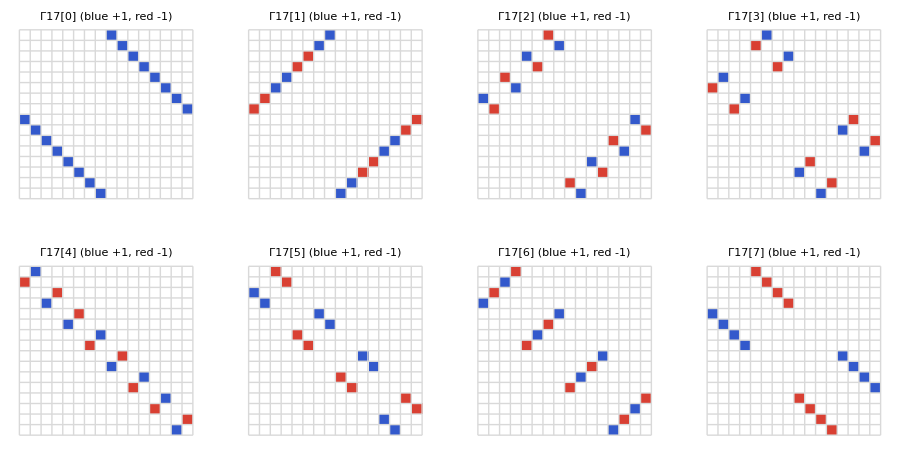

```mathematica
GraphicsGrid[Partition[Table[ArrayPlot[Γ17[A], ColorRules -> {1 -> RGBColor[0.2, 0.35, 0.8], -1 -> RGBColor[0.85, 0.25, 0.2], 0 -> White},
     Mesh -> True, MeshStyle -> GrayLevel[0.85], Frame -> False, PlotLabel -> "Γ17[" <> ToString[A] <> "]   (blue +1, red -1)"], {A, 0, 7}], 4], ImageSize -> 900]
```

```mathematica
products256 = Table[Dot @@ Prepend[Γ17 /@ s, ID16], {s, Subsets[Range[0, 7]]}];
check["the 256 products Γ17[A1]...Γ17[Ak] (A1 < ... < Ak) are linearly independent: Cl(1,7) ≅ ℝ(16)",
  Length[products256] == 256 && MatrixRank[Flatten /@ products256] == 256]
check["grades: binomial(8,k) == {1,8,28,56,70,56,28,8,1}, total 256 (binomial(8,4) == 70, not 72)",
  Table[Binomial[8, k], {k, 0, 8}] == {1, 8, 28, 56, 70, 56, 28, 8, 1} && Total[Table[Binomial[8, k], {k, 0, 8}]] == 256 &&
  Table[Count[Subsets[Range[0, 7]], s_ /; Length[s] == k], {k, 0, 8}] == Table[Binomial[8, k], {k, 0, 8}]]
check["Tr[product] == 0 for every non-empty product, so Tr[M]/16 is the scalar part of M", And @@ Table[Tr[products256[[k]]] == 0, {k, 2, 256}]]
check["irreducible over ℝ: only multiples of ID16 commute with all Γ17[A] (Schur; real commutant of dimension 1)",
  With[{ns = NullSpace[Join @@ Table[KroneckerProduct[ID16, Transpose[Γ17[A]]] - KroneckerProduct[Γ17[A], ID16], {A, 0, 7}]]},
   Length[ns] == 1 && MatrixRank[{First[ns], Flatten[ID16]}] == 1]]
check["universal property: Γ17(v).Γ17(v) == (v.η17.v) ID16 for a symbolic vector v = X",
  Expand[Sum[X[[A + 1]] Γ17[A], {A, 0, 7}].Sum[X[[A + 1]] Γ17[A], {A, 0, 7}] - (X.η17.X) ID16] === Zero16]
```

the 256 products Γ17[A1]...Γ17[Ak] (A1 < ... < Ak) are linearly independent: Cl(1,7) ≅ ℝ(16)→True

grades: binomial(8,k) == {1,8,28,56,70,56,28,8,1}, total 256 (binomial(8,4) == 70, not 72)→True

Tr[product] == 0 for every non-empty product, so Tr[M]/16 is the scalar part of M→True

irreducible over ℝ: only multiples of ID16 commute with all Γ17[A] (Schur; real commutant of dimension 1)→True

universal property: Γ17(v).Γ17(v) == (v.η17.v) ID16 for a symbolic vector v = X→True

### 4.3 The complexified 7+1 realization in the exact block form of 4+4.nb: Γ71

If one insists on the 4+4.nb sign convention, Γ71[A].Γ71[B] + Γ71[B].Γ71[A] = 2 η71[[A+1,B+1]] ID16, complex numbers are unavoidable (section 4.4). The complexification needed is minimal: multiply the time block by i. With τC[0] = τCbar[0] = i ID8 and τC[i] = τO[i], τCbar[i] = τObar[i] (i = 1 … 7),

Γ71[A] = {{0, τCbar[A]}, {τC[A], 0}},

which is literally the formula T16[A] = {{0, τbar[A]}, {τ[A], 0}} of 4+4.nb. Equivalently Γ71[0] = i T16[0] and Γ71[k] = T16O[k] (k = 1 … 7). Γ71 is equivalent to i Γ17: Γ71[A] = S.(i Γ17[A]).S⁻.b9 with the unitary matrix S = (ID16 − i Γ17[0])/√2.

```mathematica
τC[0] = I ID8; τCbar[0] = I ID8;
Do[τC[i] = τO[i]; τCbar[i] = τObar[i], {i, 1, 7}];
Do[Γ71[A] = ArrayFlatten[{{0, τCbar[A]}, {τC[A], 0}}], {A, 0, 7}];
Γ71[8] = Dot @@ Table[Γ71[A], {A, 0, 7}];
check["7+1 COMPLEX Clifford relation, 4+4.nb sign: (Γ71[A].Γ71[B] + Γ71[B].Γ71[A])/2 == η71[[A+1,B+1]] ID16",
  And @@ Flatten[Table[(Γ71[A].Γ71[B] + Γ71[B].Γ71[A])/2 == η71[[A + 1, B + 1]] ID16, {A, 0, 7}, {B, 0, 7}]]]
check["Γ71[0] == I T16[0] and Γ71[k] == T16O[k] (k = 1..7): only the time component is complex",
  Γ71[0] == I T16[0] && And @@ Table[Γ71[k] == T16O[k], {k, 1, 7}]]
Ssim = (ID16 - I Γ17[0])/Sqrt[2];
check["S = (ID16 - I Γ17[0])/Sqrt[2] is unitary and Γ71[A] == S.(I Γ17[A]).Inverse[S]",
  Simplify[Ssim.ConjugateTranspose[Ssim]] == ID16 && And @@ Table[Simplify[Ssim.(I Γ17[A]).Inverse[Ssim] - Γ71[A]] == Zero16, {A, 0, 7}]]
```

7+1 COMPLEX Clifford relation, 4+4.nb sign: (Γ71[A].Γ71[B] + Γ71[B].Γ71[A])/2 == η71[[A+1,B+1]] ID16→True

Γ71[0] == I T16[0] and Γ71[k] == T16O[k] (k = 1..7): only the time component is complex→True

S = (ID16 - I Γ17[0])/Sqrt[2] is unitary and Γ71[A] == S.(I Γ17[A]).Inverse[S]→True

### 4.4 Theorem: with η71 there is no real 16×16 realization, because Cl(7,1) ≅ ℍ(8)

Theorem. There are no real 16×16 matrices R[0], …, R[7] with R[A].R[B] + R[B].R[A] = 2 η71[[A+1,B+1]] ID16. Reordering, renaming or re-signing the indices does not help, because none of these changes the signature (7,1).

Proof. The complexified Clifford algebra is Cl_8(ℂ) ≅ ℂ(16), which has exactly one irreducible module, ℂ^16. If real R[A] existed, they and the complex Γ71[A] of section 4.3 would both be 16-dimensional modules, so R[A] = T.Γ71[A].T⁻.b9 for some invertible complex T. Complex conjugation of this equation (R is real) gives M.Conjugate[Γ71[A]] = Γ71[A].M with M = T⁻.b9.Conjugate[T], and then M.Conjugate[M] = ID16. By Schur’s lemma all such intertwiners M form a one-dimensional space; the computation below shows that it is spanned by M0 = Γ17[8] (the volume element) and that M0.Conjugate[M0] = −ID16. Hence M = c M0 and M.Conjugate[M] = −|c|.b2 ID16 ≠ ID16, a contradiction. ∎

The sign of M.Conjugate[M] is a Frobenius–Schur-type indicator: +1 means the complex 16-dimensional module has a real form (the algebra is ℝ(16)), −1 means it is quaternionic (the algebra is ℍ(8), whose smallest real module is ℍ^8 = ℝ^32). For η17 the indicator is +1, in agreement with the real matrices Γ17 of section 4.2.

```mathematica
intertwiners[gs_List] := Module[{n = Length[First[gs]], sys},
   sys = Join @@ Table[KroneckerProduct[IdentityMatrix[n], Transpose[Conjugate[g]]] - KroneckerProduct[g, IdentityMatrix[n]], {g, gs}];
   Partition[#, n] & /@ NullSpace[sys]];       (* all M with M.Conjugate[g] == g.M for every g in gs *)
indicator[gs_List] := Module[{M = First[intertwiners[gs]], P}, P = M.Conjugate[M];
   If[P == P[[1, 1]] IdentityMatrix[Length[P]], Sign[P[[1, 1]]], "not scalar"]];
M71 = intertwiners[Table[Γ71[A], {A, 0, 7}]];
check["Schur: the intertwiners M with M.Conjugate[Γ71[A]] == Γ71[A].M form a 1-dimensional space", Length[M71] == 1]
check["... spanned by the volume element Γ17[8] == {{0,-ID8},{ID8,0}}, and Γ17[8].Γ17[8] == -ID16",
  Γ17[8] == ArrayFlatten[{{0, -ID8}, {ID8, 0}}] &&
  MatrixRank[{Flatten[First[M71]], Flatten[Γ17[8]]}] == 1 && Γ17[8].Γ17[8] == -ID16 &&
  And @@ Table[Γ17[8].Conjugate[Γ71[A]] == Γ71[A].Γ17[8], {A, 0, 7}]]
check["indicator(Γ71) == -1: Cl(7,1) ≅ ℍ(8), NO real 16×16 realization of the η71 relation",
  indicator[Table[Γ71[A], {A, 0, 7}]] == -1]
check["indicator(Γ17) == +1: Cl(1,7) ≅ ℝ(16), real realization exists (Γ17)",
  indicator[Table[Γ17[A], {A, 0, 7}]] == 1]
```

Schur: the intertwiners M with M.Conjugate[Γ71[A]] == Γ71[A].M form a 1-dimensional space→True

... spanned by the volume element Γ17[8] == {{0,-ID8},{ID8,0}}, and Γ17[8].Γ17[8] == -ID16→True

indicator(Γ71) == -1: Cl(7,1) ≅ ℍ(8), NO real 16×16 realization of the η71 relation→True

indicator(Γ17) == +1: Cl(1,7) ≅ ℝ(16), real realization exists (Γ17)→True

### 4.5 A real realization of Cl(7,1) needs 32×32 matrices

With ϵ = {{0, 1}, {−1, 0}} (real, ϵ.ϵ = −ID2), Γ71R32[A] = ϵ ⊗ Γ17[A] are real 32×32 matrices satisfying the η71 relation. Their commutant (all matrices commuting with every Γ71R32[A]) is spanned by ID32, Qi = ϵ⊗ID16, Qj = σ₁⊗Γ17[8], Qk = σ₃⊗Γ17[8], with Qi.b2 = Qj.b2 = Qk.b2 = −ID32 and Qi.Qj = Qk: the quaternions. This is Cl(7,1) ≅ ℍ(8) acting on ℝ^32 = ℍ^8.

```mathematica
ϵ2 = {{0, 1}, {-1, 0}};
Do[Γ71R32[A] = KroneckerProduct[ϵ2, Γ17[A]], {A, 0, 7}];
check["REAL 32×32 realization of the η71 relation: (Γ71R32[A].Γ71R32[B] + Γ71R32[B].Γ71R32[A])/2 == η71[[A+1,B+1]] ID32",
  And @@ Flatten[Table[(Γ71R32[A].Γ71R32[B] + Γ71R32[B].Γ71R32[A])/2 == η71[[A + 1, B + 1]] ID32, {A, 0, 7}, {B, 0, 7}]] &&
  And @@ Table[SubsetQ[{-1, 0, 1}, Union[Flatten[Γ71R32[A]]]], {A, 0, 7}]]
Qi = KroneckerProduct[ϵ2, ID16]; Qj = KroneckerProduct[{{0, 1}, {1, 0}}, Γ17[8]]; Qk = KroneckerProduct[{{1, 0}, {0, -1}}, Γ17[8]];
check["Qi, Qj, Qk commute with every Γ71R32[A]; Qi.Qi == Qj.Qj == Qk.Qk == -ID32; Qi.Qj == Qk == -Qj.Qi",
  And @@ Flatten[Table[q.Γ71R32[A] == Γ71R32[A].q, {q, {Qi, Qj, Qk}}, {A, 0, 7}]] &&
  Qi.Qi == -ID32 && Qj.Qj == -ID32 && Qk.Qk == -ID32 && Qi.Qj == Qk && Qj.Qi == -Qk]
{commutantTime, commutantBasis} = AbsoluteTiming[NullSpace[Join @@ Table[
       KroneckerProduct[SparseArray[ID32], SparseArray[Transpose[Γ71R32[A]]]] - KroneckerProduct[SparseArray[Γ71R32[A]], SparseArray[ID32]], {A, 0, 7}]]];
check["the commutant of {Γ71R32[A]} has dimension exactly 4 and is spanned by ID32, Qi, Qj, Qk: it is ℍ",
  Length[commutantBasis] == 4 && MatrixRank[Join[Normal[commutantBasis], Flatten /@ {ID32, Qi, Qj, Qk}]] == 4]
commutantTime
```

REAL 32×32 realization of the η71 relation: (Γ71R32[A].Γ71R32[B] + Γ71R32[B].Γ71R32[A])/2 == η71[[A+1,B+1]] ID32→True

Qi, Qj, Qk commute with every Γ71R32[A]; Qi.Qi == Qj.Qj == Qk.Qk == -ID32; Qi.Qj == Qk == -Qj.Qi→True

the commutant of {Γ71R32[A]} has dimension exactly 4 and is spanned by ID32, Qi, Qj, Qk: it is ℍ→True

1.05471

### 4.6 Volume elements and chirality

In 4+4.nb the volume element T16[8] = T16[0]…T16[7] = diag(−ID8, ID8) squares to +ID16 and gives the real chiral projectors PL44, PR44; the same holds for T16O[8]. For the real 7+1 matrices the volume element Γ17[8] squares to −ID16: it is a complex structure, so there is NO real chirality projector. The real 16-component spinors of 7+1 spacetime (the vectors of ℝ^16 on which the real matrices Σ17[A,B] of section 5.1 act) cannot be split into real Weyl halves; with J = Γ17[8] (which commutes with all Σ17[A,B]) as the multiplication by i, the real 16-dimensional spin module is one complex 8-dimensional Weyl module. With complex numbers the chirality matrix is χ17 = i Γ17[8]; in the basis of Γ71 it is χ71 = −i Γ71[8] = T16[8], so the 7+1 chiral projectors are literally PL44 and PR44 of 4+4.nb.

```mathematica
check["Γ17[8].Γ17[8] == -ID16 and Γ17[8] anticommutes with every Γ17[A]: no real chirality in 7+1",
  Γ17[8].Γ17[8] == -ID16 && And @@ Table[Γ17[8].Γ17[A] == -Γ17[A].Γ17[8], {A, 0, 7}]]
χ71 = -I Γ71[8];
check["Γ71[8].Γ71[8] == -ID16 and χ71 = -I Γ71[8] == T16O[8] == T16[8] (real, diagonal)",
  Γ71[8].Γ71[8] == -ID16 && χ71 == T16O[8] == T16[8]]
PL71 = (ID16 - χ71)/2; PR71 = (ID16 + χ71)/2;
check["7+1 chiral projectors in the Γ71 basis are exactly PL44, PR44 of 4+4.nb; χ71 anticommutes with every Γ71[A]",
  PL71 == PL44 && PR71 == PR44 && And @@ Table[χ71.Γ71[A] == -Γ71[A].χ71, {A, 0, 7}]]
χ17 = I Γ17[8]; PL17 = (ID16 - χ17)/2; PR17 = (ID16 + χ17)/2;
check["complex chiral projectors for Γ17: PL17 + PR17 == ID16, PL17.PL17 == PL17, PL17.PR17 == 0, rank 8 each",
  PL17 + PR17 == ID16 && PL17.PL17 == PL17 && PR17.PR17 == PR17 && PL17.PR17 == Zero16 && MatrixRank[PL17] == 8 && MatrixRank[PR17] == 8]
```

Γ17[8].Γ17[8] == -ID16 and Γ17[8] anticommutes with every Γ17[A]: no real chirality in 7+1→True

Γ71[8].Γ71[8] == -ID16 and χ71 = -I Γ71[8] == T16O[8] == T16[8] (real, diagonal)→True

7+1 chiral projectors in the Γ71 basis are exactly PL44, PR44 of 4+4.nb; χ71 anticommutes with every Γ71[A]→True

complex chiral projectors for Γ17: PL17 + PR17 == ID16, PL17.PL17 == PL17, PL17.PR17 == 0, rank 8 each→True

### 4.7 What the octonions do: Γ(x).b2 = Re(x x), and alternativity

For x = Σ x^A e[A] with components equal to the coordinates X: Re(x x) = x0.b2 − x1.b2 − … − x7.b2 = X.η17.X, the 7+1 interval, and Γ17(x).b2 = Re(x x) ID16. In the octonion basis (rotate both 8-blocks by EO) the generators are Γ17e[0] = {{0, ID8}, {ID8, 0}} and Γ17e[i] = {{LO[i], 0}, {0, −LO[i]}}. Write x = x0 e[0] + x⃗ with the imaginary part x⃗ = x1 e[1] + … + x7 e[7] (xImag in the code); then on Ψ = (ψ1, ψ2) ∈ 𝕆 ⊕ 𝕆:

Γ17e(x) Ψ = (x0 ψ2 + x⃗ ψ1,  x0 ψ1 − x⃗ ψ2)   (octonion products),

Γ17e(x).b2 Ψ = (x0.b2 ψ1 + x⃗(x⃗ ψ1),  x0.b2 ψ2 + x⃗(x⃗ ψ2)) = (x0.b2 − |x⃗|.b2) Ψ,

where the last step is exactly alternativity: x⃗(x⃗ ψ) = (x⃗ x⃗) ψ = −|x⃗|.b2 ψ. The same formula with the norm form instead of Re(x x) gives T16O(x).b2 = N(x) ID16, and in 4+4.nb T16(x).b2 = X.η4488.X ID16.

```mathematica
check["Re(x x) == X.η17.X: the octonion square produces the 7+1 interval (symbolic)", Expand[oRe[oMul[X, X]] - X.η17.X] === 0]
EO16 = ArrayFlatten[{{EO, 0}, {0, EO}}];
Do[Γ17e[A] = FullSimplify[EO16.Γ17[A].Transpose[EO16]], {A, 0, 7}];
check["octonion basis: Γ17e[0] == {{0,ID8},{ID8,0}} and Γ17e[i] == {{LO[i],0},{0,-LO[i]}}",
  Γ17e[0] == ArrayFlatten[{{0, ID8}, {ID8, 0}}] && And @@ Table[Γ17e[i] == ArrayFlatten[{{LO[i], 0}, {0, -LO[i]}}], {i, 1, 7}]]
xImag = Join[{0}, Rest[X]]; ψs = Array[ψ, 8, 0];
check["alternativity in action: xImag(xImag ψ) == -|xImag|^2 ψ for the imaginary part xImag of x (symbolic)", Expand[oMul[xImag, oMul[xImag, ψs]] + (Rest[X].Rest[X]) ψs] === zero8]
check["T16O(x)^2 == N(x) ID16 (octonion norm) and T16(x)^2 == (X.η4488.X) ID16 (4+4.nb)",
  Expand[Sum[X[[A + 1]] T16O[A], {A, 0, 7}].Sum[X[[A + 1]] T16O[A], {A, 0, 7}] - (X.gO.X) ID16] === Zero16 &&
  Expand[Sum[X[[A + 1]] T16[A], {A, 0, 7}].Sum[X[[A + 1]] T16[A], {A, 0, 7}] - (X.η4488.X) ID16] === Zero16]
```

Re(x x) == X.η17.X: the octonion square produces the 7+1 interval (symbolic)→True

octonion basis: Γ17e[0] == {{0,ID8},{ID8,0}} and Γ17e[i] == {{LO[i],0},{0,-LO[i]}}→True

alternativity in action: xImag(xImag ψ) == -|xImag|^2 ψ for the imaginary part xImag of x (symbolic)→True

T16O(x)^2 == N(x) ID16 (octonion norm) and T16(x)^2 == (X.η4488.X) ID16 (4+4.nb)→True

## 5. Examples that test everything

### 5.1 The Lorentz algebra so(1,7)

The 28 real matrices Σ17[A,B] = (Γ17[A].Γ17[B] − Γ17[B].Γ17[A])/4 (A < B) generate Spin(1,7). They satisfy

[Σ17[A,B], Γ17[K]] = η17[[B+1,K+1]] Γ17[A] − η17[[A+1,K+1]] Γ17[B],

[Σ_AB, Σ_KL] = η_BK Σ_AL − η_AK Σ_BL − η_BL Σ_AK + η_AL Σ_BK   (η = η17).

```mathematica
Σ17[A_, B_] := (Γ17[A].Γ17[B] - Γ17[B].Γ17[A])/4;
pairs = Subsets[Range[0, 7], {2}];
check["28 real generators Σ17[A,B] (A < B), linearly independent", Length[pairs] == 28 && MatrixRank[Flatten[Σ17 @@ #] & /@ pairs] == 28]
check["[Σ17[A,B], Γ17[K]] == η17[[B+1,K+1]] Γ17[A] - η17[[A+1,K+1]] Γ17[B]",
  And @@ Flatten[Table[Σ17[A, B].Γ17[K] - Γ17[K].Σ17[A, B] == η17[[B + 1, K + 1]] Γ17[A] - η17[[A + 1, K + 1]] Γ17[B], {A, 0, 7}, {B, 0, 7}, {K, 0, 7}]]]
check["so(1,7): [Σ_AB, Σ_KL] == η_BK Σ_AL - η_AK Σ_BL - η_BL Σ_AK + η_AL Σ_BK",
  And @@ Flatten[Table[With[{A = p1[[1]], B = p1[[2]], K = p2[[1]], L = p2[[2]]},
      Σ17[A, B].Σ17[K, L] - Σ17[K, L].Σ17[A, B] ==
       η17[[B + 1, K + 1]] Σ17[A, L] - η17[[A + 1, K + 1]] Σ17[B, L] - η17[[B + 1, L + 1]] Σ17[A, K] + η17[[A + 1, L + 1]] Σ17[B, K]], {p1, pairs}, {p2, pairs}]]]
check["the complex structure J = Γ17[8] commutes with all Σ17[A,B] (Spin(1,7) acts complex-linearly on ℝ^16 = ℂ^8)",
  And @@ Table[Γ17[8].(Σ17 @@ p) == (Σ17 @@ p).Γ17[8], {p, pairs}]]
```

28 real generators Σ17[A,B] (A < B), linearly independent→True

[Σ17[A,B], Γ17[K]] == η17[[B+1,K+1]] Γ17[A] - η17[[A+1,K+1]] Γ17[B]→True

so(1,7): [Σ_AB, Σ_KL] == η_BK Σ_AL - η_AK Σ_BL - η_BL Σ_AK + η_AL Σ_BK→True

the complex structure J = Γ17[8] commutes with all Σ17[A,B] (Spin(1,7) acts complex-linearly on ℝ^16 = ℂ^8)→True

### 5.2 A boost along x1 and a rotation in the x4–x5 plane

Because (Γ17[0].Γ17[1]).b2 = +ID16 and (Γ17[4].Γ17[5]).b2 = −ID16, the exponentials are

S(β) = exp(β Σ17[0,1]) = cosh(β/2) ID16 + sinh(β/2) Γ17[0].Γ17[1],    R(θ) = exp(θ Σ17[4,5]) = cos(θ/2) ID16 + sin(θ/2) Γ17[4].Γ17[5],

both real. Conjugation by them acts on the generators as a Lorentz transformation, S.Γ17[K].S⁻.b9 = Σ_B Λ[[B+1,K+1]] Γ17[B], with Λ read off from traces: Λ[[B+1,K+1]] = Tr[Γ17^B.S.Γ17[K].S⁻.b9]/16, Γ17^B = η17[[B+1,B+1]] Γ17[B].

```mathematica
Sβ = Cosh[β/2] ID16 + Sinh[β/2] Γ17[0].Γ17[1];  Sβinv = Cosh[β/2] ID16 - Sinh[β/2] Γ17[0].Γ17[1];
Rθ = Cos[θ/2] ID16 + Sin[θ/2] Γ17[4].Γ17[5];  Rθinv = Cos[θ/2] ID16 - Sin[θ/2] Γ17[4].Γ17[5];
check["S(β) and R(θ) are the exponentials: dS/dβ == Σ17[0,1].S, S(0) == ID16, dR/dθ == Σ17[4,5].R, R(0) == ID16, and S.Sinv == R.Rinv == ID16",
  Simplify[D[Sβ, β] - Σ17[0, 1].Sβ] == Zero16 && (Sβ /. β -> 0) == ID16 &&
  Simplify[D[Rθ, θ] - Σ17[4, 5].Rθ] == Zero16 && (Rθ /. θ -> 0) == ID16 &&
  Simplify[Sβ.Sβinv] == ID16 && Simplify[Rθ.Rθinv] == ID16]
Λboost = Table[Simplify[Tr[η17[[B + 1, B + 1]] Γ17[B].Sβ.Γ17[K].Sβinv]/16], {B, 0, 7}, {K, 0, 7}];
Λrot = Table[Simplify[Tr[η17[[B + 1, B + 1]] Γ17[B].Rθ.Γ17[K].Rθinv]/16], {B, 0, 7}, {K, 0, 7}];
{MatrixForm[Λboost], MatrixForm[Λrot]}
```

S(β) and R(θ) are the exponentials: dS/dβ == Σ17[0,1].S, S(0) == ID16, dR/dθ == Σ17[4,5].R, R(0) == ID16, and S.Sinv == R.Rinv == ID16→True

{(Cosh[β] | -Sinh[β] | 0 | 0 | 0 | 0 | 0 | 0
-Sinh[β] | Cosh[β] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Cos[θ] | -Sin[θ] | 0 | 0
0 | 0 | 0 | 0 | Sin[θ] | Cos[θ] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)}

```mathematica
check["S(β).Γ17[K].S(β)^-1 == ∑_B Λboost[[B+1,K+1]] Γ17[B]; Λboost is the boost along x1",
  And @@ Table[Simplify[Sβ.Γ17[K].Sβinv - Sum[Λboost[[B + 1, K + 1]] Γ17[B], {B, 0, 7}]] == Zero16, {K, 0, 7}] &&
  Λboost == ReplacePart[IdentityMatrix[8], {{1, 1} -> Cosh[β], {1, 2} -> -Sinh[β], {2, 1} -> -Sinh[β], {2, 2} -> Cosh[β]}]]
check["R(θ).Γ17[K].R(θ)^-1 == ∑_B Λrot[[B+1,K+1]] Γ17[B]; Λrot is the rotation in the x4-x5 plane",
  And @@ Table[Simplify[Rθ.Γ17[K].Rθinv - Sum[Λrot[[B + 1, K + 1]] Γ17[B], {B, 0, 7}]] == Zero16, {K, 0, 7}] &&
  Λrot == ReplacePart[IdentityMatrix[8], {{5, 5} -> Cos[θ], {5, 6} -> -Sin[θ], {6, 5} -> Sin[θ], {6, 6} -> Cos[θ]}]]
check["both Λ preserve the 7+1 metric: Transpose[Λ].η17.Λ == η17",
  Simplify[Transpose[Λboost].η17.Λboost - η17] == ConstantArray[0, {8, 8}] &&
  Simplify[Transpose[Λrot].η17.Λrot - η17] == ConstantArray[0, {8, 8}]]
```

S(β).Γ17[K].S(β)^-1 == ∑_B Λboost[[B+1,K+1]] Γ17[B]; Λboost is the boost along x1→True

R(θ).Γ17[K].R(θ)^-1 == ∑_B Λrot[[B+1,K+1]] Γ17[B]; Λrot is the rotation in the x4-x5 plane→True

both Λ preserve the 7+1 metric: Transpose[Λ].η17.Λ == η17→True

### 5.3 The 7+1 Dirac operator squares to the 7+1 wave operator

With Γ17^A = η17^{AA} Γ17[A] (index raised with the inverse metric) the Dirac operator is Γ17^A ∂_A, acting on 16-component fields Ψ(x0, …, x7). Its square is the wave operator ∂₀.b2 − ∂₁.b2 − … − ∂₇.b2 times ID16, for completely arbitrary functions:

```mathematica
η17inv = Inverse[η17];
Γ17up[A_] := η17inv[[A + 1, A + 1]] Γ17[A];
Ψfun = Table[f[k] @@ X, {k, 1, 16}];
DiracOp17[ψψ_] := Sum[Γ17up[A].D[ψψ, X[[A + 1]]], {A, 0, 7}];
waveOp17[ψψ_] := Sum[η17inv[[A + 1, A + 1]] D[ψψ, {X[[A + 1]], 2}], {A, 0, 7}];
check["(Γ17^A ∂_A)^2 Ψ == (∂0^2 - ∂1^2 - ... - ∂7^2) Ψ for 16 arbitrary functions of x0..x7",
  Simplify[DiracOp17[DiracOp17[Ψfun]] - waveOp17[Ψfun]] === ConstantArray[0, 16]]
```

(Γ17^A ∂_A)^2 Ψ == (∂0^2 - ∂1^2 - ... - ∂7^2) Ψ for 16 arbitrary functions of x0..x7→True

### 5.4 Spinors on the mass shell: real amplitudes

Take the momentum p = (3, 2, 2, 0, 0, 0, 0, 0) (contravariant components p^A) and mass m = 1: p.η17.p = 9 − 4 − 4 = 1 = m.b2. With pslash = Σ p^A Γ17[A] we have pslash.pslash = m.b2 ID16, so pslash has eigenvalues ±m, each 8 times. Because pslash is a REAL matrix, the momentum-space Dirac equation (pslash − m) w = 0 has an 8-dimensional space of REAL solutions w (the spinor amplitudes), and each w gives the plane wave Ψ = w e^{−i p·x}, p·x = p.η17.X, of the Dirac equation (i Γ17^A ∂_A − m) Ψ = 0. The plane wave itself is complex; section 5.5 explains which real spinor FIELDS exist.

```mathematica
pvec = {3, 2, 2, 0, 0, 0, 0, 0}; mass = 1;
pslash = Sum[pvec[[A + 1]] Γ17[A], {A, 0, 7}];
realAmplitudes = NullSpace[pslash - mass ID16];
check["p is on the mass shell (p.η17.p == m^2) and pslash.pslash == m^2 ID16", pvec.η17.pvec == mass^2 && pslash.pslash == mass^2 ID16]
check["(pslash - m) w == 0 has 8 linearly independent REAL solutions w", Length[realAmplitudes] == 8 &&
  AllTrue[Flatten[realAmplitudes], MatchQ[#, _Integer | _Rational] &] && MatrixRank[realAmplitudes] == 8]
Ψwave = First[realAmplitudes] Exp[-I (pvec.η17.X)];
check["Ψ = w Exp[-I p.x] solves (I Γ17^A ∂_A - m) Ψ == 0", Simplify[I DiracOp17[Ψwave] - mass Ψwave] === ConstantArray[0, 16]]
MatrixForm[realAmplitudes]
```

p is on the mass shell (p.η17.p == m^2) and pslash.pslash == m^2 ID16→True

(pslash - m) w == 0 has 8 linearly independent REAL solutions w→True

Ψ = w Exp[-I p.x] solves (I Γ17^A ∂_A - m) Ψ == 0→True

(2 | 2 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3
-2 | 2 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0
0 | 0 | -2 | -2 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0
0 | 0 | 2 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0
0 | 0 | 0 | 1 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | -2 | 2 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | -2 | -2 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 2 | -2 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### 5.5 Real spinor fields: massless with Γ17, massive with the real 32×32 matrices

A real massive FIELD is a different matter. The operator i Γ17^A ∂_A is imaginary, so a real Ψ cannot solve (i Γ17^A ∂_A − m) Ψ = 0. A real equation (G^A ∂_A − m) Ψ = 0 with real 16×16 matrices G[A] implies the Klein–Gordon equation, (G^A ∂_A + m)(G^A ∂_A − m) = −(∂₀.b2 − ∂₁.b2 − … − ∂₇.b2 + m.b2), only if (G^A ∂_A).b2 = −(∂₀.b2 − ∂₁.b2 − … − ∂₇.b2), i.e. only if the G[A] satisfy the η71 relation (time squaring to −1); section 4.4 proves that no real 16×16 matrices do. The remaining real option, (Γ17^A ∂_A − m J) Ψ = 0, has the Klein–Gordon operator ∂₀.b2 − ∂₁.b2 − … − ∂₇.b2 + m.b2 as its square only if the real matrix J anticommutes with every Γ17[A] and J.J = +ID16. But the matrices anticommuting with all Γ17[A] are exactly the multiples c Γ17[8] (checked below), whose squares −c.b2 ID16 are negative: the square is then ∂₀.b2 − ∂₁.b2 − … − ∂₇.b2 − c.b2 m.b2, a tachyon. So, with 16 real components:

massless real fields exist: for a null momentum k (k.η17.k = 0) the real equation kslash w = 0 has 8 real solutions, and Ψ = w cos(k·x) is a REAL solution of Γ17^A ∂_A Ψ = 0;

massive real fields do not exist; they need 32 real components.

The real 32×32 matrices Γ71R32[A] of section 4.5 satisfy the η71 relation, and with them a real massive field exists. With Γ71R32^A = η71^{AA} Γ71R32[A] one has (Γ71R32^A ∂_A).b2 = −(∂₀.b2 − ∂₁.b2 − … − ∂₇.b2) ID32, hence (Γ71R32^A ∂_A + m)(Γ71R32^A ∂_A − m) = −(∂₀.b2 − ∂₁.b2 − … − ∂₇.b2 + m.b2): the correct Klein–Gordon operator. For p as in section 5.4, P = Σ p^A Γ71R32[A] satisfies P.P = p.η71.p ID32 = −m.b2 ID32, and for ANY 32 real constants w

Ψ = w cos(p·x) + (P.w/m) sin(p·x)

is a REAL solution of (Γ71R32^A ∂_A − m) Ψ = 0. This is the price of a real massive spinor in 7+1 spacetime: 32 real components, the quaternionic module ℍ^8 = ℝ^32 of Cl(7,1) ≅ ℍ(8).

```mathematica
antiCommutant = NullSpace[Join @@ Table[KroneckerProduct[ID16, Transpose[Γ17[A]]] + KroneckerProduct[Γ17[A], ID16], {A, 0, 7}]];
check["the matrices anticommuting with every Γ17[A] are exactly the multiples of Γ17[8], and (c Γ17[8])^2 == -c^2 ID16: no real J with J.J == +ID16",
  Length[antiCommutant] == 1 && MatrixRank[{First[antiCommutant], Flatten[Γ17[8]]}] == 1 && Γ17[8].Γ17[8] == -ID16]
kvec = {1, 1, 0, 0, 0, 0, 0, 0};
kslash = Sum[kvec[[A + 1]] Γ17[A], {A, 0, 7}];
realNull = NullSpace[kslash];
ΨmasslessReal = First[realNull] Cos[kvec.η17.X];
check["null momentum k = (1,1,0,0,0,0,0,0): k.η17.k == 0, kslash.kslash == 0, and kslash.w == 0 has 8 REAL solutions",
  kvec.η17.kvec == 0 && kslash.kslash == Zero16 && Length[realNull] == 8 && MatrixRank[realNull] == 8 &&
  AllTrue[Flatten[realNull], MatchQ[#, _Integer | _Rational] &]]
check["Ψ = w Cos[k.x] is a REAL solution of the real massless Dirac equation Γ17^A ∂_A Ψ == 0",
  FreeQ[ΨmasslessReal, _Complex] && Simplify[DiracOp17[ΨmasslessReal]] === ConstantArray[0, 16]]
```

the matrices anticommuting with every Γ17[A] are exactly the multiples of Γ17[8], and (c Γ17[8])^2 == -c^2 ID16: no real J with J.J == +ID16→True

null momentum k = (1,1,0,0,0,0,0,0): k.η17.k == 0, kslash.kslash == 0, and kslash.w == 0 has 8 REAL solutions→True

Ψ = w Cos[k.x] is a REAL solution of the real massless Dirac equation Γ17^A ∂_A Ψ == 0→True

```mathematica
η71inv = Inverse[η71];
DiracOp71R32[ψψ_] := Sum[η71inv[[A + 1, A + 1]] Γ71R32[A].D[ψψ, X[[A + 1]]], {A, 0, 7}];
Ψfun32 = Table[g32[k] @@ X, {k, 1, 32}];
check["(Γ71R32^A ∂_A)^2 Ψ == -(∂0^2 - ∂1^2 - ... - ∂7^2) Ψ for 32 arbitrary functions of x0..x7",
  Simplify[DiracOp71R32[DiracOp71R32[Ψfun32]] + waveOp17[Ψfun32]] === ConstantArray[0, 32]]
pslash32 = Sum[pvec[[A + 1]] Γ71R32[A], {A, 0, 7}];
w32 = Array[w, 32];
Ψ32 = w32 Cos[pvec.η17.X] + (pslash32.w32/mass) Sin[pvec.η17.X];
check["p.η71.p == -m^2 and pslash32.pslash32 == -m^2 ID32", pvec.η71.pvec == -mass^2 && pslash32.pslash32 == -mass^2 ID32]
check["Ψ = w Cos[p.x] + (pslash32.w/m) Sin[p.x], with 32 arbitrary REAL constants w, solves the REAL massive equation (Γ71R32^A ∂_A - m) Ψ == 0",
  FreeQ[Ψ32, _Complex] && Simplify[DiracOp71R32[Ψ32] - mass Ψ32] === ConstantArray[0, 32]]
check["... and Ψ obeys the Klein-Gordon equation (∂0^2 - ∂1^2 - ... - ∂7^2 + m^2) Ψ == 0",
  Simplify[waveOp17[Ψ32] + mass^2 Ψ32] === ConstantArray[0, 32]]
```

(Γ71R32^A ∂_A)^2 Ψ == -(∂0^2 - ∂1^2 - ... - ∂7^2) Ψ for 32 arbitrary functions of x0..x7→True

p.η71.p == -m^2 and pslash32.pslash32 == -m^2 ID32→True

Ψ = w Cos[p.x] + (pslash32.w/m) Sin[p.x], with 32 arbitrary REAL constants w, solves the REAL massive equation (Γ71R32^A ∂_A - m) Ψ == 0→True

... and Ψ obeys the Klein-Gordon equation (∂0^2 - ∂1^2 - ... - ∂7^2 + m^2) Ψ == 0→True

### 5.6 All nine signatures p + q = 8, and the corrected table of [1B]

For every signature, take the first p generators from T16O and the remaining q as i T16O (complex 16×16 matrices satisfying the Clifford relation with p generators squaring to +1 and q to −1). The indicator of section 4.4 decides whether a real form exists (ℝ(16)) or not (ℍ(8)). Explicit REAL 16×16 generators exist exactly in the ℝ(16) cases and are built here from the 4+4 and octonion matrices: (8,0) T16O; (5,3) Γ53 (the split-octonion analogue of Γ17: T16[0], T16[0].T16[i], whose quadratic form is Re(x x) of the split octonions); (4,4) T16 of 4+4.nb; (1,7) Γ17; (0,8) Γ08 = T16O[8].T16O[A].

```mathematica
Γ53[0] = T16[0]; Do[Γ53[i] = T16[0].T16[i], {i, 1, 7}];
η53 = DiagonalMatrix[{1, -1, -1, -1, 1, 1, 1, 1}];
check["split analogue: Re(x x) of split octonions == X.η53.X, and Γ53 realizes Cl(5,3) with REAL 16×16 matrices",
  Expand[sMul[X, X][[1]] - X.η53.X] === 0 &&
  And @@ Flatten[Table[(Γ53[A].Γ53[B] + Γ53[B].Γ53[A])/2 == η53[[A + 1, B + 1]] ID16, {A, 0, 7}, {B, 0, 7}]]]
Do[Γ08[A] = T16O[8].T16O[A], {A, 0, 7}];
check["Γ08[A] = T16O[8].T16O[A] realizes Cl(0,8) with REAL 16×16 matrices",
  And @@ Flatten[Table[(Γ08[A].Γ08[B] + Γ08[B].Γ08[A])/2 == -KroneckerDelta[A, B] ID16, {A, 0, 7}, {B, 0, 7}]]]
gens[p_] := Table[If[A < p, T16O[A], I T16O[A]], {A, 0, 7}];
check["gens[p] satisfy the Clifford relation of signature (p, 8-p) for p = 0..8",
  And @@ Flatten[Table[With[{g = gens[p]}, (g[[A + 1]].g[[B + 1]] + g[[B + 1]].g[[A + 1]])/2 == If[A == B, If[A < p, 1, -1], 0] ID16], {p, 0, 8}, {A, 0, 7}, {B, 0, 7}]]]
classification = Table[{p, 8 - p, indicator[gens[p]]}, {p, 8, 0, -1}];
claimed1B = {"ℝ(16)", "ℝ(16)", "ℍ(8)", "ℂ(16)", "ℝ(16)", "ℂ(16)", "ℍ(8)", "ℝ(16)", "ℝ(16)"};
correct = If[# == 1, "ℝ(16)", "ℍ(8)"] & /@ classification[[All, 3]];
Grid[Prepend[Table[{"Cl(" <> ToString[classification[[k, 1]]] <> "," <> ToString[classification[[k, 2]]] <> ")",
     StringJoin[Riffle[Join[Table["+", classification[[k, 1]]], Table["-", classification[[k, 2]]]], ","]],
     classification[[k, 3]], correct[[k]], claimed1B[[k]], If[correct[[k]] == claimed1B[[k]], "agrees", "WRONG in [1B]"]}, {k, 1, 9}],
   {"algebra", "squares of the generators", "indicator", "correct (this notebook)", "claimed in [1B]", "status"}],
  Frame -> All, Background -> {None, {LightGray}}]
```

split analogue: Re(x x) of split octonions == X.η53.X, and Γ53 realizes Cl(5,3) with REAL 16×16 matrices→True

Γ08[A] = T16O[8].T16O[A] realizes Cl(0,8) with REAL 16×16 matrices→True

gens[p] satisfy the Clifford relation of signature (p, 8-p) for p = 0..8→True

algebra | squares of the generators | indicator | correct (this notebook) | claimed in [1B] | status
Cl(8,0) | +,+,+,+,+,+,+,+ | 1 | ℝ(16) | ℝ(16) | agrees
Cl(7,1) | +,+,+,+,+,+,+,- | -1 | ℍ(8) | ℝ(16) | WRONG in [1B]
Cl(6,2) | +,+,+,+,+,+,-,- | -1 | ℍ(8) | ℍ(8) | agrees
Cl(5,3) | +,+,+,+,+,-,-,- | 1 | ℝ(16) | ℂ(16) | WRONG in [1B]
Cl(4,4) | +,+,+,+,-,-,-,- | 1 | ℝ(16) | ℝ(16) | agrees
Cl(3,5) | +,+,+,-,-,-,-,- | -1 | ℍ(8) | ℂ(16) | WRONG in [1B]
Cl(2,6) | +,+,-,-,-,-,-,- | -1 | ℍ(8) | ℍ(8) | agrees
Cl(1,7) | +,-,-,-,-,-,-,- | 1 | ℝ(16) | ℝ(16) | agrees
Cl(0,8) | -,-,-,-,-,-,-,- | 1 | ℝ(16) | ℝ(16) | agrees

```mathematica
check["classification: ℝ(16) for (8,0),(5,3),(4,4),(1,7),(0,8); ℍ(8) for (7,1),(6,2),(3,5),(2,6)",
  classification[[All, 3]] == {1, -1, -1, 1, 1, -1, -1, 1, 1}]
check["every ℝ(16) case has explicit REAL 16×16 generators in this notebook (T16O, Γ53, T16, Γ17, Γ08)",
  And @@ Table[SubsetQ[{-1, 0, 1}, Union[Flatten[g]]], {g, Flatten[{Table[T16O[A], {A, 0, 7}], Table[Γ53[A], {A, 0, 7}], Table[T16[A], {A, 0, 7}], Table[Γ17[A], {A, 0, 7}], Table[Γ08[A], {A, 0, 7}]}, 1]}]]
check["ℂ(16) cannot occur: its real dimension 2*16^2 = 512 differs from 2^8 = 256", 2*16^2 == 512 && 2^8 == 256]
```

classification: ℝ(16) for (8,0),(5,3),(4,4),(1,7),(0,8); ℍ(8) for (7,1),(6,2),(3,5),(2,6)→True

every ℝ(16) case has explicit REAL 16×16 generators in this notebook (T16O, Γ53, T16, Γ17, Γ08)→True

ℂ(16) cannot occur: its real dimension 2*16^2 = 512 differs from 2^8 = 256→True

## 6. Summary of all checks

```mathematica
Length[checks]
```

128

```mathematica
failedChecks = Keys[Select[checks, ! TrueQ[#] &]]
```

{}

```mathematica
allChecksPassed = AllTrue[Values[checks], TrueQ]
```

True

```mathematica
Grid[Prepend[KeyValueMap[{#1, #2} &, checks], {Style["check", Bold], Style["result", Bold]}], Frame -> All, Alignment -> Left]
```

check | result
4+4: ζ[7] == diag(-1,-1,-1,-1,1,1,1,1) | True
4+4: σ == ζ[1].ζ[2].ζ[3] | True
4+4: (ζ[A].ζ[B] + ζ[B].ζ[A])/2 == -η4488[[A+1,B+1]] ID8 (A,B = 1..7) | True
4+4: -η4488[[A+1,A+1]] ζ[A] == Transpose[ζ[A]] (A = 1..7) | True
4+4: (τ[A].τbar[B] + τ[B].τbar[A])/2 == η4488[[A+1,B+1]] ID8 | True
4+4: (τbar[A].τ[B] + τbar[B].τ[A])/2 == η4488[[A+1,B+1]] ID8 | True
4+4: τ[1].τ[2]...τ[7] == ID8 | True
4+4: σ == τ[1].τ[2].τ[3] == τ[4].τ[5].τ[6].τ[7] | True
4+4: σ commutes with τ[1..3] and anticommutes with τ[4..7]; σ.σ == ID8 | True
4+4: (T16[A].T16[B] + T16[B].T16[A])/2 == η4488[[A+1,B+1]] ID16 | True
4+4: T16[A] real (entries 0, ±1) | True
4+4: T16[8] == diag(-ID8, ID8) | True
4+4: σ16 == diag(-σ, σ) | True
4+4: PL44 + PR44 == ID16, PL44.PL44 == PL44, PR44.PR44 == PR44, PL44.PR44 == 0 | True
4+4: uBasis == evecs/Sqrt[2] from Eigensystem[σ] (the basis of 4+4.nb) | True
4+4: unit == (1,0,0,0,1,0,0,0)/Sqrt[2], σ.unit == unit, unit.unit == 1, unit.σ.unit == 1 | True
4+4 (In[294]): E44inv[h] == (u.σ.u) Transpose[Table[η4488[[B,B]] τ[B-1].u, {B,1,8}]] for h = 1..8 | True
4+4: gridx44 is identical to the split-octonion table printed by 4+4.nb | True
4+4: LS[A] are signed permutation matrices (constants 0, ±1) | True
split: eA[1] is the identity; eA[2..4]^2 == -eA[1]; eA[5..8]^2 == +eA[1] | True
split: x x̄ == N(x) eA[1] with N = η4488 (symbolic) | True
split: N(xy) == N(x) N(y) (symbolic) | True
split: alternative x(xy) == (xx)y and (yx)x == y(xx) (symbolic) | True
split: (eA[1] + eA[5])(eA[1] - eA[5]) == 0 with both factors nonzero: NOT a division algebra | True
τO[A] (A = 1..7): real, antisymmetric, τO[A].τO[A] == -ID8 | True
τO[A] anticommute: τO[A].τO[B] == -τO[B].τO[A] (A != B, A,B = 1..7) | True
mirror of 4+4: (τO[A].τObar[B] + τO[B].τObar[A])/2 == gO[[A+1,B+1]] ID8 | True
mirror of 4+4: (τObar[A].τO[B] + τObar[B].τO[A])/2 == gO[[A+1,B+1]] ID8 | True
mirror of 4+4: τO[1].τO[2]...τO[7] == ID8 | True
mirror of 4+4: τObar[A] == gO.Transpose[τO[A]].gO, as τbar[A] == σ.Transpose[τ[A]].σ | True
τO[4..7] are products of three split τ: τO[4] == τ[5].τ[6].τ[7], τO[5] == -τ[4].τ[6].τ[7], τO[6] == τ[4].τ[5].τ[7], τO[7] == -τ[4].τ[5].τ[6] | True
σ.unit == unit, hence τO[A].unit == τ[A].unit (A = 0..7) | True
EO is orthogonal: EOinv == Transpose[EO] | True
mirror of 4+4.nb In[294]: EOinv == (u.gO.u) Transpose[Table[gO[[B,B]] τO[B-1].u, {B,1,8}]] | True
EO == η4488.E44[hUSE]: the two vielbeins differ only by the signs of rows 5..8 | True
gridO equals the octonion table computed independently in Python | True
LO[A] are signed permutation matrices (all multiplication constants are 0, ±1) | True
oMul reproduces gridO on all 64 pairs of basis units | True
e[0] is a two-sided identity | True
e[i] e[i] == -e[0] (i = 1..7) | True
e[i] e[j] == -e[j] e[i] (i != j, i,j = 1..7): non-commutative | True
7 Fano lines; every pair of distinct imaginary units lies on exactly one line | True
each oriented line (a,b,c) is cyclic: e[a]e[b] == e[c], e[b]e[c] == e[a], e[c]e[a] == e[b] | True
each line spans a quaternion subalgebra: {e[0], e[a], e[b], e[c]} closed and associative | True
the picture's 7 lines are exactly fanoLines | True
left alternative: x(xy) == (xx)y (symbolic) | True
right alternative: (yx)x == y(xx) (symbolic) | True
flexible: (xy)x == x(yx) (symbolic) | True
associator is alternating: [x,y,z] == -[y,x,z] == -[x,z,y] (symbolic) | True
power associativity: x(xx) == (xx)x (symbolic) | True
Moufang: z(x(zy)) == ((zx)z)y, x(z(yz)) == ((xz)y)z, (zx)(yz) == (z(xy))z (x, y basis units, z symbolic) | True
x x̄ == x̄ x == N(x) e[0] (symbolic) | True
conjugation is an anti-automorphism: conj(xy) == conj(y) conj(x) (symbolic) | True
Re(x) == (x + x̄)/2 == x0 | True
norm is multiplicative: N(xy) == N(x) N(y) (symbolic; Degen's eight-square identity) | True
inverse x^-1 = x̄/N(x): x x^-1 == x^-1 x == e[0] (symbolic) | True
every x satisfies x x - 2 Re(x) x + N(x) e[0] == 0, so the subalgebra generated by x is ℝ or ℂ | True
exactly 168 of the 512 ordered basis triples are non-associative (= 7*6*4: distinct imaginary units not on one Fano line) | True
example: (e[1]e[2])e[4] == e[7] but e[1](e[2]e[4]) == -e[7] | True
numerical example: N(x y) == N(x) N(y) == 15*6 == 90 and x x^-1 == e[0] | True
numerical example: x y != y x and (x y) z != x (y z) | True
ℍ = span{e[0],e[1],e[2],e[3]} is a subalgebra | True
ℓ = e[4] doubles ℍ: e[4] e[k] == e[4+k] (k = 1,2,3) and e[4] e[4] == -e[0] | True
orientation inherited from 4+4.nb: e[1] e[2] == -e[3] | True
Cayley-Dickson, γ = -1: (ac - d b̄, ā d + c b) reproduces the octonion product (symbolic) | True
Cayley-Dickson, γ = +1: (ac + d b̄, ā d + c b) reproduces the SPLIT product of 4+4.nb (symbolic) | True
the formula (ac - d̄ b, ā d + c b) of [1A] is NOT alternative: x·x·y != x(xy) for x = e[0]+e[4], y = e[1] | True
... and its norm is not multiplicative (symbolic) | True
e[A]e[B] (octonion) == s_AB e[A]e[B] (split) for all A, B = 0..7 | True
over ℂ: φ(x *split y) == φ(x) *oct φ(y) (symbolic): split ⊗ ℂ ≅ 𝕆 ⊗ ℂ | True
the norms correspond: N_oct(φ(x)) == N_split(x) (symbolic) | True
Cl(8,0): (T16O[A].T16O[B] + T16O[B].T16O[A])/2 == gO[[A+1,B+1]] ID16 | True
S44 == diag(σ, σ) | True
T16O from the 4+4 matrices: T16O[A] == T16[A] (A = 0..3), T16O[k] == T16[k].S44 (k = 4..7) | True
T16O[8] == T16[8] == diag(-ID8, ID8): same chirality matrix and same PL44, PR44 as 4+4.nb | True
7+1 REAL Clifford relation: (Γ17[A].Γ17[B] + Γ17[B].Γ17[A])/2 == η17[[A+1,B+1]] ID16 == -η71[[A+1,B+1]] ID16 | True
Γ17[A] are REAL: every entry is 0 or ±1 | True
block form: Γ17[0] == {{0,ID8},{ID8,0}}, Γ17[i] == {{τO[i],0},{0,τObar[i]}} | True
built from the real 4+4 matrices: Γ17[0] == T16[0], Γ17[i] == T16[0].T16[i] (i = 1,2,3), Γ17[k] == T16[0].T16[k].S44 (k = 4..7) | True
Γ17[0] symmetric, Γ17[i] antisymmetric, so Transpose[Γ17[A]] == Γ17[0].Γ17[A].Γ17[0] (real Dirac adjoint) | True
the 256 products Γ17[A1]...Γ17[Ak] (A1 < ... < Ak) are linearly independent: Cl(1,7) ≅ ℝ(16) | True
grades: binomial(8,k) == {1,8,28,56,70,56,28,8,1}, total 256 (binomial(8,4) == 70, not 72) | True
Tr[product] == 0 for every non-empty product, so Tr[M]/16 is the scalar part of M | True
irreducible over ℝ: only multiples of ID16 commute with all Γ17[A] (Schur; real commutant of dimension 1) | True
universal property: Γ17(v).Γ17(v) == (v.η17.v) ID16 for a symbolic vector v = X | True
7+1 COMPLEX Clifford relation, 4+4.nb sign: (Γ71[A].Γ71[B] + Γ71[B].Γ71[A])/2 == η71[[A+1,B+1]] ID16 | True
Γ71[0] == I T16[0] and Γ71[k] == T16O[k] (k = 1..7): only the time component is complex | True
S = (ID16 - I Γ17[0])/Sqrt[2] is unitary and Γ71[A] == S.(I Γ17[A]).Inverse[S] | True
Schur: the intertwiners M with M.Conjugate[Γ71[A]] == Γ71[A].M form a 1-dimensional space | True
... spanned by the volume element Γ17[8] == {{0,-ID8},{ID8,0}}, and Γ17[8].Γ17[8] == -ID16 | True
indicator(Γ71) == -1: Cl(7,1) ≅ ℍ(8), NO real 16×16 realization of the η71 relation | True
indicator(Γ17) == +1: Cl(1,7) ≅ ℝ(16), real realization exists (Γ17) | True
REAL 32×32 realization of the η71 relation: (Γ71R32[A].Γ71R32[B] + Γ71R32[B].Γ71R32[A])/2 == η71[[A+1,B+1]] ID32 | True
Qi, Qj, Qk commute with every Γ71R32[A]; Qi.Qi == Qj.Qj == Qk.Qk == -ID32; Qi.Qj == Qk == -Qj.Qi | True
the commutant of {Γ71R32[A]} has dimension exactly 4 and is spanned by ID32, Qi, Qj, Qk: it is ℍ | True
Γ17[8].Γ17[8] == -ID16 and Γ17[8] anticommutes with every Γ17[A]: no real chirality in 7+1 | True
Γ71[8].Γ71[8] == -ID16 and χ71 = -I Γ71[8] == T16O[8] == T16[8] (real, diagonal) | True
7+1 chiral projectors in the Γ71 basis are exactly PL44, PR44 of 4+4.nb; χ71 anticommutes with every Γ71[A] | True
complex chiral projectors for Γ17: PL17 + PR17 == ID16, PL17.PL17 == PL17, PL17.PR17 == 0, rank 8 each | True
Re(x x) == X.η17.X: the octonion square produces the 7+1 interval (symbolic) | True
octonion basis: Γ17e[0] == {{0,ID8},{ID8,0}} and Γ17e[i] == {{LO[i],0},{0,-LO[i]}} | True
alternativity in action: xImag(xImag ψ) == -|xImag|^2 ψ for the imaginary part xImag of x (symbolic) | True
T16O(x)^2 == N(x) ID16 (octonion norm) and T16(x)^2 == (X.η4488.X) ID16 (4+4.nb) | True
28 real generators Σ17[A,B] (A < B), linearly independent | True
[Σ17[A,B], Γ17[K]] == η17[[B+1,K+1]] Γ17[A] - η17[[A+1,K+1]] Γ17[B] | True
so(1,7): [Σ_AB, Σ_KL] == η_BK Σ_AL - η_AK Σ_BL - η_BL Σ_AK + η_AL Σ_BK | True
the complex structure J = Γ17[8] commutes with all Σ17[A,B] (Spin(1,7) acts complex-linearly on ℝ^16 = ℂ^8) | True
S(β) and R(θ) are the exponentials: dS/dβ == Σ17[0,1].S, S(0) == ID16, dR/dθ == Σ17[4,5].R, R(0) == ID16, and S.Sinv == R.Rinv == ID16 | True
S(β).Γ17[K].S(β)^-1 == ∑_B Λboost[[B+1,K+1]] Γ17[B]; Λboost is the boost along x1 | True
R(θ).Γ17[K].R(θ)^-1 == ∑_B Λrot[[B+1,K+1]] Γ17[B]; Λrot is the rotation in the x4-x5 plane | True
both Λ preserve the 7+1 metric: Transpose[Λ].η17.Λ == η17 | True
(Γ17^A ∂_A)^2 Ψ == (∂0^2 - ∂1^2 - ... - ∂7^2) Ψ for 16 arbitrary functions of x0..x7 | True
p is on the mass shell (p.η17.p == m^2) and pslash.pslash == m^2 ID16 | True
(pslash - m) w == 0 has 8 linearly independent REAL solutions w | True
Ψ = w Exp[-I p.x] solves (I Γ17^A ∂_A - m) Ψ == 0 | True
the matrices anticommuting with every Γ17[A] are exactly the multiples of Γ17[8], and (c Γ17[8])^2 == -c^2 ID16: no real J with J.J == +ID16 | True
null momentum k = (1,1,0,0,0,0,0,0): k.η17.k == 0, kslash.kslash == 0, and kslash.w == 0 has 8 REAL solutions | True
Ψ = w Cos[k.x] is a REAL solution of the real massless Dirac equation Γ17^A ∂_A Ψ == 0 | True
(Γ71R32^A ∂_A)^2 Ψ == -(∂0^2 - ∂1^2 - ... - ∂7^2) Ψ for 32 arbitrary functions of x0..x7 | True
p.η71.p == -m^2 and pslash32.pslash32 == -m^2 ID32 | True
Ψ = w Cos[p.x] + (pslash32.w/m) Sin[p.x], with 32 arbitrary REAL constants w, solves the REAL massive equation (Γ71R32^A ∂_A - m) Ψ == 0 | True
... and Ψ obeys the Klein-Gordon equation (∂0^2 - ∂1^2 - ... - ∂7^2 + m^2) Ψ == 0 | True
split analogue: Re(x x) of split octonions == X.η53.X, and Γ53 realizes Cl(5,3) with REAL 16×16 matrices | True
Γ08[A] = T16O[8].T16O[A] realizes Cl(0,8) with REAL 16×16 matrices | True
gens[p] satisfy the Clifford relation of signature (p, 8-p) for p = 0..8 | True
classification: ℝ(16) for (8,0),(5,3),(4,4),(1,7),(0,8); ℍ(8) for (7,1),(6,2),(3,5),(2,6) | True
every ℝ(16) case has explicit REAL 16×16 generators in this notebook (T16O, Γ53, T16, Γ17, Γ08) | True
ℂ(16) cannot occur: its real dimension 2*16^2 = 512 differs from 2^8 = 256 | True

## 7. The Dirac equation of the quantized 16-component field dirac16complex

About sections 7–10. Sections 7–10 were appended to this notebook on 26 October 2026. The notebook as it was before the addition (sections 0–6, evaluated) is kept in the workspace as backups/7+1_2026-10-26_before_dirac16complex.nb; that folder is excluded from the repository by .gitignore. Section 6 above summarizes the checks of sections 1–5 (it is evaluated before sections 7–9); section 10 summarizes all checks of sections 1–9. The repository is now github.com/once-ere/7plus1.

Task of sections 7–9. (i) A valid, checked Dirac equation on the real 7+1 spacetime — one time coordinate x0 and seven space coordinates x1 … x7 — for a 16-component quantized fermion field named dirac16complex, whose components are complex-valued Grassmann (anticommuting) operators, with eight anticommuting REAL 16×16 Dirac matrices taken from this notebook; (ii) the chiral projections that turn the 16-component equation into two 8-component equations, coupled when the mass is not zero; (iii) a 16-component Kohn–Sham theory of the self-coupled field (section 8) and (iv) its chiral version built with the chiral projections (section 9).

Units and conventions. ħ = c = 1. Coordinates X = {x0, …, x7} as everywhere in this notebook; ∂_A = ∂/∂xA. Indices A, B = 0 … 7 are raised and lowered with η17 = diag(+1, −1, …, −1); i, j = 1 … 7 are space indices, and repeated indices are summed. A space vector such as the momentum is written p⃗ = (p1, …, p7), p⃗·x⃗ = p1 x1 + … + p7 x7. m is the mass (mD in the code, a positive symbol); a symbol that has a value elsewhere in this notebook (mass, β, θ) is never reused with a different meaning.

### 7.1 The eight real Dirac matrices and the Dirac α, β

The Dirac matrices are the real matrices Γ17[0], …, Γ17[7] of section 4.2 (every entry 0 or ±1):

Γ17[A].Γ17[B] + Γ17[B].Γ17[A] = 2 η17[[A+1,B+1]] ID16,   so Γ17[0].b2 = +ID16 (time) and Γ17[i].b2 = −ID16 (space).

They are the only possible choice: section 4.4 proves that the opposite sign convention (time squaring to −1) has no real 16×16 realization, so η17 is the 7+1 convention with real 16×16 Dirac matrices. With the index raised, Γ17up[A] = η17[[A+1,A+1]] Γ17[A] (section 5.3), i.e. Γ17up[0] = Γ17[0] and Γ17up[i] = −Γ17[i]. Because Γ17[0] is symmetric and the Γ17[i] are antisymmetric (and all are real), the Hermitian conjugate of a Dirac matrix is again a Dirac matrix: Γ17up[A]† = Γ17[0].Γ17up[A].Γ17[0].

The Hamiltonian (Dirac) matrices are βD = Γ17up[0] = Γ17[0] and αD[i] = Γ17up[0].Γ17up[i] = −Γ17[0].Γ17[i]. In 8×8 blocks

βD = {{0, ID8}, {ID8, 0}},   αD[i] = {{0, τO[i]}, {−τO[i], 0}}   (i = 1 … 7),

all real and symmetric, with αD[i].αD[j] + αD[j].αD[i] = 2 δij ID16, αD[i].βD + βD.αD[i] = 0, βD.b2 = ID16. The volume element ω17 = Γ17[8] = Γ17[0].Γ17[1] ⋯ Γ17[7] = {{0, −ID8}, {ID8, 0}} is real, anticommutes with every Γ17[A] and squares to −ID16 (section 4.6).

```mathematica
βD = Γ17up[0];
Do[αD[i] = Γ17up[0].Γ17up[i], {i, 1, 7}];
ω17 = Γ17[8];
check["Dirac matrices: Γ17up[0] == Γ17[0], Γ17up[i] == -Γ17[i]; all REAL, every entry 0 or ±1",
  Γ17up[0] == Γ17[0] && And @@ Table[Γ17up[i] == -Γ17[i], {i, 1, 7}] &&
  And @@ Table[SubsetQ[{-1, 0, 1}, Union[Flatten[Γ17up[A]]]], {A, 0, 7}]]
check["Dirac adjoint: ConjugateTranspose[Γ17up[A]] == Γ17[0].Γ17up[A].Γ17[0] for A = 0..7",
  And @@ Table[ConjugateTranspose[Γ17up[A]] == Γ17[0].Γ17up[A].Γ17[0], {A, 0, 7}]]
check["βD == {{0,ID8},{ID8,0}} and αD[i] == {{0,τO[i]},{-τO[i],0}}: real and symmetric",
  βD == ArrayFlatten[{{0, ID8}, {ID8, 0}}] &&
  And @@ Table[αD[i] == ArrayFlatten[{{0, τO[i]}, {-τO[i], 0}}] && Transpose[αD[i]] == αD[i], {i, 1, 7}]]
check["αD[i].αD[j] + αD[j].αD[i] == 2 δij ID16, αD[i].βD + βD.αD[i] == 0, βD.βD == ID16",
  And @@ Flatten[Table[αD[i].αD[j] + αD[j].αD[i] == 2 KroneckerDelta[i, j] ID16, {i, 1, 7}, {j, 1, 7}]] &&
  And @@ Table[αD[i].βD + βD.αD[i] == Zero16, {i, 1, 7}] && βD.βD == ID16]
check["ω17 = Γ17[8] == {{0,-ID8},{ID8,0}} is real, ω17.ω17 == -ID16, and ω17 anticommutes with every Γ17[A]",
  ω17 == ArrayFlatten[{{0, -ID8}, {ID8, 0}}] && ω17.ω17 == -ID16 && And @@ Table[ω17.Γ17[A] == -Γ17[A].ω17, {A, 0, 7}]]
```

Dirac matrices: Γ17up[0] == Γ17[0], Γ17up[i] == -Γ17[i]; all REAL, every entry 0 or ±1→True

Dirac adjoint: ConjugateTranspose[Γ17up[A]] == Γ17[0].Γ17up[A].Γ17[0] for A = 0..7→True

βD == {{0,ID8},{ID8,0}} and αD[i] == {{0,τO[i]},{-τO[i],0}}: real and symmetric→True

αD[i].αD[j] + αD[j].αD[i] == 2 δij ID16, αD[i].βD + βD.αD[i] == 0, βD.βD == ID16→True

ω17 = Γ17[8] == {{0,-ID8},{ID8,0}} is real, ω17.ω17 == -ID16, and ω17 anticommutes with every Γ17[A]→True

### 7.2 The field dirac16complex and its Dirac equation

The field is the column of 16 components

dirac16complex(x) = ψ(x) = (ψ_1(x), …, ψ_16(x)),   x = (x0, x1, …, x7).

Each component is a complex (non-Hermitian, ψ_a† ≠ ψ_a) Grassmann-odd operator field: at equal times ψ_a ψ_b = −ψ_b ψ_a (so ψ_a.b2 = 0) and ψ_a ψ_b† + ψ_b† ψ_a = δ_ab δ⁷(x⃗ − y⃗) (section 7.7). The Dirac equation of the field is

(i Γ17up[A] ∂_A − m) ψ = 0,   that is   i Γ17[0] ∂_0 ψ − i Σ_i Γ17[i] ∂_i ψ − m ψ = 0.

The matrices are real; the factor i in front of them is unavoidable and harmless. With real Γ17 the first-order operator Γ17up[A] ∂_A squares to +(∂_0.b2 − ∂_1.b2 − … − ∂_7.b2) ID16 (section 5.3), hence

(i Γ17up[A] ∂_A + m)(i Γ17up[A] ∂_A − m) = −(∂_0.b2 − ∂_1.b2 − … − ∂_7.b2 + m.b2) ID16:

every component of a solution obeys the 7+1 Klein–Gordon equation. The equation is linear, so it reads the same for operator-valued, Grassmann-valued or ordinary complex components; the checks below use 16 arbitrary functions ψ16[a](x0, …, x7) for the components of dirac16complex.

```mathematica
dirac16complex = Table[ψ16[a] @@ X, {a, 1, 16}];
DiracEq16[ψψ_, mm_] := I DiracOp17[ψψ] - mm ψψ;
check["(I Γ17up[A] ∂_A + m)(I Γ17up[A] ∂_A - m) dirac16complex == -(∂0^2 - ∂1^2 - ... - ∂7^2 + m^2) dirac16complex (16 arbitrary functions)",
  Simplify[I DiracOp17[DiracEq16[dirac16complex, mD]] + mD DiracEq16[dirac16complex, mD] + waveOp17[dirac16complex] + mD^2 dirac16complex] === ConstantArray[0, 16]]
```

(I Γ17up[A] ∂_A + m)(I Γ17up[A] ∂_A - m) dirac16complex == -(∂0^2 - ∂1^2 - ... - ∂7^2 + m^2) dirac16complex (16 arbitrary functions)→True

### 7.3 Hamiltonian form

Multiplying the Dirac equation from the left by Γ17[0] (Γ17[0].Γ17[0] = ID16) gives the Schrödinger form

i ∂_0 ψ = h ψ,   h = −i αD[i] ∂_i + βD m.

αD[i] and βD are real symmetric and −i∂_i is Hermitian, so h is Hermitian: the time evolution is unitary and the charge Q = ∫ ψ†ψ d⁷x is conserved.

```mathematica
hD[ψψ_, mm_] := Sum[-I αD[i].D[ψψ, X[[i + 1]]], {i, 1, 7}] + mm βD.ψψ;
check["Γ17[0].(I Γ17up[A] ∂_A - m) ψ == I ∂0 ψ - h ψ with h = -I αD[i] ∂_i + βD m (16 arbitrary functions)",
  Simplify[Γ17[0].DiracEq16[dirac16complex, mD] - (I D[dirac16complex, x0] - hD[dirac16complex, mD])] === ConstantArray[0, 16]]
```

Γ17[0].(I Γ17up[A] ∂_A - m) ψ == I ∂0 ψ - h ψ with h = -I αD[i] ∂_i + βD m (16 arbitrary functions)→True

### 7.4 Plane waves and the real spinors u_s, v_s

For a plane wave e^{−i(E x0 − p⃗·x⃗)} the operator −i∂_i becomes pi and h becomes the REAL symmetric 16×16 matrix

h(p⃗) = pi αD[i] + m βD = {{0, M}, {Transpose[M], 0}},   M(p⃗) = m ID8 + pi τO[i]   (a real 8×8 matrix).

The τO[i] are antisymmetric and anticommute, so M.Transpose[M] = Transpose[M].M = (m.b2 + p⃗.b2) ID8 = E.b2 ID8 with E = √(m.b2 + p⃗.b2), and h(p⃗).b2 = E.b2 ID16: the eigenvalues are +E and −E, each eight times. The eigenvectors are REAL. For s = 1 … 8 (e_s = UnitVector[8, s]):

u_s(p⃗) = (E e_s, Transpose[M].e_s)/√E,      h(p⃗).u_s = +E u_s,

v_s(p⃗) = (E e_s, −M.e_s)/√E,                h(−p⃗).v_s = −E v_s,

normalized as u_s.u_r = v_s.v_r = 2E δsr. With the 8-momentum p = (E, p⃗) and the real matrix pslash = E Γ17[0] + pi Γ17[i] (Γ17 with lower index, p with upper index) these are the Dirac equations in momentum space, (pslash − m).u_s = 0 and (pslash + m).v_s = 0; the plane waves u_s e^{−i(E x0 − p⃗·x⃗)} and v_s e^{+i(E x0 − p⃗·x⃗)} solve (i Γ17up[A] ∂_A − m) ψ = 0. M(−p⃗) = Transpose[M(p⃗)], so the spinors of −p⃗ need no new formula. The checks use a completely symbolic momentum p⃗ = (p1, …, p7).

```mathematica
pv7 = {p1, p2, p3, p4, p5, p6, p7};
asm7 = mD > 0 && And @@ (Element[#, Reals] & /@ pv7);
Ep = Sqrt[mD^2 + pv7.pv7];
Mp = mD ID8 + Sum[pv7[[i]] τO[i], {i, 1, 7}];
hp[q_List, mm_] := Sum[q[[i]] αD[i], {i, 1, 7}] + mm βD;
uS[s_, M_, En_] := Join[En UnitVector[8, s], Transpose[M].UnitVector[8, s]]/Sqrt[En];
vS[s_, M_, En_] := Join[En UnitVector[8, s], -M.UnitVector[8, s]]/Sqrt[En];
slash17[En_, q_List] := En Γ17[0] + Sum[q[[i]] Γ17[i], {i, 1, 7}];
check["h(p) == {{0, M}, {Transpose[M], 0}} with the REAL 8×8 matrix M = m ID8 + p_i τO[i]", Expand[hp[pv7, mD] - ArrayFlatten[{{0, Mp}, {Transpose[Mp], 0}}]] === Zero16]
check["M.Transpose[M] == Transpose[M].M == E^2 ID8 and h(p).h(p) == E^2 ID16, E^2 = m^2 + p^2",
  Expand[Mp.Transpose[Mp] - Ep^2 ID8] === Zero8 && Expand[Transpose[Mp].Mp - Ep^2 ID8] === Zero8 && Expand[hp[pv7, mD].hp[pv7, mD] - Ep^2 ID16] === Zero16]
check["h(p).u_s == E u_s and h(-p).v_s == -E v_s for s = 1..8",
  And @@ Table[Simplify[hp[pv7, mD].uS[s, Mp, Ep] - Ep uS[s, Mp, Ep], asm7] === ConstantArray[0, 16] &&
    Simplify[hp[-pv7, mD].vS[s, Mp, Ep] + Ep vS[s, Mp, Ep], asm7] === ConstantArray[0, 16], {s, 1, 8}]]
check["(pslash - m).u_s == 0 and (pslash + m).v_s == 0, pslash = E Γ17[0] + p_i Γ17[i]",
  And @@ Table[Simplify[(slash17[Ep, pv7] - mD ID16).uS[s, Mp, Ep], asm7] === ConstantArray[0, 16] &&
    Simplify[(slash17[Ep, pv7] + mD ID16).vS[s, Mp, Ep], asm7] === ConstantArray[0, 16], {s, 1, 8}]]
check["u_s.u_r == v_s.v_r == 2E δsr, and u_s(p).v_r(-p) == 0",
  Simplify[Table[uS[s, Mp, Ep].uS[r, Mp, Ep] - 2 Ep KroneckerDelta[s, r], {s, 8}, {r, 8}], asm7] === Zero8 &&
  Simplify[Table[vS[s, Mp, Ep].vS[r, Mp, Ep] - 2 Ep KroneckerDelta[s, r], {s, 8}, {r, 8}], asm7] === Zero8 &&
  Simplify[Table[uS[s, Mp, Ep].vS[r, Transpose[Mp], Ep], {s, 8}, {r, 8}], asm7] === Zero8]
check["plane waves: u_s Exp[-I(E x0 - p.x)] and v_s Exp[+I(E x0 - p.x)] solve (I Γ17up[A] ∂_A - m) ψ == 0",
  And @@ Table[Simplify[DiracEq16[uS[s, Mp, Ep] Exp[-I (Ep x0 - pv7.Rest[X])], mD], asm7] === ConstantArray[0, 16] &&
    Simplify[DiracEq16[vS[s, Mp, Ep] Exp[I (Ep x0 - pv7.Rest[X])], mD], asm7] === ConstantArray[0, 16], {s, 1, 8}]]
```

h(p) == {{0, M}, {Transpose[M], 0}} with the REAL 8×8 matrix M = m ID8 + p_i τO[i]→True

M.Transpose[M] == Transpose[M].M == E^2 ID8 and h(p).h(p) == E^2 ID16, E^2 = m^2 + p^2→True

h(p).u_s == E u_s and h(-p).v_s == -E v_s for s = 1..8→True

(pslash - m).u_s == 0 and (pslash + m).v_s == 0, pslash = E Γ17[0] + p_i Γ17[i]→True

u_s.u_r == v_s.v_r == 2E δsr, and u_s(p).v_r(-p) == 0→True

plane waves: u_s Exp[-I(E x0 - p.x)] and v_s Exp[+I(E x0 - p.x)] solve (I Γ17up[A] ∂_A - m) ψ == 0→True

```mathematica
(* an explicit example: p = (2, 2, 4, 0, 0, 0, 0), m = 1, E = 5; the eight real spinors u_s as the columns of a matrix *)
p0v = {2, 2, 4, 0, 0, 0, 0}; M0 = ID8 + Sum[p0v[[i]] τO[i], {i, 1, 7}];
u0Matrix = Transpose[Table[uS[s, M0, 5], {s, 1, 8}]];
check["example p = (2,2,4,0,0,0,0), m = 1: E = 5 and the eight u_s are real (entries in Sqrt[5] ℚ) and solve h(p).u_s == 5 u_s",
  Sqrt[1 + p0v.p0v] == 5 && FreeQ[u0Matrix, _Complex] && Simplify[hp[p0v, 1].u0Matrix - 5 u0Matrix] === ConstantArray[0, {16, 8}]]
MatrixForm[Sqrt[5] u0Matrix]
```

example p = (2,2,4,0,0,0,0), m = 1: E = 5 and the eight u_s are real (entries in Sqrt[5] ℚ) and solve h(p).u_s == 5 u_s→True

(5 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 5 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 5 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 5 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 5 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 5 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 5
1 | 0 | 0 | 0 | 0 | -4 | 2 | -2
0 | 1 | 0 | 0 | 4 | 0 | -2 | -2
0 | 0 | 1 | 0 | -2 | 2 | 0 | -4
0 | 0 | 0 | 1 | 2 | 2 | 4 | 0
0 | -4 | 2 | -2 | 1 | 0 | 0 | 0
4 | 0 | -2 | -2 | 0 | 1 | 0 | 0
-2 | 2 | 0 | -4 | 0 | 0 | 1 | 0
2 | 2 | 4 | 0 | 0 | 0 | 0 | 1)

### 7.5 Spin sums, completeness, and the diagonalization of h

With ubar_s = u_s.Γ17[0] (the spinors are real, so the Dirac adjoint is just a transpose times Γ17[0]):

Σ_s u_s ubar_s = pslash + m,      Σ_s v_s vbar_s = pslash − m,

Σ_s u_s(p⃗) u_s(p⃗)ᵀ + Σ_s v_s(−p⃗) v_s(−p⃗)ᵀ = 2E ID16   (completeness).

Equivalently, the real orthogonal matrix U(p⃗) = (u_1(p⃗), …, u_8(p⃗), v_1(−p⃗), …, v_8(−p⃗))/√(2E) diagonalizes h(p⃗): Transpose[U].h(p⃗).U = diag(E ID8, −E ID8). This is what makes the mode expansion of section 7.7 work.

```mathematica
USmat = Transpose[Table[uS[s, Mp, Ep], {s, 1, 8}]]; VSmat = Transpose[Table[vS[s, Mp, Ep], {s, 1, 8}]];
VSmatMinus = Transpose[Table[vS[s, Transpose[Mp], Ep], {s, 1, 8}]];   (* v_s(-p): M(-p) == Transpose[M(p)] *)
check["spin sums: ∑_s u_s ubar_s == pslash + m and ∑_s v_s vbar_s == pslash - m",
  Simplify[USmat.Transpose[USmat].Γ17[0] - slash17[Ep, pv7] - mD ID16, asm7] === Zero16 &&
  Simplify[VSmat.Transpose[VSmat].Γ17[0] - slash17[Ep, pv7] + mD ID16, asm7] === Zero16]
check["completeness: ∑_s u_s(p) u_s(p)^T + ∑_s v_s(-p) v_s(-p)^T == 2E ID16",
  Simplify[USmat.Transpose[USmat] + VSmatMinus.Transpose[VSmatMinus] - 2 Ep ID16, asm7] === Zero16]
Umat = Join[USmat, VSmatMinus, 2]/Sqrt[2 Ep];
check["U = (u_1..u_8, v_1(-p)..v_8(-p))/Sqrt[2E] is orthogonal and Transpose[U].h(p).U == diag(E ID8, -E ID8)",
  Simplify[Transpose[Umat].Umat - ID16, asm7] === Zero16 &&
  Simplify[Transpose[Umat].hp[pv7, mD].Umat - ArrayFlatten[{{Ep ID8, 0}, {0, -Ep ID8}}], asm7] === Zero16]
```

spin sums: ∑_s u_s ubar_s == pslash + m and ∑_s v_s vbar_s == pslash - m→True

completeness: ∑_s u_s(p) u_s(p)^T + ∑_s v_s(-p) v_s(-p)^T == 2E ID16→True

U = (u_1..u_8, v_1(-p)..v_8(-p))/Sqrt[2E] is orthogonal and Transpose[U].h(p).U == diag(E ID8, -E ID8)→True

### 7.6 Grassmann algebra: anticommuting components, Lagrangian, conserved current

The components of dirac16complex anticommute. A minimal Grassmann algebra makes this explicit: generators θ1, θ2, … with θk θl = −θl θk (so θk.b2 = 0); in the code θk is θg[k] = grass[{k}]. An element is a linear combination of ordered monomials grass[{k1, k2, …}] (k1 < k2 < …; grass[{}] = 1). The product of two monomials is 0 if they share a generator; otherwise it is the sorted monomial times the signature of the sorting permutation (gMul). The left derivative ∂/∂θk (gD) moves θk to the front (sign (−1)^(number of generators in front of it)) and removes it.

The Dirac adjoint is ψbar = ψ†.Γ17[0], the Lagrangian density and the current are

L = ψbar (i Γ17up[A] ∂_A − m) ψ,      j^A = ψbar Γ17up[A] ψ,      ∂_A j^A = 0.

Conservation follows from the Dirac equation and its adjoint −i ∂_A ψbar Γ17up[A] − m ψbar = 0, which uses exactly the adjoint property Γ17up[A]† = Γ17[0].Γ17up[A].Γ17[0] of section 7.1. The check below uses a genuinely Grassmann-valued solution ψ = θ1 U1 + θ2 U2 + θ3 U3 with three plane-wave solutions Uk (m = 1) and the conjugate generators θbar_k = θ(3+k) in ψbar.

```mathematica
gTerms[x_] := With[{e = Expand[x]}, Which[e === 0, {}, Head[e] === Plus, List @@ e, True, {e}]];
gSplit[t_] := With[{g = Cases[{t}, _grass, Infinity]}, If[g === {}, {t, grass[{}]}, {t/First[g], First[g]}]];
gProd[grass[s1_List], grass[s2_List]] := If[Intersection[s1, s2] =!= {}, 0, Signature[Join[s1, s2]] grass[Sort[Join[s1, s2]]]];
gMul[x_, y_] := Expand[Sum[With[{a1 = gSplit[t1], b1 = gSplit[t2]}, a1[[1]] b1[[1]] gProd[a1[[2]], b1[[2]]]], {t1, gTerms[x]}, {t2, gTerms[y]}]];
gD[k_, x_] := Expand[Sum[With[{a1 = gSplit[t]}, With[{s = a1[[2, 1]]},
      If[MemberQ[s, k], (-1)^(First[FirstPosition[s, k]] - 1) a1[[1]] grass[DeleteCases[s, k]], 0]]], {t, gTerms[x]}]];
θg[k_] := grass[{k}];
conjR[expr_] := expr /. Complex[r_, s_] :> Complex[r, -s];   (* complex conjugation of an expression whose symbols are all real *)
check["Grassmann: θ1 θ2 == -θ2 θ1, θ1 θ1 == 0, associativity, and ∂/∂θ2 (θ1 θ2 θ3) == -θ1 θ3",
  gMul[θg[1], θg[2]] == -gMul[θg[2], θg[1]] && gMul[θg[1], θg[1]] === 0 &&
  gMul[gMul[θg[1] + 2 θg[3], θg[2]], θg[4] + θg[1]] == gMul[θg[1] + 2 θg[3], gMul[θg[2], θg[4] + θg[1]]] &&
  gD[2, gMul[gMul[θg[1], θg[2]], θg[3]]] == -gMul[θg[1], θg[3]]]
```

Grassmann: θ1 θ2 == -θ2 θ1, θ1 θ1 == 0, associativity, and ∂/∂θ2 (θ1 θ2 θ3) == -θ1 θ3→True

```mathematica
mom5 = {{2, 2, 4, 0, 0, 0, 0}, {-2, -2, -4, 0, 0, 0, 0}, {0, 0, 0, 2, 2, 0, 0}, {0, 0, 0, -2, -2, 0, 0}, {0, 0, 0, 0, 0, 0, 0}};
E5 = Sqrt[1 + #.#] & /@ mom5;                                  (* m = 1: E = 5, 5, 3, 3, 1 *)
M5 = (ID8 + Sum[#[[i]] τO[i], {i, 1, 7}]) & /@ mom5;
Ugr = {uS[1, M5[[1]], 5] Exp[-I (5 x0 - mom5[[1]].Rest[X])], vS[3, M5[[3]], 3] Exp[I (3 x0 - mom5[[3]].Rest[X])], uS[5, M5[[5]], 1] Exp[-I x0]};
check["the three plane waves U1, U2, U3 solve the Dirac equation with m = 1", And @@ Table[Simplify[DiracEq16[Ugr[[k]], 1]] === ConstantArray[0, 16], {k, 1, 3}]]
ψG = Table[Sum[Ugr[[k, a]] grass[{k}], {k, 1, 3}], {a, 1, 16}];                          (* psi = theta_k U_k *)
ψbarG = Table[Sum[(conjR[Ugr[[k]]].Γ17[0])[[a]] grass[{3 + k}], {k, 1, 3}], {a, 1, 16}];    (* psibar = thetabar_k Ubar_k *)
check["Grassmann field: ψ_a ψ_b + ψ_b ψ_a == 0 for all a, b (in particular ψ_a^2 == 0)",
  And @@ Flatten[Table[Simplify[gMul[ψG[[a]], ψG[[b]]] + gMul[ψG[[b]], ψG[[a]]]] === 0, {a, 1, 16}, {b, a, 16}]]]
jG = Table[Expand[Sum[If[Γ17up[A][[a, b]] === 0, 0, Γ17up[A][[a, b]] gMul[ψbarG[[a]], ψG[[b]]]], {a, 1, 16}, {b, 1, 16}]], {A, 0, 7}];
check["current conservation ∂_A (ψbar Γ17up[A] ψ) == 0 for the Grassmann-valued solution ψ = θ1 U1 + θ2 U2 + θ3 U3",
  Simplify[Sum[D[jG[[A + 1]], X[[A + 1]]], {A, 0, 7}]] === 0]
```

the three plane waves U1, U2, U3 solve the Dirac equation with m = 1→True

Grassmann field: ψ_a ψ_b + ψ_b ψ_a == 0 for all a, b (in particular ψ_a^2 == 0)→True

current conservation ∂_A (ψbar Γ17up[A] ψ) == 0 for the Grassmann-valued solution ψ = θ1 U1 + θ2 U2 + θ3 U3→True

### 7.7 Quantization: mode expansion and canonical anticommutators

In a box of volume V with periodic boundary conditions the quantized field dirac16complex is

ψ(x0, x⃗) = Σ_p⃗ Σ_s (2 E V)^(−1/2) [ b_s(p⃗) u_s(p⃗) e^{−i(E x0 − p⃗·x⃗)} + d_s(p⃗)† v_s(p⃗) e^{+i(E x0 − p⃗·x⃗)} ],

with b_s(p⃗)b_r(q⃗)† + b_r(q⃗)†b_s(p⃗) = δsr δp⃗q⃗, the same for d, and all other anticommutators of b, b†, d, d† equal to zero. b_s(p⃗) annihilates a particle, d_s(p⃗)† creates an antiparticle; each has 8 spin states s. The components ψ_a are complex Grassmann-odd operators. Completeness (section 7.5) turns the mode algebra into the canonical anticommutators

ψ_a(x0, x⃗) ψ_b(x0, y⃗)† + ψ_b(x0, y⃗)† ψ_a(x0, x⃗) = δab (1/V) Σ_p⃗ e^{i p⃗·(x⃗ − y⃗)} = δab δ⁷(x⃗ − y⃗),

ψ_a(x0, x⃗) ψ_b(x0, y⃗) + ψ_b(x0, y⃗) ψ_a(x0, x⃗) = 0   (only b and d† occur in ψ).

Because Transpose[U].h.U = diag(E, −E) (section 7.5), the normal-ordered Hamiltonian and charge are H = ∫ :ψ† h ψ: d⁷x = Σ_p⃗,s E (b†b + d†d) and Q = ∫ :ψ†ψ: d⁷x = Σ_p⃗,s (b†b − d†d): particles and antiparticles both have positive energy E = √(m.b2 + p⃗.b2) and opposite charge. The check sums the mode algebra exactly for the symmetric set of five momenta ±(2,2,4,0,0,0,0), ±(0,0,0,2,2,0,0), 0 (m = 1), with symbolic x⃗ and y⃗.

```mathematica
yv7 = Array[y7, 7]; xv7 = Rest[X];
modeB[n_, s_, xx_] := uS[s, M5[[n]], E5[[n]]] Exp[-I E5[[n]] x0 + I mom5[[n]].xx]/Sqrt[2 E5[[n]] Vbox];   (* coefficient of b_s(p_n) *)
modeD[n_, s_, xx_] := vS[s, M5[[n]], E5[[n]]] Exp[I E5[[n]] x0 - I mom5[[n]].xx]/Sqrt[2 E5[[n]] Vbox];    (* coefficient of d_s(p_n)^dagger *)
carMatrix = Sum[Outer[Times, modeB[n, s, xv7], conjR[modeB[n, s, yv7]]] + Outer[Times, modeD[n, s, xv7], conjR[modeD[n, s, yv7]]], {n, 1, 5}, {s, 1, 8}];
check["canonical anticommutator from the mode algebra: {ψ_a(x0,x), ψ_b(x0,y)^†} == δab (1/V) ∑_p Exp[I p.(x - y)] (five momenta, symbolic x, y)",
  Simplify[ExpandAll[carMatrix - (Sum[Exp[I mom5[[n]].(xv7 - yv7)], {n, 1, 5}]/Vbox) ID16]] === Zero16]
```

canonical anticommutator from the mode algebra: {ψ_a(x0,x), ψ_b(x0,y)^†} == δab (1/V) ∑_p Exp[I p.(x - y)] (five momenta, symbolic x, y)→True

### 7.8 Charge conjugation

Because the Γ17[A] are real, complex conjugation of the Dirac equation gives (−i Γ17up[A] ∂_A − m) ψ* = 0, and since ω17 = Γ17[8] is real and anticommutes with every Γ17[A],

ψc = ω17.ψ*   solves the same equation:   (i Γ17up[A] ∂_A − m) ω17.ψ* = ω17.(−i Γ17up[A] ∂_A − m) ψ* = 0.

For the quantized field ψc = ω17.(ψ†)ᵀ exchanges particles and antiparticles: ω17.u_s(p⃗) = Σ_r v_r(p⃗) (−Transpose[M]/E)_rs. Applied twice, (ψc)c = ω17.ω17.ψ = −ψ, so the Majorana condition ψc = ψ has no non-zero solution with 16 components (in agreement with section 5.5: a real massive spinor field needs 32 real components).

```mathematica
ψreF = Table[ψre[a] @@ X, {a, 1, 16}]; ψimF = Table[ψim[a] @@ X, {a, 1, 16}];   (* real and imaginary parts: arbitrary real functions *)
check["ψ -> ψc = ω17.ψ^*: (I Γ17up[A] ∂_A - m)(ω17.ψ^*) == ω17.((I Γ17up[A] ∂_A - m) ψ)^* for arbitrary ψ = ψre + I ψim",
  Expand[DiracEq16[ω17.(ψreF - I ψimF), mD] - ω17.conjR[DiracEq16[ψreF + I ψimF, mD]]] === ConstantArray[0, 16]]
check["(pslash + m).ω17.u_s == 0 and ω17.u_s == ∑_r v_r (-Transpose[M]/E)_rs; ω17.ω17 == -ID16 (no Majorana spinors)",
  And @@ Table[Simplify[(slash17[Ep, pv7] + mD ID16).ω17.uS[s, Mp, Ep], asm7] === ConstantArray[0, 16], {s, 1, 8}] &&
  Simplify[ω17.USmat - VSmat.(-Transpose[Mp]/Ep), asm7] === ConstantArray[0, {16, 8}] && ω17.ω17 == -ID16]
```

ψ -> ψc = ω17.ψ^*: (I Γ17up[A] ∂_A - m)(ω17.ψ^*) == ω17.((I Γ17up[A] ∂_A - m) ψ)^* for arbitrary ψ = ψre + I ψim→True

(pslash + m).ω17.u_s == 0 and ω17.u_s == ∑_r v_r (-Transpose[M]/E)_rs; ω17.ω17 == -ID16 (no Majorana spinors)→True

### 7.9 Lorentz covariance

The real spinor boost S(β) = cosh(β/2) ID16 + sinh(β/2) Γ17[0].Γ17[1] of section 5.2 satisfies S.Γ17[K].S⁻.b9 = Σ_B Λboost[[B+1,K+1]] Γ17[B]. Hence ψ′(x) = S.ψ(Λ⁻.b9x) solves the Dirac equation whenever ψ does, and in momentum space S.u_s(p⃗) is a positive-energy spinor of the boosted momentum p′ = Λboost.p. Example: β = 2 log 2 (cosh(β/2) = 5/4, sinh(β/2) = 3/4), p = (5, 2, 2, 4, 0, 0, 0, 0), m = 1, so p′ = Λboost.p = (55/8, −41/8, 2, 4, 0, 0, 0, 0).

```mathematica
Sb0 = Simplify[Sβ /. β -> 2 Log[2]]; Λb0 = Simplify[Λboost /. β -> 2 Log[2]];
pPrime = Λb0.Join[{5}, p0v];
check["boost at β = 2 log 2: S == 5/4 ID16 + 3/4 Γ17[0].Γ17[1], p' = Λ.p == (55/8, -41/8, 2, 4, 0, 0, 0, 0) is on shell, (pslash' - m).S.u_s(p) == 0",
  Sb0 == 5/4 ID16 + 3/4 Γ17[0].Γ17[1] && pPrime == {55/8, -41/8, 2, 4, 0, 0, 0, 0} && pPrime.η17.pPrime == 1 &&
  And @@ Table[Simplify[(slash17[First[pPrime], Rest[pPrime]] - ID16).Sb0.uS[s, M0, 5]] === ConstantArray[0, 16], {s, 1, 8}]]
```

boost at β = 2 log 2: S == 5/4 ID16 + 3/4 Γ17[0].Γ17[1], p' = Λ.p == (55/8, -41/8, 2, 4, 0, 0, 0, 0) is on shell, (pslash' - m).S.u_s(p) == 0→True

### 7.10 Chirality: no real chirality matrix, complex chiral projections

In 7+1 dimensions the volume element ω17 squares to −ID16, and the REAL matrices that anticommute with every Γ17[A] are exactly its multiples (section 5.5). Therefore there is NO real chirality matrix. Chirality needs the complex matrix χ17 = i ω17 of section 4.6 — Hermitian, χ17.b2 = ID16, anticommuting with every Γ17[A] and commuting with every Σ17[A,B] (so chirality is Lorentz invariant) — and the chiral projections PL17 = (ID16 − χ17)/2, PR17 = (ID16 + χ17)/2 are complex. The Dirac matrices stay real; only the projections are complex. Γ17[A].PL17 = PR17.Γ17[A]: every Dirac matrix flips the chirality.

In 8×8 blocks χ17 = {{0, −i ID8}, {i ID8, 0}}. Its eigenvectors give two 16×8 isometries

EL = (1/√2) {{ID8}, {−i ID8}}   (χ17.EL = −EL),      ER = (1/√2) {{−i ID8}, {ID8}}   (χ17.ER = +ER),

with EL†.EL = ER†.ER = ID8, EL†.ER = 0, EL.EL† = PL17, ER.ER† = PR17. The chiral components of the field are the 8-component fields

ϕL = EL†.ψ = (ψ_up + i ψ_down)/√2,      ϕR = ER†.ψ = (i ψ_up + ψ_down)/√2,

where ψ_up and ψ_down are the first and the last 8 components of ψ; PL17.ψ = EL.ϕL, PR17.ψ = ER.ϕR and ψ = EL.ϕL + ER.ϕR. W = (EL, ER) is a 16×16 unitary matrix.

```mathematica
EL = Join[ID8, -I ID8]/Sqrt[2]; ER = Join[-I ID8, ID8]/Sqrt[2]; Wch = Join[EL, ER, 2];
check["χ17 = I ω17: Hermitian, χ17.χ17 == ID16, anticommutes with every Γ17[A], commutes with every Σ17[A,B]",
  ConjugateTranspose[χ17] == χ17 && χ17 == I ω17 && χ17.χ17 == ID16 && And @@ Table[χ17.Γ17[A] == -Γ17[A].χ17, {A, 0, 7}] &&
  And @@ Table[χ17.(Σ17 @@ q) == (Σ17 @@ q).χ17, {q, Subsets[Range[0, 7], {2}]}]]
check["PL17, PR17 are complex (not real); Γ17[A].PL17 == PR17.Γ17[A]; ConjugateTranspose[PL17].Γ17[0] == Γ17[0].PR17",
  ! FreeQ[PL17, Complex] && ! FreeQ[PR17, Complex] && And @@ Table[Γ17[A].PL17 == PR17.Γ17[A], {A, 0, 7}] &&
  ConjugateTranspose[PL17].Γ17[0] == Γ17[0].PR17]
check["EL, ER: χ17.EL == -EL, χ17.ER == ER, EL^†.EL == ER^†.ER == ID8, EL^†.ER == 0, EL.EL^† == PL17, ER.ER^† == PR17, W unitary",
  χ17.EL == -EL && χ17.ER == ER && ConjugateTranspose[EL].EL == ID8 && ConjugateTranspose[ER].ER == ID8 &&
  ConjugateTranspose[EL].ER == Zero8 && EL.ConjugateTranspose[EL] == PL17 && ER.ConjugateTranspose[ER] == PR17 &&
  ConjugateTranspose[Wch].Wch == ID16]
ϕL = ConjugateTranspose[EL].dirac16complex; ϕR = ConjugateTranspose[ER].dirac16complex;
check["ϕL == (ψup + I ψdown)/Sqrt[2], ϕR == (I ψup + ψdown)/Sqrt[2], PL17.ψ == EL.ϕL, PR17.ψ == ER.ϕR, ψ == EL.ϕL + ER.ϕR",
  Expand[ϕL - (dirac16complex[[1 ;; 8]] + I dirac16complex[[9 ;; 16]])/Sqrt[2]] === zero8 &&
  Expand[ϕR - (I dirac16complex[[1 ;; 8]] + dirac16complex[[9 ;; 16]])/Sqrt[2]] === zero8 &&
  Expand[PL17.dirac16complex - EL.ϕL] === ConstantArray[0, 16] && Expand[PR17.dirac16complex - ER.ϕR] === ConstantArray[0, 16] &&
  Expand[EL.ϕL + ER.ϕR - dirac16complex] === ConstantArray[0, 16]]
```

χ17 = I ω17: Hermitian, χ17.χ17 == ID16, anticommutes with every Γ17[A], commutes with every Σ17[A,B]→True

PL17, PR17 are complex (not real); Γ17[A].PL17 == PR17.Γ17[A]; ConjugateTranspose[PL17].Γ17[0] == Γ17[0].PR17→True

EL, ER: χ17.EL == -EL, χ17.ER == ER, EL^†.EL == ER^†.ER == ID8, EL^†.ER == 0, EL.EL^† == PL17, ER.ER^† == PR17, W unitary→True

ϕL == (ψup + I ψdown)/Sqrt[2], ϕR == (I ψup + ψdown)/Sqrt[2], PL17.ψ == EL.ϕL, PR17.ψ == ER.ϕR, ψ == EL.ϕL + ER.ϕR→True

### 7.11 The two coupled 8-component equations

Let σW[i] = i τO[i] (i = 1 … 7): Hermitian 8×8 matrices with σW[i].σW[j] + σW[j].σW[i] = 2 δij ID8, the analogues of the Pauli matrices for 7 space dimensions. The unitary W = (EL, ER) brings h(p⃗) to chiral (Weyl) form,

W†.h(p⃗).W = {{−σW·p⃗, m ID8}, {m ID8, σW·p⃗}},   σW·p⃗ = pi σW[i],

and projecting the Dirac equation with EL†.Γ17[0] and ER†.Γ17[0] gives the two 8-component field equations

(i ∂_0 + τO[i] ∂_i) ϕL = m ϕR,

(i ∂_0 − τO[i] ∂_i) ϕR = m ϕL.

Only the REAL 8×8 matrices τO[i] occur; the only i is the one in i∂_0. With σ^A = (ID8, σW[i]) and σbar^A = (ID8, −σW[i]) the covariant form is i σbar^A ∂_A ϕL = m ϕR and i σ^A ∂_A ϕR = m ϕL. The mass couples the two 8-component fields; for m = 0 they decouple into two independent 8-component Weyl equations. Each 8-component field obeys the Klein–Gordon equation, because (i ∂_0 − τO[i] ∂_i)(i ∂_0 + τO[j] ∂_j) = −(∂_0.b2 − ∂_1.b2 − … − ∂_7.b2) ID8. For a plane wave with momentum p⃗ and energy E the chiral equations read (E + σW·p⃗) ϕL = m ϕR and (E − σW·p⃗) ϕR = m ϕL.

```mathematica
Do[σW[i] = I τO[i], {i, 1, 7}];
σWp[q_List] := Sum[q[[i]] σW[i], {i, 1, 7}];
check["σW[i] = I τO[i]: Hermitian, σW[i].σW[j] + σW[j].σW[i] == 2 δij ID8",
  And @@ Table[ConjugateTranspose[σW[i]] == σW[i], {i, 1, 7}] &&
  And @@ Flatten[Table[σW[i].σW[j] + σW[j].σW[i] == 2 KroneckerDelta[i, j] ID8, {i, 1, 7}, {j, 1, 7}]]]
check["chiral (Weyl) form: W^†.h(p).W == {{-σW.p, m ID8}, {m ID8, σW.p}} (symbolic p)",
  Expand[ConjugateTranspose[Wch].hp[pv7, mD].Wch - ArrayFlatten[{{-σWp[pv7], mD ID8}, {mD ID8, σWp[pv7]}}]] === Zero16]
tauD[f_] := Sum[τO[i].D[f, X[[i + 1]]], {i, 1, 7}];
check["EL^†.Γ17[0].(I Γ17up[A] ∂_A - m) ψ == (I ∂0 + τO[i] ∂_i) ϕL - m ϕR (16 arbitrary functions)",
  Simplify[ConjugateTranspose[EL].Γ17[0].DiracEq16[dirac16complex, mD] - (I D[ϕL, x0] + tauD[ϕL] - mD ϕR)] === zero8]
check["ER^†.Γ17[0].(I Γ17up[A] ∂_A - m) ψ == (I ∂0 - τO[i] ∂_i) ϕR - m ϕL (16 arbitrary functions)",
  Simplify[ConjugateTranspose[ER].Γ17[0].DiracEq16[dirac16complex, mD] - (I D[ϕR, x0] - tauD[ϕR] - mD ϕL)] === zero8]
f8 = Table[f8c[a] @@ X, {a, 1, 8}];
check["Klein-Gordon for each 8-component field: (I ∂0 - τO[i] ∂_i)(I ∂0 + τO[j] ∂_j) f == -(∂0^2 - ∂1^2 - ... - ∂7^2) f (8 arbitrary functions)",
  Simplify[I D[I D[f8, x0] + tauD[f8], x0] - tauD[I D[f8, x0] + tauD[f8]] + waveOp17[f8]] === zero8]
check["plane-wave example p = (2,2,4,0,0,0,0), m = 1, E = 5: (E + σW.p) ϕL == m ϕR and (E - σW.p) ϕR == m ϕL for all eight u_s",
  And @@ Table[With[{fL = ConjugateTranspose[EL].uS[s, M0, 5], fR = ConjugateTranspose[ER].uS[s, M0, 5]},
     Simplify[(5 ID8 + σWp[p0v]).fL - fR] === zero8 && Simplify[(5 ID8 - σWp[p0v]).fR - fL] === zero8], {s, 1, 8}]]
```

σW[i] = I τO[i]: Hermitian, σW[i].σW[j] + σW[j].σW[i] == 2 δij ID8→True

chiral (Weyl) form: W^†.h(p).W == {{-σW.p, m ID8}, {m ID8, σW.p}} (symbolic p)→True

EL^†.Γ17[0].(I Γ17up[A] ∂_A - m) ψ == (I ∂0 + τO[i] ∂_i) ϕL - m ϕR (16 arbitrary functions)→True

ER^†.Γ17[0].(I Γ17up[A] ∂_A - m) ψ == (I ∂0 - τO[i] ∂_i) ϕR - m ϕL (16 arbitrary functions)→True

Klein-Gordon for each 8-component field: (I ∂0 - τO[i] ∂_i)(I ∂0 + τO[j] ∂_j) f == -(∂0^2 - ∂1^2 - ... - ∂7^2) f (8 arbitrary functions)→True

plane-wave example p = (2,2,4,0,0,0,0), m = 1, E = 5: (E + σW.p) ϕL == m ϕR and (E - σW.p) ϕR == m ϕL for all eight u_s→True

## 8. A 16-component Kohn–Sham theory of the self-coupled field dirac16complex

### 8.1 The self-coupled field: Lagrangian, densities, Hamiltonian

The field couples to itself through the four Lorentz-invariant contact (point) interactions that can be built from bilinears without derivatives, and to four external real c-number sources s(x), p(x), v_A(x), a_A(x):

L = ψbar (i Γ17up[A] ∂_A − m) ψ − ψbar (s + iχ17 p + Γ17up[A] (v_A + χ17 a_A)) ψ

− (gS/2) (ψbar ψ).b2 − (gP/2) (ψbar iχ17 ψ).b2 − (gV/2) (ψbar Γ17up[A] ψ)(ψbar Γ17[A] ψ) − (gA/2) (ψbar Γ17up[A] χ17 ψ)(ψbar Γ17[A] χ17 ψ).

The four densities are the scalar ρS = ψbar ψ, the pseudoscalar ρP = ψbar iχ17 ψ, the vector current j^A = ψbar Γ17up[A] ψ (with the charge density j^0 = ψ†ψ) and the axial current j5^A = ψbar Γ17up[A] χ17 ψ. A lower index is obtained with Γ17[A] = η17[[A+1,A+1]] Γ17up[A], so (ψbar Γ17up[A] ψ)(ψbar Γ17[A] ψ) = j^A j_A = (j^0).b2 − Σ_i (j^i).b2. All four densities are real (Hermitian operators), because Γ17[0].o is a Hermitian matrix for o = ID16, iχ17, Γ17up[A], Γ17up[A].χ17. The couplings gS, gP, gV, gA are real constants.

The interaction contains no time derivatives, so it enters the Hamiltonian density with the opposite sign (normal ordered, : :):

H = :ψ† (−i αD[i] ∂_i + βD m) ψ: + :ψbar (s + iχ17 p + Γ17up[A] (v_A + χ17 a_A)) ψ:

+ (gS/2) :(ψbar ψ).b2: + (gP/2) :(ψbar iχ17 ψ).b2: + (gV/2) :(ψbar Γ17up[A] ψ)(ψbar Γ17[A] ψ): + (gA/2) :(ψbar Γ17up[A] χ17 ψ)(ψbar Γ17[A] χ17 ψ):.

Hence gS < 0 is attractive (it lowers the effective mass) and gV > 0 is repulsive for the charge density. Dimensions (ħ = c = 1): ψ has mass dimension 7/2 and every coupling g has mass dimension −6, so the contact couplings are not renormalizable in 7+1 dimensions. The model is an effective theory: it needs a momentum cutoff Λ when the Dirac sea is included (section 9.6), or the no-sea approximation of relativistic point-coupling models (section 8.4). In the code the 18 vertex pairs (coupling, upper vertex, lower vertex) are collected in vPairs.

```mathematica
vPairs = Join[{{gS, ID16, ID16}, {gP, I χ17, I χ17}},
   Table[{gV, Γ17up[A], Γ17[A]}, {A, 0, 7}], Table[{gA, Γ17up[A].χ17, Γ17[A].χ17}, {A, 0, 7}]];
check["the densities ρS, ρP, j^A, j5^A are real: Γ17[0].op is Hermitian for op = ID16, I χ17, Γ17up[A], Γ17up[A].χ17",
  And @@ Table[ConjugateTranspose[Γ17[0].op] == Γ17[0].op,
    {op, Join[{ID16, I χ17}, Table[Γ17up[A], {A, 0, 7}], Table[Γ17up[A].χ17, {A, 0, 7}]]}]]
check["18 vertex pairs; lower vertex == η17[[A+1,A+1]] upper vertex in the V and A channels", Length[vPairs] == 18 &&
  And @@ Table[vPairs[[2 + A + 1, 3]] == η17[[A + 1, A + 1]] vPairs[[2 + A + 1, 2]] && vPairs[[10 + A + 1, 3]] == η17[[A + 1, A + 1]] vPairs[[10 + A + 1, 2]], {A, 0, 7}]]
```

the densities ρS, ρP, j^A, j5^A are real: Γ17[0].op is Hermitian for op = ID16, I χ17, Γ17up[A], Γ17up[A].χ17→True

18 vertex pairs; lower vertex == η17[[A+1,A+1]] upper vertex in the V and A channels→True

### 8.2 The nonlinear field equation (Grassmann left derivatives)

The Euler–Lagrange equation ∂L/∂ψbar_a = 0 with the Grassmann LEFT derivative (ψbar_a is moved to the front, then removed; the bilinears are Grassmann-even, so no other signs occur) is the nonlinear Dirac equation of the self-coupled field:

(i Γ17up[A] ∂_A − m − s − iχ17 p − Γ17up[A] (v_A + χ17 a_A)) ψ

= gS (ψbar ψ) ψ + gP (ψbar iχ17 ψ) iχ17 ψ + gV (ψbar Γ17[A] ψ) Γ17up[A] ψ + gA (ψbar Γ17[A] χ17 ψ) Γ17up[A] χ17 ψ.

The check differentiates the interaction Lagrangian in the Grassmann algebra of section 7.6 with 32 generators: ψ_a = θa and ψbar_a = θ(16+a), a = 1 … 16.

```mathematica
ψP = Table[grass[{a}], {a, 1, 16}]; ψbarP = Table[grass[{16 + a}], {a, 1, 16}];
gBil[M_] := Expand[Sum[If[M[[a, b]] === 0, 0, M[[a, b]] gMul[ψbarP[[a]], ψP[[b]]]], {a, 1, 16}, {b, 1, 16}]];   (* psibar.M.psi *)
LintG = Expand[Sum[-v[[1]]/2 gMul[gBil[v[[2]]], gBil[v[[3]]]], {v, vPairs}]];
check["nonlinear field equation: left derivative ∂L_int/∂ψbar_a == -[gS (ψbar ψ) ψ + gP (ψbar Iχ17 ψ) Iχ17 ψ + gV (ψbar Γ17[A] ψ) Γ17up[A] ψ + gA (ψbar Γ17[A]χ17 ψ) Γ17up[A]χ17 ψ]_a (32 Grassmann generators)",
  And @@ Table[Expand[gD[16 + a, LintG] + Sum[v[[1]] gMul[gBil[v[[3]]], Expand[(v[[2]].ψP)[[a]]]], {v, vPairs}]] === 0, {a, 1, 16}]]
```

nonlinear field equation: left derivative ∂L_int/∂ψbar_a == -[gS (ψbar ψ) ψ + gP (ψbar Iχ17 ψ) Iχ17 ψ + gV (ψbar Γ17[A] ψ) Γ17up[A] ψ + gA (ψbar Γ17[A]χ17 ψ) Γ17up[A]χ17 ψ]_a (32 Grassmann generators)→True

### 8.3 Densities, sources and the Hohenberg–Kohn theorem

Collect the densities into n = (ρS, ρP, j^A, j5^A) — 1 + 1 + 8 + 8 = 18 real fields on space — and the sources into w = (s, p, v_A, a_A). For static sources the Hamiltonian is H[w] = H0 + H_int + ∫ w·n d⁷x with

w·n = s ρS + p ρP + v_A j^A + a_A j5^A,   H0 = ∫ :ψ† (−i αD[i] ∂_i + βD m) ψ: d⁷x,   H_int = the contact interaction.

The charge Q = ∫ j^0 d⁷x commutes with H[w]; the theory is formulated in the sector of fixed charge Q = N.

Hohenberg–Kohn theorem (relativistic form). Let |Ψ⟩ be the non-degenerate ground state of H[w] in the sector Q = N, with densities n. Suppose a second source w′ with a different ground state |Ψ′⟩ had the same densities n. The variational principle gives

E = ⟨Ψ|H[w]|Ψ⟩ < ⟨Ψ′|H[w]|Ψ′⟩ = E′ + ∫ (w − w′)·n d⁷x   and   E′ < E + ∫ (w′ − w)·n d⁷x,

and adding the two inequalities gives E + E′ < E + E′, a contradiction. Hence the ground-state densities determine the ground state and therefore every ground-state property; they determine w up to changes that do not change the ground state (for example v_0 → v_0 + constant, which only adds constant × N to the energy). The energy is

E[w] = min_n ( F[n] + ∫ w·n d⁷x ),      F[n] = min over states |Ψ⟩ with densities n of ⟨Ψ| H0 + H_int |Ψ⟩,

with the universal (w-independent) functional F defined by the Levy–Lieb constrained search. Standing assumptions, as usual in relativistic density-functional theory (Rajagopal and Callaway 1973; MacDonald and Vosko 1979; Dreizler and Gross 1990, chapter 8): the theory is regularized (cutoff or no-sea), H[w] is bounded below in the sector Q = N, and the densities considered are ground-state densities of some w (v-representability).

### 8.4 The 16-component Kohn–Sham equations

The Kohn–Sham reference system consists of N non-interacting 16-component fermions ϕ_k (k = 1 … N, orthonormal: ∫ ϕ_k†ϕ_l d⁷x = δkl) in effective sources w_KS = (S, P, V_A, A_A), chosen such that its ground state has the same densities n as the interacting system. Split F[n] = T_s[n] + E_H[n] + E_xc[n] with

T_s = Σ_k ∫ ϕ_k† (−i αD[i] ∂_i + βD m) ϕ_k d⁷x   (kinetic plus rest energy of the KS orbitals),

E_H = ∫ [ (gS/2) ρS.b2 + (gP/2) ρP.b2 + (gV/2) j^A j_A + (gA/2) j5^A j5_A ] d⁷x   (Hartree, the direct term),

and E_xc = F − T_s − E_H (exchange and correlation). Minimizing E = T_s + ∫ w·n + E_H + E_xc over orthonormal orbitals (Lagrange multipliers ϵ_k) gives the Kohn–Sham equations

h_KS ϕ_k = ϵ_k ϕ_k,

h_KS = αD[i] (−i ∂_i + V_i) + βD (m + S) + V_0 + βD iχ17 P + χ17 A_0 + αD[i] χ17 A_i,

S = s + gS ρS + δE_xc/δρS,   P = p + gP ρP + δE_xc/δρP,   V_A = v_A + gV j_A + δE_xc/δj^A,   A_A = a_A + gA j5_A + δE_xc/δj5^A,

ρS = Σ_k ϕbar_k ϕ_k,   ρP = Σ_k ϕbar_k iχ17 ϕ_k,   j^A = Σ_k ϕbar_k Γ17up[A] ϕ_k,   j5^A = Σ_k ϕbar_k Γ17up[A] χ17 ϕ_k.

V_A and A_A carry a LOWER index (V_i = −V^i). Equivalently, every orbital ϕ_k e^{−i ϵ_k x0} solves the Dirac equation (i Γ17up[A] ∂_A − m − S − iχ17 P − Γ17up[A] (V_A + χ17 A_A)) ϕ = 0 with the self-consistent potentials. h_KS is Hermitian for real potentials.

No-sea approximation. The occupied orbitals are the N lowest POSITIVE-energy eigenvectors of h_KS; the Dirac sea is not included and its effects are absorbed in the couplings, as in relativistic mean-field and point-coupling models of nuclei. Section 9.6 shows what the sea does when it is kept with a cutoff.

Total energy. E = Σ_k ϵ_k − ∫ [ (S − s) ρS + (P − p) ρP + (V_A − v_A) j^A + (A_A − a_A) j5^A ] d⁷x + E_H + E_xc; in the Hartree approximation (E_xc = 0) simply E = Σ_k ϵ_k − E_H (the double-counting correction).

Self-consistency loop. Guess the potentials → solve h_KS ϕ_k = ϵ_k ϕ_k → occupy the N lowest positive levels → compute n → compute the new potentials → repeat until the potentials no longer change.

The checks: h_KS is Hermitian; it is the Dirac operator of the KS potentials in Hamiltonian form; and the Hartree potentials are the derivatives of E_H with respect to ϕ* (Wirtinger calculus: ϕ_a and ϕ_a* are treated as independent variables orb[a], orbc[a]).

```mathematica
VKS = Array[Vks, 8, 0]; AKS = Array[Aks, 8, 0];          (* V_A and A_A, LOWER index, A = 0..7 *)
hKS[q_List] := Sum[αD[i] (q[[i]] + VKS[[i + 1]]), {i, 1, 7}] + βD (mD + Sks) + VKS[[1]] ID16 + βD.(I χ17) Pks +
   χ17 AKS[[1]] + Sum[αD[i].χ17 AKS[[i + 1]], {i, 1, 7}];
check["h_KS(p) is Hermitian for real S, P, V_A, A_A (symbolic momentum and potentials)", ComplexExpand[ConjugateTranspose[hKS[pv7]] - hKS[pv7]] === Zero16]
check["plane wave: Γ17[0].(pslash(ϵ,p) - m - S - I χ17 P - Γ17up[A](V_A + χ17 A_A)) == ϵ ID16 - h_KS(p)",
  Expand[Γ17[0].(slash17[ϵs, pv7] - (mD + Sks) ID16 - I χ17 Pks - Sum[Γ17up[A].(VKS[[A + 1]] ID16 + χ17 AKS[[A + 1]]), {A, 0, 7}]) - (ϵs ID16 - hKS[pv7])] === Zero16]
```

h_KS(p) is Hermitian for real S, P, V_A, A_A (symbolic momentum and potentials)→True

plane wave: Γ17[0].(pslash(ϵ,p) - m - S - I χ17 P - Γ17up[A](V_A + χ17 A_A)) == ϵ ID16 - h_KS(p)→True

```mathematica
orbV = Array[orb, 16]; orbcV = Array[orbc, 16];          (* phi and phi^*: independent variables *)
dens16[M_] := Expand[orbcV.M.orbV];                       (* phi^dagger.M.phi *)
EHfun[d_] := gS/2 d[Γ17[0]]^2 + gP/2 d[Γ17[0].(I χ17)]^2 +
   gV/2 Sum[η17[[A + 1, A + 1]] d[Γ17[0].Γ17up[A]]^2, {A, 0, 7}] +
   gA/2 Sum[η17[[A + 1, A + 1]] d[Γ17[0].Γ17up[A].χ17]^2, {A, 0, 7}];
EH16 = Expand[EHfun[dens16]];
vH16 = gS dens16[Γ17[0]] βD + gP dens16[Γ17[0].(I χ17)] βD.(I χ17) +
   Sum[gV η17[[A + 1, A + 1]] dens16[Γ17[0].Γ17up[A]] Γ17[0].Γ17up[A], {A, 0, 7}] +
   Sum[gA η17[[A + 1, A + 1]] dens16[Γ17[0].Γ17up[A].χ17] Γ17[0].Γ17up[A].χ17, {A, 0, 7}];
check["Hartree potentials: ∂E_H/∂ϕ_a^* == (v_H.ϕ)_a, v_H = h_KS - h with S = gS ρS, P = gP ρP, V_A = gV j_A, A_A = gA j5_A (32 variables)",
  And @@ Table[Expand[D[EH16, orbc[a]] - (vH16.orbV)[[a]]] === 0, {a, 1, 16}]]
```

Hartree potentials: ∂E_H/∂ϕ_a^* == (v_H.ϕ)_a, v_H = h_KS - h with S = gS ρS, P = gP ρP, V_A = gV j_A, A_A = gA j5_A (32 variables)→True

### 8.5 Exchange: Wick’s theorem for contact couplings

For a Slater determinant |Φ⟩ of N orthonormal orbitals (no sea), Wick’s theorem gives for every pair of vertices o1, o2, all fields at the same point (contact interaction):

⟨Φ| :(ψbar o1 ψ)(ψbar o2 ψ): |Φ⟩ = tr(o1 R) tr(o2 R) − tr(o1 R o2 R),      R = Σ_k ϕ_k ϕbar_k   (a 16×16 matrix).

The first term is the Hartree (direct) energy, the second the exchange (Fock) term; its minus sign comes from the anticommuting fields. The exact exchange energy of the model is therefore an explicit functional of the occupied orbitals:

E_x = −(gS/2) tr(R R) − (gP/2) tr(iχ17 R iχ17 R) − (gV/2) Σ_A tr(Γ17up[A] R Γ17[A] R) − (gA/2) Σ_A tr(Γ17up[A] χ17 R Γ17[A] χ17 R).

Its variation δE_x = tr(Σ_x δR) defines the exchange self-energy

Σ_x = −gS R − gP (iχ17) R (iχ17) − gV Σ_A Γ17[A] R Γ17up[A] − gA Σ_A Γ17[A] χ17 R Γ17up[A] χ17,      E_x = .bd tr(Σ_x R),

which enters the orbital equations as (i Γ17up[A] ∂_A − m − Σ_H − Σ_x) ϕ = 0 with the Hartree part Σ_H = S + iχ17 P + Γ17up[A] (V_A + χ17 A_A). Exact exchange with E_c = 0 is relativistic Hartree–Fock; E_xc = 0 is the relativistic Hartree (mean-field) approximation.

Check of Wick’s theorem: three orthonormal orbitals in the 16-dimensional spinor space at one point. Their Slater determinant lives in the 3-particle Fock space of 16 modes (dimension C(16,3) = 560), where every c_a† c_b is an explicit sparse matrix; the expectation values are computed directly and compared with the trace formula for all 18 vertex pairs.

```mathematica
basis3 = Subsets[Range[16], {3}]; idx3 = AssociationThread[basis3 -> Range[Length[basis3]]];
cdc[a_, b_] := cdc[a, b] = SparseArray[Flatten[Table[With[{st = basis3[[n]]},
       If[MemberQ[st, b] && (a == b || ! MemberQ[st, a]),
        With[{tt3 = DeleteCases[st, b]}, {{idx3[Sort[Append[tt3, a]]], n} -> (-1)^(First[FirstPosition[st, b]] - 1) (-1)^Count[tt3, k_ /; k < a]}], {}]],
      {n, Length[basis3]}], 1], {Length[basis3], Length[basis3]}];          (* c_a^dagger c_b on the 3-particle states *)
Bop[M_] := Sum[If[M[[a, b]] === 0, 0, M[[a, b]] cdc[a, b]], {a, 1, 16}, {b, 1, 16}];   (* psi^dagger.M.psi *)
gsOrth[vs_] := Fold[Function[{us, v}, With[{w = v - Sum[(Conjugate[u].v) u, {u, us}]}, Append[us, w/Sqrt[Conjugate[w].w]]]], {}, vs];
SeedRandom[71];
orbs3 = gsOrth[RandomComplex[{-1 - I, 1 + I}, {3, 16}, WorkingPrecision -> 40]];      (* three orthonormal orbitals (rows) *)
Φ3 = Table[Det[orbs3[[All, st]]], {st, basis3}];                          (* the Slater determinant *)
Rorb = Transpose[orbs3].Conjugate[orbs3].Γ17[0];                            (* R = sum_k phi_k phibar_k *)
wickLHS[o1_, o2_] := With[{M1 = Γ17[0].o1, M2 = Γ17[0].o2},
   Conjugate[Φ3].(Bop[M1].(Bop[M2].Φ3)) - Conjugate[Φ3].(Bop[M1.M2].Φ3)];   (* normal ordering removes Bop[M1.M2] *)
check["Wick's theorem in the 560-dimensional Fock space: <Φ| :(ψbar o1 ψ)(ψbar o2 ψ): |Φ> == tr(o1 R) tr(o2 R) - tr(o1 R o2 R) for all 18 vertex pairs",
  Length[basis3] == 560 && Abs[Conjugate[Φ3].Φ3 - 1] < 10^-30 &&
  And @@ Table[Abs[wickLHS[v[[2]], v[[3]]] - (Tr[v[[2]].Rorb] Tr[v[[3]].Rorb] - Tr[v[[2]].Rorb.v[[3]].Rorb])] < 10^-25, {v, vPairs}]]
```

Wick's theorem in the 560-dimensional Fock space: <Φ| :(ψbar o1 ψ)(ψbar o2 ψ): |Φ> == tr(o1 R) tr(o2 R) - tr(o1 R o2 R) for all 18 vertex pairs→True

### 8.6 The exchange self-energy and the Fierz identities

The 256 products Γ_K = Γ17[A1].….Γ17[Ak] (A1 < … < Ak; products256 of section 4.2) are orthogonal matrices, Γ_K⁻.b9 = Transpose[Γ_K], with tr(Γ_K⁻.b9.Γ_L) = 16 δKL. They are a basis of all 16×16 matrices, which is the Fierz completeness relation

Σ_K (Γ_K)_ab (Γ_K⁻.b9)_cd = 16 δad δcb.

Consequently every exchange term is a sum of direct terms (Fierz rearrangement),

tr(o1 R o2 R) = (1/16) Σ_K tr(Γ_K⁻.b9 R) tr(o1 Γ_K o2 R),

so for contact couplings Hartree–Fock is a Hartree theory with Fierz-transformed couplings (section 8.7 shows this for uniform matter). The checks use a random complex 16×16 matrix R and symbolic couplings.

```mathematica
SeedRandom[1771];
Rr = RandomInteger[{-3, 3}, {16, 16}] + I RandomInteger[{-3, 3}, {16, 16}];
Dr = RandomInteger[{-3, 3}, {16, 16}] + I RandomInteger[{-3, 3}, {16, 16}];
Exfun[R_] := Sum[-v[[1]]/2 Tr[v[[2]].R.v[[3]].R], {v, vPairs}];                  (* exchange energy *)
Sigmax[R_] := Sum[-v[[1]] v[[3]].R.v[[2]], {v, vPairs}];                         (* exchange self-energy *)
check["exchange self-energy: d/dt E_x(R + t dR) at t = 0 == tr(Σ_x.dR) and E_x == tr(Σ_x.R)/2 (random complex R, dR; symbolic couplings)",
  Expand[(D[Exfun[Rr + tt Dr], tt] /. tt -> 0) - Tr[Sigmax[Rr].Dr]] === 0 && Expand[Exfun[Rr] - Tr[Sigmax[Rr].Rr]/2] === 0]
F256 = Flatten /@ products256;
check["the 256 products Γ_K are orthogonal matrices with tr(Inverse[Γ_K].Γ_L) == 16 δKL",
  And @@ Table[Transpose[g].g == ID16, {g, products256}] && F256.Transpose[F256] == 16 IdentityMatrix[256]]
check["Fierz completeness: ∑_K (Γ_K)_ab (Inverse[Γ_K])_cd == 16 δad δcb (as the 256×256 matrix identity Transpose[F].F == 16 ID)",
  Transpose[F256].F256 == 16 IdentityMatrix[256]]
check["Fierz rearrangement of every exchange term: tr(o1 R o2 R) == (1/16) ∑_K tr(Inverse[Γ_K].R) tr(o1.Γ_K.o2.R) for all 18 vertex pairs (random complex R)",
  And @@ Table[Tr[v[[2]].Rr.v[[3]].Rr] == Sum[Tr[Transpose[g].Rr] Tr[v[[2]].g.v[[3]].Rr], {g, products256}]/16, {v, vPairs}]]
```

exchange self-energy: d/dt E_x(R + t dR) at t = 0 == tr(Σ_x.dR) and E_x == tr(Σ_x.R)/2 (random complex R, dR; symbolic couplings)→True

the 256 products Γ_K are orthogonal matrices with tr(Inverse[Γ_K].Γ_L) == 16 δKL→True

Fierz completeness: ∑_K (Γ_K)_ab (Inverse[Γ_K])_cd == 16 δad δcb (as the 256×256 matrix identity Transpose[F].F == 16 ID)→True

Fierz rearrangement of every exchange term: tr(o1 R o2 R) == (1/16) ∑_K tr(Inverse[Γ_K].R) tr(o1.Γ_K.o2.R) for all 18 vertex pairs (random complex R)→True

### 8.7 Example: uniform matter (no sea), Hartree and Hartree–Fock

Static, uniform, spin-saturated matter at rest, no external sources. By symmetry the KS potentials are constants, S = m* − m and V_0, with P = A_A = V_i = 0; the orbitals are plane waves u_s(p⃗) e^{i p⃗·x⃗}/√(2E* V) with the effective mass m* (E* = √(p⃗.b2 + m*.b2)), eigenvalues ϵ = V_0 + E*, all 8 spin states filled up to the Fermi momentum kF. With the area of the unit sphere S⁶ ⊂ ℝ⁷, |S⁶| = 2π^(7/2)/Γ(7/2) = 16π.b3/15, and 8 spin states, 8 ∫ d⁷k/(2π)⁷ f(|k⃗|) = c7 ∫_0^∞ k⁶ f(k) dk with c7 = 1/(15π⁴):

ρ = j^0 = c7 kF⁷/7 = kF⁷/(105 π⁴),   ρS = c7 ∫_0^kF k⁶ m*/√(k.b2 + m*.b2) dk,   ϵ_kin = c7 ∫_0^kF k⁶ √(k.b2 + m*.b2) dk,

(ρP = 0, j5 = 0, j^i = 0), and the KS density matrix is R = (ρS ID16 + ρ Γ17[0])/16. The Hartree self-consistency conditions and the energy density are

m* = m + gS ρS(m*),   V_0 = gV ρ,   ϵ = ϵ_kin(m*) − (m* − m) ρS + (gS/2) ρS.b2 + (gV/2) ρ.b2 = ϵ_kin(m*) − (m* − m).b2/(2 gS) + (gV/2) ρ.b2,

and the Fermi energy is ϵ_F = V_0 + √(kF.b2 + m*.b2). ϵ is stationary in m* (∂ϵ/∂m* = ρS − (m* − m)/gS = 0 is the gap equation), so dϵ/dkF = ∂ϵ/∂kF, which gives the Hugenholtz–Van Hove theorem: the chemical potential μ = dϵ/dρ equals ϵ_F at every density, and at the saturation point (the minimum of the energy per particle ϵ/ρ) ϵ/ρ = ϵ_F.

With the exchange (Fock) term of section 8.5 the uniform density matrix gives

E_x = −(gS/32)(ρS.b2 + ρ.b2) + (gP/32)(ρS.b2 − ρ.b2) − (gV/32)(8ρS.b2 − 6ρ.b2) + (gA/32)(8ρS.b2 + 6ρ.b2),

Σ_x = S_x ID16 + V_x Γ17[0],   S_x = (ρS/16)(−gS + gP − 8gV + 8gA),   V_x = (ρ/16)(−gS − gP + 6gV + 6gA),

so uniform Hartree–Fock is Hartree with the Fierz-transformed couplings G_S = gS + (−gS + gP − 8gV + 8gA)/16 and G_V = gV + (−gS − gP + 6gV + 6gA)/16. Example in units m = 1: gS = −10^5, gV = 10^4 (gP = gA = 0). In the Hartree approximation this matter is bound and saturates; Hartree–Fock is evaluated at kF = 3/4.

```mathematica
Runi = (ρSsym ID16 + ρsym Γ17[0])/16;
check["uniform matter: tr R == ρS, tr(Γ17up[0].R) == ρ, and the densities ρP, j^i, j5^A vanish",
  Tr[Runi] == ρSsym && Tr[Γ17up[0].Runi] == ρsym && Tr[I χ17.Runi] === 0 &&
  And @@ Table[Tr[Γ17up[i].Runi] === 0, {i, 1, 7}] && And @@ Table[Tr[Γ17up[A].χ17.Runi] === 0, {A, 0, 7}]]
check["the occupied plane waves give this R: (1/2) ∑_s [u_s(p) ubar_s(p) + u_s(-p) ubar_s(-p)]/(2E) == (E Γ17[0] + m ID16)/(2E)",
  Simplify[(USmat.Transpose[USmat].Γ17[0] + Transpose[Table[uS[s, Transpose[Mp], Ep], {s, 1, 8}]].Table[uS[s, Transpose[Mp], Ep], {s, 1, 8}].Γ17[0])/(4 Ep) -
     (Ep Γ17[0] + mD ID16)/(2 Ep), asm7] === Zero16]
ExUni = -gS/32 (ρSsym^2 + ρsym^2) + gP/32 (ρSsym^2 - ρsym^2) - gV/32 (8 ρSsym^2 - 6 ρsym^2) + gA/32 (8 ρSsym^2 + 6 ρsym^2);
check["uniform exchange energy: E_x(R) == -gS/32 (ρS^2 + ρ^2) + gP/32 (ρS^2 - ρ^2) - gV/32 (8ρS^2 - 6ρ^2) + gA/32 (8ρS^2 + 6ρ^2)",
  Expand[Exfun[Runi] - ExUni] === 0]
check["uniform exchange self-energy: Σ_x == S_x ID16 + V_x Γ17[0] with S_x == ∂E_x/∂ρS and V_x == ∂E_x/∂ρ",
  Expand[Sigmax[Runi] - (D[ExUni, ρSsym] ID16 + D[ExUni, ρsym] Γ17[0])] === Zero16 &&
  Expand[D[ExUni, ρSsym] - ρSsym/16 (-gS + gP - 8 gV + 8 gA)] === 0 && Expand[D[ExUni, ρsym] - ρsym/16 (-gS - gP + 6 gV + 6 gA)] === 0]
GSeff[gs_, gp_, gv_, ga_] := gs + (-gs + gp - 8 gv + 8 ga)/16; GVeff[gs_, gp_, gv_, ga_] := gv + (-gs - gp + 6 gv + 6 ga)/16;
check["uniform Hartree-Fock == Hartree with the Fierz-transformed couplings: gS/2 ρS^2 + gV/2 ρ^2 + E_x == G_S/2 ρS^2 + G_V/2 ρ^2 (gP, gA arbitrary)",
  Expand[gS/2 ρSsym^2 + gV/2 ρsym^2 + ExUni - GSeff[gS, gP, gV, gA]/2 ρSsym^2 - GVeff[gS, gP, gV, gA]/2 ρsym^2] === 0]
```

uniform matter: tr R == ρS, tr(Γ17up[0].R) == ρ, and the densities ρP, j^i, j5^A vanish→True

the occupied plane waves give this R: (1/2) ∑_s [u_s(p) ubar_s(p) + u_s(-p) ubar_s(-p)]/(2E) == (E Γ17[0] + m ID16)/(2E)→True

uniform exchange energy: E_x(R) == -gS/32 (ρS^2 + ρ^2) + gP/32 (ρS^2 - ρ^2) - gV/32 (8ρS^2 - 6ρ^2) + gA/32 (8ρS^2 + 6ρ^2)→True

uniform exchange self-energy: Σ_x == S_x ID16 + V_x Γ17[0] with S_x == ∂E_x/∂ρS and V_x == ∂E_x/∂ρ→True

uniform Hartree-Fock == Hartree with the Fierz-transformed couplings: gS/2 ρS^2 + gV/2 ρ^2 + E_x == G_S/2 ρS^2 + G_V/2 ρ^2 (gP, gA arbitrary)→True

```mathematica
c7 = 1/(15 Pi^4);
rho7[kF_] := kF^7/(105 Pi^4);
iS7[ms_, kF_] = Integrate[k^6 ms/Sqrt[k^2 + ms^2], {k, 0, kF}, Assumptions -> ms > 0 && kF > 0];
iE7[ms_, kF_] = Integrate[k^6 Sqrt[k^2 + ms^2], {k, 0, kF}, Assumptions -> ms > 0 && kF > 0];
check["c7 == 8 |S^6|/(2 Pi)^7 == 1/(15 Pi^4), |S^6| == 2 Pi^(7/2)/Gamma[7/2] == 16 Pi^3/15, and ρ == c7 kF^7/7 == kF^7/(105 Pi^4)",
  2 Pi^(7/2)/Gamma[7/2] == 16 Pi^3/15 && 8 (16 Pi^3/15)/(2 Pi)^7 == c7 && Integrate[c7 k^6, {k, 0, kF}] == rho7[kF]]
check["closed forms: d/dkF of the integrals gives the integrands, both vanish at kF = 0, and dϵ_kin/dm* == ρS",
  Simplify[D[iS7[ms, kF], kF] - kF^6 ms/Sqrt[kF^2 + ms^2], ms > 0 && kF > 0] === 0 && Simplify[D[iE7[ms, kF], kF] - kF^6 Sqrt[kF^2 + ms^2], ms > 0 && kF > 0] === 0 &&
  Simplify[iS7[ms, kF] /. kF -> 0] === 0 && Simplify[iE7[ms, kF] /. kF -> 0] === 0 && Simplify[D[iE7[ms, kF], ms] - iS7[ms, kF], ms > 0 && kF > 0] === 0]
{iS7[ms, kF], iE7[ms, kF]}
```

c7 == 8 |S^6|/(2 Pi)^7 == 1/(15 Pi^4), |S^6| == 2 Pi^(7/2)/Gamma[7/2] == 16 Pi^3/15, and ρ == c7 kF^7/7 == kF^7/(105 Pi^4)→True

closed forms: d/dkF of the integrals gives the integrands, both vanish at kF = 0, and dϵ_kin/dm* == ρS→True

{1/48 ms (kF √(kF^2+ms^2) (8 kF^4-10 kF^2 ms^2+15 ms^4)-15 ms^6 ArcTanh[kF/(√(kF^2+ms^2))]),1/384 (kF √(kF^2+ms^2) (48 kF^6+8 kF^4 ms^2-10 kF^2 ms^4+15 ms^6)-15 ms^8 ArcTanh[kF/(√(kF^2+ms^2))])}

```mathematica
gS0 = -10^5; gV0 = 10^4; wp = 50;          (* the inner root-finding works with 50 digits *)
gap7[g_?NumericQ, kF_?NumericQ] := With[{k1 = SetPrecision[kF, wp + 10]},
   ms /. FindRoot[ms - 1 - g c7 iS7[ms, k1], {ms, 10^-8, 1}, Method -> "Brent", WorkingPrecision -> wp, AccuracyGoal -> wp - 5, PrecisionGoal -> wp - 5]];
eps7[g_?NumericQ, gv_?NumericQ, kF_?NumericQ] := With[{m1 = gap7[g, kF], k1 = SetPrecision[kF, wp + 10]}, c7 iE7[m1, k1] - (m1 - 1)^2/(2 g) + gv/2 rho7[k1]^2];
fermi7[g_?NumericQ, gv_?NumericQ, kF_?NumericQ] := With[{k1 = SetPrecision[kF, wp + 10]}, gv rho7[k1] + Sqrt[k1^2 + gap7[g, kF]^2]];
dEdrho7[g_, gv_, k0_] := With[{h = 10^-12}, (eps7[g, gv, k0 + h] - eps7[g, gv, k0 - h])/(rho7[k0 + h] - rho7[k0 - h])];
kF0 = SetPrecision[kF /. FindRoot[eps7[gS0, gV0, kF]/rho7[kF] - fermi7[gS0, gV0, kF], {kF, 7/10, 8/10}, Method -> "Brent",
     WorkingPrecision -> 40, AccuracyGoal -> 32, PrecisionGoal -> 32], wp + 10];
ms0 = gap7[gS0, kF0]; rho0 = rho7[kF0]; rhoS0 = c7 iS7[ms0, kF0]; V00 = gV0 rho0; eps0 = eps7[gS0, gV0, kF0];
hartreeSaturation = {"kF0" -> N[kF0, 20], "rho0" -> N[rho0, 20], "mstar" -> N[ms0, 20], "rhoS" -> N[rhoS0, 20], "V0" -> N[V00, 20],
  "E/A - m" -> N[eps0/rho0 - 1, 20], "epsF" -> N[fermi7[gS0, gV0, kF0], 20]}
```

{kF0→0.75663615070149289469,rho0→0.000013881002132316877197,mstar→0.34809734014624326514,rhoS→6.5190265985375673486×10^-6,V0→0.13881002132316877197,E/A - m→-0.028321427964738575854,epsF→0.97167857203526142415}

```mathematica
check["Hartree gap equation m* == m + gS ρS(m*) solved to 45 digits; m* is a stationary point of ϵ(m*) at fixed kF",
  Abs[ms0 - 1 - gS0 rhoS0] < 10^-30 && Abs[D[c7 iE7[ms, kF0] - (ms - 1)^2/(2 gS0), ms] /. ms -> ms0] < 10^-30]
check["total energy == sum of KS eigenvalues - E_H (double counting) == ϵ_kin - (m* - m) ρS + E_H",
  Abs[eps0 - (V00 rho0 + c7 iE7[ms0, kF0] - gS0/2 rhoS0^2 - gV0/2 rho0^2)] < 10^-30 &&
  Abs[eps0 - (c7 iE7[ms0, kF0] - (ms0 - 1) rhoS0 + gS0/2 rhoS0^2 + gV0/2 rho0^2)] < 10^-30]
check["Hugenholtz-Van Hove at saturation: E/A == ϵ_F == dϵ/dρ; E/A - m < 0 and E/A at 0.95 kF0 and 1.05 kF0 is higher",
  Abs[eps0/rho0 - fermi7[gS0, gV0, kF0]] < 10^-25 && Abs[dEdrho7[gS0, gV0, kF0] - fermi7[gS0, gV0, kF0]] < 10^-15 && eps0/rho0 - 1 < 0 &&
  eps7[gS0, gV0, 95/100 kF0]/rho7[95/100 kF0] > eps0/rho0 && eps7[gS0, gV0, 105/100 kF0]/rho7[105/100 kF0] > eps0/rho0]
check["Hugenholtz-Van Hove away from saturation: μ == dϵ/dρ == ϵ_F at kF = 1", Abs[dEdrho7[gS0, gV0, 1] - fermi7[gS0, gV0, 1]] < 10^-15]
hartreeKF1 = {"mstar" -> N[gap7[gS0, 1], 20], "E/A - m" -> N[eps7[gS0, gV0, 1]/rho7[1] - 1, 20], "epsF" -> N[fermi7[gS0, gV0, 1], 20]}
```

Hartree gap equation m* == m + gS ρS(m*) solved to 45 digits; m* is a stationary point of ϵ(m*) at fixed kF→True

total energy == sum of KS eigenvalues - E_H (double counting) == ϵ_kin - (m* - m) ρS + E_H→True

Hugenholtz-Van Hove at saturation: E/A == ϵ_F == dϵ/dρ; E/A - m < 0 and E/A at 0.95 kF0 and 1.05 kF0 is higher→True

Hugenholtz-Van Hove away from saturation: μ == dϵ/dρ == ϵ_F at kF = 1→True

{mstar→0.080964430277606126329,E/A - m→0.41086484863433217115,epsF→1.9809848613081542876}

```mathematica
GS1 = GSeff[gS0, 0, gV0, 0]; GV1 = GVeff[gS0, 0, gV0, 0];
msHF = gap7[GS1, 3/4]; rhoHF = rho7[3/4]; rhoSHF = c7 iS7[msHF, 3/4];
check["Hartree-Fock at kF = 3/4 (gP = gA = 0): G_S == -98750, G_V == 20000; m* - m == gS ρS + S_x, V_0 == gV ρ + V_x; μ == ϵ_F",
  GS1 == -98750 && GV1 == 20000 && Abs[msHF - 1 - (gS0 rhoSHF + rhoSHF/16 (-gS0 - 8 gV0))] < 10^-30 &&
  Abs[GV1 rhoHF - (gV0 rhoHF + rhoHF/16 (-gS0 + 6 gV0))] < 10^-30 && Abs[dEdrho7[GS1, GV1, 3/4] - fermi7[GS1, GV1, 3/4]] < 10^-15]
hartreeFock34 = {"G_S" -> GS1, "G_V" -> GV1, "HF mstar" -> N[msHF, 20], "HF V0" -> N[GV1 rhoHF, 20], "HF E/A - m" -> N[eps7[GS1, GV1, 3/4]/rhoHF - 1, 20],
  "Hartree mstar" -> N[gap7[gS0, 3/4], 20], "Hartree E/A - m" -> N[eps7[gS0, gV0, 3/4]/rhoHF - 1, 20]}
```

Hartree-Fock at kF = 3/4 (gP = gA = 0): G_S == -98750, G_V == 20000; m* - m == gS ρS + S_x, V_0 == gV ρ + V_x; μ == ϵ_F→True

{G_S→-98750,G_V→20000,HF mstar→0.36643630198154392124,HF V0→0.2610177547316155257,HF E/A - m→0.039146338016119861526,Hartree mstar→0.36297394764803019822,Hartree E/A - m→-0.028065375846872960879}

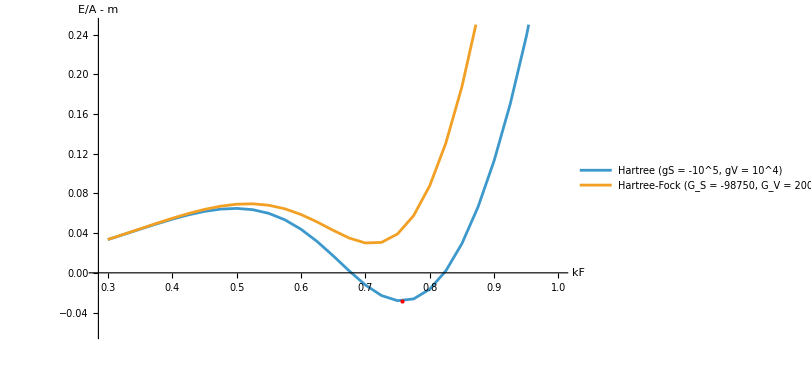

```mathematica
(* energy per particle E/A - m in units of m, Hartree (saturating) and Hartree-Fock *)
eAcurve[g_, gv_] := Table[N[{kF, eps7[g, gv, kF]/rho7[kF] - 1}], {kF, 3/10, 1, 1/40}];
ListLinePlot[{eAcurve[gS0, gV0], eAcurve[GS1, GV1]},
 PlotLegends -> {"Hartree (gS = -10^5, gV = 10^4)", "Hartree-Fock (G_S = -98750, G_V = 20000)"}, AxesLabel -> {"kF", "E/A - m"},
 Epilog -> {Red, PointSize[Medium], Point[{N[kF0], N[eps0/rho0 - 1]}]}, PlotRange -> {-0.06, 0.25}, ImageSize -> 600, GridLines -> {None, {0}}]
```

## 9. The chiral Kohn–Sham theory (8 + 8 components)

### 9.1 Chiral densities

With the chiral components ϕ_kL = EL†.ϕ_k and ϕ_kR = ER†.ϕ_k of the KS orbitals (section 7.10) the 18 densities become one complex scalar density and two 8-currents:

κ = Σ_k ϕ_kL† ϕ_kR,      j_L^A = Σ_k ϕ_kL† σbar^A ϕ_kL,      j_R^A = Σ_k ϕ_kR† σ^A ϕ_kR,

ρS = κ + κ* = 2 Re κ,   ρP = i (κ − κ*) = −2 Im κ,   j^A = j_L^A + j_R^A,   j5^A = j_R^A − j_L^A,

with σ^A = (ID8, σW[i]) and σbar^A = (ID8, −σW[i]) as in section 7.11. The scalar and pseudoscalar densities pair the two chiralities; the currents do not. The sources become a complex scalar source ϖ = s + i p and two chiral vector sources: s ρS + p ρP = ϖ κ + ϖ* κ*,   v_A j^A + a_A j5^A = (v − a)_A j_L^A + (v + a)_A j_R^A.

```mathematica
orbLV = Array[orbL, 8]; orbLcV = Array[orbLc, 8]; orbRV = Array[orbR, 8]; orbRcV = Array[orbRc, 8];   (* phi_L, phi_L^*, phi_R, phi_R^* *)
psiChi = EL.orbLV + ER.orbRV; psiChiDag = orbLcV.ConjugateTranspose[EL] + orbRcV.ConjugateTranspose[ER];
densChi[M_] := Expand[psiChiDag.M.psiChi];
κc = Expand[orbLcV.orbRV]; κcc = Expand[orbRcV.orbLV];                                   (* kappa and kappa^* *)
σUp = Join[{ID8}, Table[σW[i], {i, 1, 7}]]; σbarUp = Join[{ID8}, Table[-σW[i], {i, 1, 7}]];
jLc = Table[Expand[orbLcV.σbarUp[[A + 1]].orbLV], {A, 0, 7}]; jRc = Table[Expand[orbRcV.σUp[[A + 1]].orbRV], {A, 0, 7}];
check["chiral densities: ρS == κ + κ^*, ρP == I(κ - κ^*), j^A == jL^A + jR^A, j5^A == jR^A - jL^A (symbolic chiral orbitals)",
  Expand[densChi[Γ17[0]] - κc - κcc] === 0 && Expand[densChi[Γ17[0].(I χ17)] - I (κc - κcc)] === 0 &&
  And @@ Table[Expand[densChi[Γ17[0].Γ17up[A]] - jLc[[A + 1]] - jRc[[A + 1]]] === 0 &&
    Expand[densChi[Γ17[0].Γ17up[A].χ17] - jRc[[A + 1]] + jLc[[A + 1]]] === 0, {A, 0, 7}]]
check["the chiral blocks behind these densities: EL^†.βD.ER == ID8, EL^†.βD.EL == 0, EL^†.αD[i].EL == -σW[i], ER^†.αD[i].ER == σW[i], EL^†.αD[i].ER == 0",
  ConjugateTranspose[EL].βD.ER == ID8 && ConjugateTranspose[EL].βD.EL == Zero8 &&
  And @@ Table[ConjugateTranspose[EL].αD[i].EL == -σW[i] && ConjugateTranspose[ER].αD[i].ER == σW[i] && ConjugateTranspose[EL].αD[i].ER == Zero8, {i, 1, 7}]]
```

chiral densities: ρS == κ + κ^*, ρP == I(κ - κ^*), j^A == jL^A + jR^A, j5^A == jR^A - jL^A (symbolic chiral orbitals)→True

the chiral blocks behind these densities: EL^†.βD.ER == ID8, EL^†.βD.EL == 0, EL^†.αD[i].EL == -σW[i], ER^†.αD[i].ER == σW[i], EL^†.αD[i].ER == 0→True

### 9.2 The Hartree energy in chiral variables

In chiral variables the Hartree energy density is

e_H = (gS/2)(κ + κ*).b2 − (gP/2)(κ − κ*).b2 + ((gV + gA)/2)(j_L^A j_LA + j_R^A j_RA) + (gV − gA) j_L^A j_RA

= ((gS − gP)/2)(κ.b2 + κ*.b2) + (gS + gP) κ κ* + … .

The scalar–pseudoscalar part depends on κ only through |κ|.b2 exactly when gP = gS; then it is 2 gS |κ|.b2, the Nambu–Jona-Lasinio form. The vector–axial part couples the two currents only through gV − gA.

```mathematica
EHchiAbs[k_, kc_, jl_List, jr_List] := gS/2 (k + kc)^2 - gP/2 (k - kc)^2 +
   (gV + gA)/2 Sum[η17[[A + 1, A + 1]] (jl[[A + 1]]^2 + jr[[A + 1]]^2), {A, 0, 7}] + (gV - gA) Sum[η17[[A + 1, A + 1]] jl[[A + 1]] jr[[A + 1]], {A, 0, 7}];
EHchi = Expand[EHchiAbs[κc, κcc, jLc, jRc]];
check["E_H (16-component form, chiral orbitals) == gS/2 (κ + κ^*)^2 - gP/2 (κ - κ^*)^2 + (gV + gA)/2 (jL.jL + jR.jR) + (gV - gA) jL.jR",
  Expand[EHfun[densChi] - EHchi] === 0]
```

E_H (16-component form, chiral orbitals) == gS/2 (κ + κ^*)^2 - gP/2 (κ - κ^*)^2 + (gV + gA)/2 (jL.jL + jR.jR) + (gV - gA) jL.jR→True

### 9.3 The chiral Kohn–Sham equations

In chiral components the Kohn–Sham equation h_KS ϕ = ϵ ϕ becomes the 8 + 8 block system (W†.h_KS.W):

[V^L_0 − σW[i] (−i ∂_i + V^L_i)] ϕL + M ϕR = ϵ ϕL,

M* ϕL + [V^R_0 + σW[i] (−i ∂_i + V^R_i)] ϕR = ϵ ϕR,

with the complex Kohn–Sham mass M = m + S + i P and the chiral vector potentials V^L_A = V_A − A_A, V^R_A = V_A + A_A. Since σW[i](−i∂_i) = τO[i] ∂_i, the derivative terms contain only the real τO[i], exactly as in section 7.11; the mass M couples the two chiralities. The potentials are Wirtinger derivatives of the energy:

M − m = ϖ + ∂(E_H + E_xc)/∂κ,   V^L_A = (v − a)_A + ∂(E_H + E_xc)/∂j_L^A,   V^R_A = (v + a)_A + ∂(E_H + E_xc)/∂j_R^A;

Hartree:   M − m − ϖ = gS (κ + κ*) − gP (κ − κ*) = gS ρS + i gP ρP,   V^L_A − (v − a)_A = (gV + gA) j_LA + (gV − gA) j_RA,   V^R_A − (v + a)_A = (gV + gA) j_RA + (gV − gA) j_LA.

The densities κ, j_L, j_R are computed from the occupied chiral orbitals (no sea, as in section 8.4), and the total energy is

E = Σ_k ϵ_k − ∫ [ 2 Re((M − m − ϖ) κ) + (V^L − v + a)_A j_L^A + (V^R − v − a)_A j_R^A ] d⁷x + E_H + E_xc.

```mathematica
VLks = VKS - AKS; VRks = VKS + AKS; Mks = mD + Sks + I Pks;
hChiKS[q_List] := ArrayFlatten[{{VLks[[1]] ID8 - Sum[σW[i] (q[[i]] + VLks[[i + 1]]), {i, 1, 7}], Mks ID8},
    {(mD + Sks - I Pks) ID8, VRks[[1]] ID8 + Sum[σW[i] (q[[i]] + VRks[[i + 1]]), {i, 1, 7}]}}];
check["chiral KS Hamiltonian: W^†.h_KS(p).W == {{V^L_0 - σW.(p + V^L), M}, {M^*, V^R_0 + σW.(p + V^R)}}, M = m + S + I P, V^L = V - A, V^R = V + A",
  Expand[ConjugateTranspose[Wch].hKS[pv7].Wch - hChiKS[pv7]] === Zero16]
VLc = Table[(gV + gA) η17[[A + 1, A + 1]] jLc[[A + 1]] + (gV - gA) η17[[A + 1, A + 1]] jRc[[A + 1]], {A, 0, 7}];   (* V^L_A, lower index *)
VRc = Table[(gV + gA) η17[[A + 1, A + 1]] jRc[[A + 1]] + (gV - gA) η17[[A + 1, A + 1]] jLc[[A + 1]], {A, 0, 7}];
dEHdk = gS (κc + κcc) - gP (κc - κcc); dEHdkc = gS (κc + κcc) + gP (κc - κcc);
check["Hartree (Wirtinger): M - m == ∂e_H/∂κ == gS ρS + I gP ρP, V^L_A == ∂e_H/∂jL^A; V^L_A == V_A - A_A and V^R_A == V_A + A_A with V_A = gV j_A, A_A = gA j5_A",
  With[{jlA = Array[jl, 8, 0], jrA = Array[jr, 8, 0]},
    Expand[D[EHchiAbs[kk, kkc, jlA, jrA], kk] - (gS (kk + kkc) - gP (kk - kkc))] === 0 &&
    And @@ Table[Expand[D[EHchiAbs[kk, kkc, jlA, jrA], jl[A]] - ((gV + gA) η17[[A + 1, A + 1]] jl[A] + (gV - gA) η17[[A + 1, A + 1]] jr[A])] === 0, {A, 0, 7}]] &&
  Expand[dEHdk - (gS densChi[Γ17[0]] + I gP densChi[Γ17[0].(I χ17)])] === 0 &&
  And @@ Table[Expand[VLc[[A + 1]] - (gV η17[[A + 1, A + 1]] densChi[Γ17[0].Γ17up[A]] - gA η17[[A + 1, A + 1]] densChi[Γ17[0].Γ17up[A].χ17])] === 0 &&
    Expand[VRc[[A + 1]] - (gV η17[[A + 1, A + 1]] densChi[Γ17[0].Γ17up[A]] + gA η17[[A + 1, A + 1]] densChi[Γ17[0].Γ17up[A].χ17])] === 0, {A, 0, 7}]]
check["chiral KS potentials are derivatives: ∂E_H/∂ϕL^* == (V^L_0 - σW[i] V^L_i) ϕL + (M - m) ϕR and ∂E_H/∂ϕR^* == (V^R_0 + σW[i] V^R_i) ϕR + (M - m)^* ϕL",
  And @@ Table[Expand[D[EHchi, orbLc[a]] - (Sum[VLc[[A + 1]] σbarUp[[A + 1]], {A, 0, 7}].orbLV + dEHdk orbRV)[[a]]] === 0 &&
    Expand[D[EHchi, orbRc[a]] - (Sum[VRc[[A + 1]] σUp[[A + 1]], {A, 0, 7}].orbRV + dEHdkc orbLV)[[a]]] === 0, {a, 1, 8}]]
```

chiral KS Hamiltonian: W^†.h_KS(p).W == {{V^L_0 - σW.(p + V^L), M}, {M^*, V^R_0 + σW.(p + V^R)}}, M = m + S + I P, V^L = V - A, V^R = V + A→True

Hartree (Wirtinger): M - m == ∂e_H/∂κ == gS ρS + I gP ρP, V^L_A == ∂e_H/∂jL^A; V^L_A == V_A - A_A and V^R_A == V_A + A_A with V_A = gV j_A, A_A = gA j5_A→True

chiral KS potentials are derivatives: ∂E_H/∂ϕL^* == (V^L_0 - σW[i] V^L_i) ϕL + (M - m) ϕR and ∂E_H/∂ϕR^* == (V^R_0 + σW[i] V^R_i) ϕR + (M - m)^* ϕL→True

### 9.4 Chiral symmetry

Because χ17 = i ω17, the chiral transformation ψ → e^{iθχ17} ψ = (cos θ ID16 − sin θ ω17) ψ is a REAL rotation of the 16 components. It acts as ϕL → e^{−iθ} ϕL, ϕR → e^{iθ} ϕR and κ → e^{2iθ} κ; the currents j_L and j_R (hence j and j5) are invariant, while (ρS, ρP) rotate by the angle 2θ. Therefore

E_H(e^{iθχ17} ψ) − E_H(ψ) = ((gS − gP)/2) [ (e^{4iθ} − 1) κ.b2 + (e^{−4iθ} − 1) κ*.b2 ]:

the interaction is chirally (U(1)_A) symmetric if and only if gP = gS. The mass term m(κ + κ*) in T_s breaks the symmetry explicitly. For m = 0, gP = gS and ϖ = 0 the whole chiral KS theory is invariant: with κ = 0 the chiral KS equations decouple into separate 8-component equations for ϕL and ϕR, while a self-consistent solution with κ ≠ 0 breaks the symmetry spontaneously (section 9.6). The check uses cos θ = 3/5, sin θ = 4/5.

```mathematica
Uθ = 3/5 ID16 + I 4/5 χ17; e2θ = (3/5 + 4/5 I)^2;
check["e^(Iθχ17) == cosθ ID16 - sinθ ω17 is REAL and orthogonal; U.EL == e^(-Iθ) EL, U.ER == e^(Iθ) ER",
  Uθ == 3/5 ID16 - 4/5 ω17 && FreeQ[Uθ, Complex] && Transpose[Uθ].Uθ == ID16 &&
  Uθ.EL == (3/5 - 4/5 I) EL && Uθ.ER == (3/5 + 4/5 I) ER]
check["U^†.βD.U == βD.(cos 2θ ID16 + I sin 2θ χ17); vector and axial densities invariant",
  ConjugateTranspose[Uθ].βD.Uθ == βD.(Re[e2θ] ID16 + I Im[e2θ] χ17) &&
  And @@ Table[ConjugateTranspose[Uθ].Γ17[0].Γ17up[A].Uθ == Γ17[0].Γ17up[A] &&
    ConjugateTranspose[Uθ].Γ17[0].Γ17up[A].χ17.Uθ == Γ17[0].Γ17up[A].χ17, {A, 0, 7}]]
EHrot = Expand[EHfun[dens16[ConjugateTranspose[Uθ].#.Uθ] &]];
κ16 = dens16[EL.ConjugateTranspose[ER]]; κ16c = dens16[ER.ConjugateTranspose[EL]];
check["E_H(e^(Iθχ17) ψ) - E_H(ψ) == (gS - gP)/2 [(e^(4Iθ) - 1) κ^2 + (e^(-4Iθ) - 1) κ^*2]: U(1)_A symmetric iff gP == gS",
  Expand[EHrot - EH16 - (gS - gP)/2 ((e2θ^2 - 1) κ16^2 + (Conjugate[e2θ]^2 - 1) κ16c^2)] === 0 &&
  Expand[(EHrot - EH16) /. gP -> gS] === 0 && Expand[EHrot - EH16] =!= 0]
```

e^(Iθχ17) == cosθ ID16 - sinθ ω17 is REAL and orthogonal; U.EL == e^(-Iθ) EL, U.ER == e^(Iθ) ER→True

U^†.βD.U == βD.(cos 2θ ID16 + I sin 2θ χ17); vector and axial densities invariant→True

E_H(e^(Iθχ17) ψ) - E_H(ψ) == (gS - gP)/2 [(e^(4Iθ) - 1) κ^2 + (e^(-4Iθ) - 1) κ^*2]: U(1)_A symmetric iff gP == gS→True

### 9.5 Uniform matter in chiral form

For the uniform matter of section 8.7 the chiral densities are κ = ρS/2 (real), j_L^0 = j_R^0 = ρ/2 and j_L^i = j_R^i = 0; the chiral KS potentials are M = m* (real) and V^L_0 = V^R_0 = V_0. The chiral KS Hamiltonian {{V_0 − σW·p⃗, m*}, {m*, V_0 + σW·p⃗}} has the eigenvalues V_0 ± √(p⃗.b2 + m*.b2), each eight times — the spectrum of the 16-component form, as it must be.

```mathematica
kappaUni = Tr[EL.ConjugateTranspose[ER].Runi.Γ17[0]];          (* kappa = tr(EL.ER^dagger.sum psi psi^dagger), sum psi psi^dagger = R.Gamma17[0] *)
jLUni = Table[Tr[EL.σbarUp[[A + 1]].ConjugateTranspose[EL].Runi.Γ17[0]], {A, 0, 7}];
jRUni = Table[Tr[ER.σUp[[A + 1]].ConjugateTranspose[ER].Runi.Γ17[0]], {A, 0, 7}];
check["uniform matter in chiral form: κ == ρS/2, jL^0 == jR^0 == ρ/2, jL^i == jR^i == 0",
  Expand[kappaUni - ρSsym/2] === 0 && Expand[jLUni - Join[{ρsym/2}, ConstantArray[0, 7]]] === ConstantArray[0, 8] &&
  Expand[jRUni - Join[{ρsym/2}, ConstantArray[0, 7]]] === ConstantArray[0, 8]]
hChiUni = ArrayFlatten[{{V0s ID8 - σWp[pv7], mst ID8}, {mst ID8, V0s ID8 + σWp[pv7]}}];
check["(h_χ - V_0)^2 == (p^2 + m*^2) ID16: eigenvalues V_0 ± Sqrt[p^2 + m*^2], eight times each",
  Expand[(hChiUni - V0s ID16).(hChiUni - V0s ID16) - (pv7.pv7 + mst^2) ID16] === Zero16 && Tr[hChiUni - V0s ID16] === 0]
chiralUniform = {"kappa = rhoS/2" -> N[rhoS0/2, 20], "jL^0 = jR^0 = rho/2" -> N[rho0/2, 20], "M = m*" -> N[ms0, 20], "V^L_0 = V^R_0 = V0" -> N[V00, 20]}
```

uniform matter in chiral form: κ == ρS/2, jL^0 == jR^0 == ρ/2, jL^i == jR^i == 0→True

(h_χ - V_0)^2 == (p^2 + m*^2) ID16: eigenvalues V_0 ± Sqrt[p^2 + m*^2], eight times each→True

{kappa = rhoS/2→3.2595132992687836743×10^-6,jL^0 = jR^0 = rho/2→6.9405010661584385987×10^-6,M = m*→0.34809734014624326514,V^L_0 = V^R_0 = V0→0.13881002132316877197}

### 9.6 The chiral vacuum with the Dirac sea: spontaneous chiral symmetry breaking

Now keep the Dirac sea — all negative-energy KS orbitals occupied, with a momentum cutoff |p⃗| < Λ — and take gP = gS = g, ϖ = 0, V = A = 0 and no matter (the vacuum). With a uniform complex KS mass M the chiral KS Hamiltonian h_χ(p⃗) = {{−σW·p⃗, M ID8}, {M* ID8, σW·p⃗}} (plus m on the off-diagonal blocks when m ≠ 0, absorbed in M) satisfies h_χ.b2 = (p⃗.b2 + |M|.b2) ID16. Its eigenvalues are ±E, E = √(p⃗.b2 + |M|.b2), and the projector on the filled sea is Π−(p⃗) = (ID16 − h_χ(p⃗)/E)/2, whose RL block is −M*/(2E) ID8. Hence

κ = −4 M* J(|M|),   J(M) = ∫_{|p⃗|<Λ} d⁷p/(2π)⁷ 1/√(p.b2 + M.b2) = (1/(120 π⁴)) ∫_0^Λ p⁶/√(p.b2 + M.b2) dp

(the angular integral gives |S⁶|/(2π)⁷ = 1/(120 π⁴)). The Hartree KS mass M = m + 2g κ* gives the gap equation

M = m − 8 g J(|M|) M.

For m = 0 a solution M ≠ 0 exists if and only if 1 + 8 g J(|M|) = 0 has a root, i.e. iff g < g_c = −1/(8 J(0)) = −90 π⁴/Λ⁶. The vacuum energy density of the KS state (sum of the sea eigenvalues minus double counting) is

E(M) = −8 K(|M|) + 8 J(|M|) Re[(M − m) M*] + 32 g |M|.b2 J(|M|).b2,   K(M) = (1/(120 π⁴)) ∫_0^Λ p⁶ √(p.b2 + M.b2) dp,

and its stationarity condition is the gap equation (for m = 0: dE/d|M| = 8|M| (1 + 8gJ)(J + |M| J′)). For m = 0, E depends only on |M|: the broken vacua M = |M| e^{iϕ} are degenerate and related by chiral rotations; the phase ϕ is the Goldstone direction. A small explicit mass m > 0 selects the real positive M. Example: Λ = 1, g = (6/5) g_c; for m > 0, m = 1/100.

```mathematica
Λc = 1;
Jsea[M_] = Integrate[q^6/Sqrt[q^2 + M^2], {q, 0, Λc}, Assumptions -> M > 0]/(120 Pi^4);
Ksea[M_] = Integrate[q^6 Sqrt[q^2 + M^2], {q, 0, Λc}, Assumptions -> M > 0]/(120 Pi^4);
J0sea = Integrate[q^5, {q, 0, Λc}]/(120 Pi^4); K0sea = Integrate[q^7, {q, 0, Λc}]/(120 Pi^4);
gcrit = -1/(8 J0sea);
check["|S^6|/(2 Pi)^7 == 1/(120 Pi^4); J(0) == Λ^6/(720 Pi^4); g_c == -1/(8 J(0)) == -90 Pi^4/Λ^6; J(M) -> J(0) and K(M) -> K(0) as M -> 0",
  (16 Pi^3/15)/(2 Pi)^7 == 1/(120 Pi^4) && J0sea == 1/(720 Pi^4) && gcrit == -90 Pi^4 &&
  Limit[Jsea[M], M -> 0, Direction -> "FromAbove"] == J0sea && Limit[Ksea[M], M -> 0, Direction -> "FromAbove"] == K0sea]
Esea[Mz_, mq_, g_] := -8 Ksea[Abs[Mz]] + 8 Jsea[Abs[Mz]] Re[(Mz - mq) Conjugate[Mz]] + 32 g Abs[Mz]^2 Jsea[Abs[Mz]]^2;
E0sea = -8 K0sea;                                              (* E(M = 0), m = 0 *)
gNJL = 6/5 gcrit;
gapNJL[M_?NumericQ, mq_] := With[{M1 = SetPrecision[M, 60]}, M1 - mq + 8 gNJL Jsea[M1] M1];     (* M - m + 8 g J(M) M, real M > 0 *)
M0NJL = SetPrecision[M /. FindRoot[gapNJL[M, 0]/M, {M, 1/10, 1}, Method -> "Brent", WorkingPrecision -> 40, AccuracyGoal -> 32, PrecisionGoal -> 32], 60];
check["m = 0, g = 6/5 g_c: the gap equation 1 + 8 g J(|M|) == 0 has the root |M| (32 digits); M == 2 g κ^* with κ == -4 M J; E is stationary there and lower than E(0)",
  Abs[1 + 8 gNJL Jsea[M0NJL]] < 10^-25 && Abs[M0NJL - 2 gNJL (-4 M0NJL Jsea[M0NJL])] < 10^-25 &&
  Abs[D[-8 Ksea[M] + 8 Jsea[M] M^2 + 32 gNJL M^2 Jsea[M]^2, M] /. M -> M0NJL] < 10^-25 && Esea[M0NJL, 0, gNJL] < E0sea]
check["degenerate chiral vacua for m = 0: E(|M| e^(I φ)) == E(|M|) for φ = 1, 2, 4 (the phase is the Goldstone direction)",
  And @@ Table[Abs[Esea[M0NJL Exp[I phi], 0, gNJL] - Esea[M0NJL, 0, gNJL]] < 10^-25, {phi, {1, 2, 4}}]]
mq0 = 1/100;
MmNJL = SetPrecision[M /. FindRoot[gapNJL[M, mq0], {M, 1/10, 1}, Method -> "Brent", WorkingPrecision -> 40, AccuracyGoal -> 32, PrecisionGoal -> 32], 60];
check["explicit breaking m = 1/100: the real M == m - 8 g J(M) M solves the gap equation, E is stationary there, and every complex phase raises E",
  Abs[MmNJL - mq0 + 8 gNJL Jsea[MmNJL] MmNJL] < 10^-25 && Abs[D[-8 Ksea[M] + 8 Jsea[M] (M^2 - mq0 M) + 32 gNJL M^2 Jsea[M]^2, M] /. M -> MmNJL] < 10^-25 &&
  And @@ Table[Esea[MmNJL Exp[I phi], mq0, gNJL] > Esea[MmNJL, mq0, gNJL], {phi, {1/50, 1/2, 1, 3}}]]
njlVacuum = {"g_c" -> N[gcrit, 20], "g" -> N[gNJL, 20], "|M| (m = 0)" -> N[M0NJL, 20], "kappa (m = 0, M real)" -> N[-4 M0NJL Jsea[M0NJL], 20],
  "E(M) - E(0)" -> N[Esea[M0NJL, 0, gNJL] - E0sea, 20], "M (m = 1/100)" -> N[MmNJL, 20]}
```

|S^6|/(2 Pi)^7 == 1/(120 Pi^4); J(0) == Λ^6/(720 Pi^4); g_c == -1/(8 J(0)) == -90 Pi^4/Λ^6; J(M) -> J(0) and K(M) -> K(0) as M -> 0→True

m = 0, g = 6/5 g_c: the gap equation 1 + 8 g J(|M|) == 0 has the root |M| (32 digits); M == 2 g κ^* with κ == -4 M J; E is stationary there and lower than E(0)→True

degenerate chiral vacua for m = 0: E(|M| e^(I φ)) == E(|M|) for φ = 1, 2, 4 (the phase is the Goldstone direction)→True

explicit breaking m = 1/100: the real M == m - 8 g J(M) M solves the gap equation, E is stationary there, and every complex phase raises E→True

{g_c→-8766.8181930602193513,g→-10520.181831672263222,|M| (m = 0)→0.55369385182924169122,kappa (m = 0, M real)→-0.0000263157928583648742,E(M) - E(0)→-1.3102449629010022473×10^-6,M (m = 1/100)→0.58531284674622051123}

the sea at one momentum: h_χ^2 == E^2 ID16; Π_- is a projector of rank 8; κ_p == tr(Π_- RL block) == -4 M^*/E; tr(Π_-.h0) == -8E + 8 Re[(M - m) M^*]/E→True

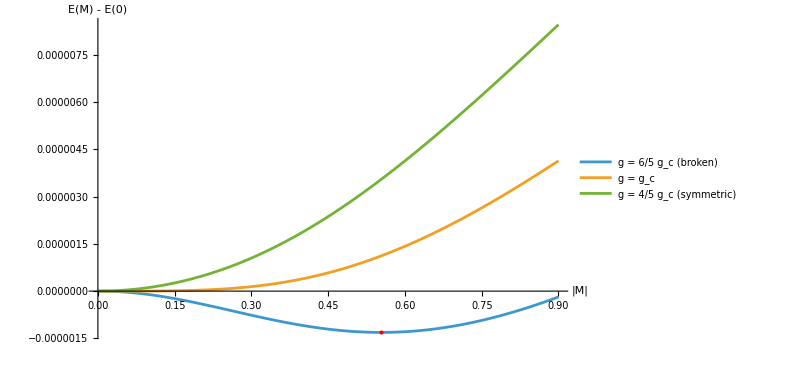

```mathematica
(* the filled sea at one momentum, with a complex M: an explicit check of kappa_p and of the sea energy *)
pS = {3/10, -1/5, 1/10, 1/4, 0, -3/20, 1/20}; Mz7 = M0NJL Exp[7 I/10];
hChiSea = ArrayFlatten[{{-σWp[pS], Mz7 ID8}, {Conjugate[Mz7] ID8, σWp[pS]}}];
Esp = Sqrt[pS.pS + Abs[Mz7]^2]; PiMinus = (ID16 - hChiSea/Esp)/2;
h0Chi = ArrayFlatten[{{-σWp[pS], Zero8}, {Zero8, σWp[pS]}}];       (* m = 0 *)
check["the sea at one momentum: h_χ^2 == E^2 ID16; Π_- is a projector of rank 8; κ_p == tr(Π_- RL block) == -4 M^*/E; tr(Π_-.h0) == -8E + 8 Re[(M - m) M^*]/E",
  Max[Abs[hChiSea.hChiSea - Esp^2 ID16]] < 10^-20 && Max[Abs[PiMinus.PiMinus - PiMinus]] < 10^-20 && Abs[Tr[PiMinus] - 8] < 10^-20 &&
  Abs[Tr[PiMinus[[9 ;; 16, 1 ;; 8]]] + 4 Conjugate[Mz7]/Esp] < 10^-20 && Abs[Tr[PiMinus.h0Chi] - (-8 Esp + 8 Abs[Mz7]^2/Esp)] < 10^-20]
Plot[{Esea[Mx, 0, gNJL] - E0sea, Esea[Mx, 0, gcrit] - E0sea, Esea[Mx, 0, 4/5 gcrit] - E0sea}, {Mx, 0.001, 0.9},
 PlotLegends -> {"g = 6/5 g_c (broken)", "g = g_c", "g = 4/5 g_c (symmetric)"}, AxesLabel -> {"|M|", "E(M) - E(0)"},
 Epilog -> {Red, PointSize[Medium], Point[{N[M0NJL], N[Esea[M0NJL, 0, gNJL] - E0sea]}]}, ImageSize -> 600]
```

## 10. Summary of all checks (sections 1–9)

The four cells below repeat the summary of section 6 after sections 7–9 have been evaluated, so they cover every check of the notebook.

```mathematica
Length[checks]
```

202

```mathematica
failedChecks = Keys[Select[checks, ! TrueQ[#] &]]
```

{}

```mathematica
allChecksPassed = AllTrue[Values[checks], TrueQ]
```

True

```mathematica
Grid[Prepend[KeyValueMap[{#1, #2} &, checks], {Style["check", Bold], Style["result", Bold]}], Frame -> All, Alignment -> Left]
```

check | result
4+4: ζ[7] == diag(-1,-1,-1,-1,1,1,1,1) | True
4+4: σ == ζ[1].ζ[2].ζ[3] | True
4+4: (ζ[A].ζ[B] + ζ[B].ζ[A])/2 == -η4488[[A+1,B+1]] ID8 (A,B = 1..7) | True
4+4: -η4488[[A+1,A+1]] ζ[A] == Transpose[ζ[A]] (A = 1..7) | True
4+4: (τ[A].τbar[B] + τ[B].τbar[A])/2 == η4488[[A+1,B+1]] ID8 | True
4+4: (τbar[A].τ[B] + τbar[B].τ[A])/2 == η4488[[A+1,B+1]] ID8 | True
4+4: τ[1].τ[2]...τ[7] == ID8 | True
4+4: σ == τ[1].τ[2].τ[3] == τ[4].τ[5].τ[6].τ[7] | True
4+4: σ commutes with τ[1..3] and anticommutes with τ[4..7]; σ.σ == ID8 | True
4+4: (T16[A].T16[B] + T16[B].T16[A])/2 == η4488[[A+1,B+1]] ID16 | True
4+4: T16[A] real (entries 0, ±1) | True
4+4: T16[8] == diag(-ID8, ID8) | True
4+4: σ16 == diag(-σ, σ) | True
4+4: PL44 + PR44 == ID16, PL44.PL44 == PL44, PR44.PR44 == PR44, PL44.PR44 == 0 | True
4+4: uBasis == evecs/Sqrt[2] from Eigensystem[σ] (the basis of 4+4.nb) | True
4+4: unit == (1,0,0,0,1,0,0,0)/Sqrt[2], σ.unit == unit, unit.unit == 1, unit.σ.unit == 1 | True
4+4 (In[294]): E44inv[h] == (u.σ.u) Transpose[Table[η4488[[B,B]] τ[B-1].u, {B,1,8}]] for h = 1..8 | True
4+4: gridx44 is identical to the split-octonion table printed by 4+4.nb | True
4+4: LS[A] are signed permutation matrices (constants 0, ±1) | True
split: eA[1] is the identity; eA[2..4]^2 == -eA[1]; eA[5..8]^2 == +eA[1] | True
split: x x̄ == N(x) eA[1] with N = η4488 (symbolic) | True
split: N(xy) == N(x) N(y) (symbolic) | True
split: alternative x(xy) == (xx)y and (yx)x == y(xx) (symbolic) | True
split: (eA[1] + eA[5])(eA[1] - eA[5]) == 0 with both factors nonzero: NOT a division algebra | True
τO[A] (A = 1..7): real, antisymmetric, τO[A].τO[A] == -ID8 | True
τO[A] anticommute: τO[A].τO[B] == -τO[B].τO[A] (A != B, A,B = 1..7) | True
mirror of 4+4: (τO[A].τObar[B] + τO[B].τObar[A])/2 == gO[[A+1,B+1]] ID8 | True
mirror of 4+4: (τObar[A].τO[B] + τObar[B].τO[A])/2 == gO[[A+1,B+1]] ID8 | True
mirror of 4+4: τO[1].τO[2]...τO[7] == ID8 | True
mirror of 4+4: τObar[A] == gO.Transpose[τO[A]].gO, as τbar[A] == σ.Transpose[τ[A]].σ | True
τO[4..7] are products of three split τ: τO[4] == τ[5].τ[6].τ[7], τO[5] == -τ[4].τ[6].τ[7], τO[6] == τ[4].τ[5].τ[7], τO[7] == -τ[4].τ[5].τ[6] | True
σ.unit == unit, hence τO[A].unit == τ[A].unit (A = 0..7) | True
EO is orthogonal: EOinv == Transpose[EO] | True
mirror of 4+4.nb In[294]: EOinv == (u.gO.u) Transpose[Table[gO[[B,B]] τO[B-1].u, {B,1,8}]] | True
EO == η4488.E44[hUSE]: the two vielbeins differ only by the signs of rows 5..8 | True
gridO equals the octonion table computed independently in Python | True
LO[A] are signed permutation matrices (all multiplication constants are 0, ±1) | True
oMul reproduces gridO on all 64 pairs of basis units | True
e[0] is a two-sided identity | True
e[i] e[i] == -e[0] (i = 1..7) | True
e[i] e[j] == -e[j] e[i] (i != j, i,j = 1..7): non-commutative | True
7 Fano lines; every pair of distinct imaginary units lies on exactly one line | True
each oriented line (a,b,c) is cyclic: e[a]e[b] == e[c], e[b]e[c] == e[a], e[c]e[a] == e[b] | True
each line spans a quaternion subalgebra: {e[0], e[a], e[b], e[c]} closed and associative | True
the picture's 7 lines are exactly fanoLines | True
left alternative: x(xy) == (xx)y (symbolic) | True
right alternative: (yx)x == y(xx) (symbolic) | True
flexible: (xy)x == x(yx) (symbolic) | True
associator is alternating: [x,y,z] == -[y,x,z] == -[x,z,y] (symbolic) | True
power associativity: x(xx) == (xx)x (symbolic) | True
Moufang: z(x(zy)) == ((zx)z)y, x(z(yz)) == ((xz)y)z, (zx)(yz) == (z(xy))z (x, y basis units, z symbolic) | True
x x̄ == x̄ x == N(x) e[0] (symbolic) | True
conjugation is an anti-automorphism: conj(xy) == conj(y) conj(x) (symbolic) | True
Re(x) == (x + x̄)/2 == x0 | True
norm is multiplicative: N(xy) == N(x) N(y) (symbolic; Degen's eight-square identity) | True
inverse x^-1 = x̄/N(x): x x^-1 == x^-1 x == e[0] (symbolic) | True
every x satisfies x x - 2 Re(x) x + N(x) e[0] == 0, so the subalgebra generated by x is ℝ or ℂ | True
exactly 168 of the 512 ordered basis triples are non-associative (= 7*6*4: distinct imaginary units not on one Fano line) | True
example: (e[1]e[2])e[4] == e[7] but e[1](e[2]e[4]) == -e[7] | True
numerical example: N(x y) == N(x) N(y) == 15*6 == 90 and x x^-1 == e[0] | True
numerical example: x y != y x and (x y) z != x (y z) | True
ℍ = span{e[0],e[1],e[2],e[3]} is a subalgebra | True
ℓ = e[4] doubles ℍ: e[4] e[k] == e[4+k] (k = 1,2,3) and e[4] e[4] == -e[0] | True
orientation inherited from 4+4.nb: e[1] e[2] == -e[3] | True
Cayley-Dickson, γ = -1: (ac - d b̄, ā d + c b) reproduces the octonion product (symbolic) | True
Cayley-Dickson, γ = +1: (ac + d b̄, ā d + c b) reproduces the SPLIT product of 4+4.nb (symbolic) | True
the formula (ac - d̄ b, ā d + c b) of [1A] is NOT alternative: x·x·y != x(xy) for x = e[0]+e[4], y = e[1] | True
... and its norm is not multiplicative (symbolic) | True
e[A]e[B] (octonion) == s_AB e[A]e[B] (split) for all A, B = 0..7 | True
over ℂ: φ(x *split y) == φ(x) *oct φ(y) (symbolic): split ⊗ ℂ ≅ 𝕆 ⊗ ℂ | True
the norms correspond: N_oct(φ(x)) == N_split(x) (symbolic) | True
Cl(8,0): (T16O[A].T16O[B] + T16O[B].T16O[A])/2 == gO[[A+1,B+1]] ID16 | True
S44 == diag(σ, σ) | True
T16O from the 4+4 matrices: T16O[A] == T16[A] (A = 0..3), T16O[k] == T16[k].S44 (k = 4..7) | True
T16O[8] == T16[8] == diag(-ID8, ID8): same chirality matrix and same PL44, PR44 as 4+4.nb | True
7+1 REAL Clifford relation: (Γ17[A].Γ17[B] + Γ17[B].Γ17[A])/2 == η17[[A+1,B+1]] ID16 == -η71[[A+1,B+1]] ID16 | True
Γ17[A] are REAL: every entry is 0 or ±1 | True
block form: Γ17[0] == {{0,ID8},{ID8,0}}, Γ17[i] == {{τO[i],0},{0,τObar[i]}} | True
built from the real 4+4 matrices: Γ17[0] == T16[0], Γ17[i] == T16[0].T16[i] (i = 1,2,3), Γ17[k] == T16[0].T16[k].S44 (k = 4..7) | True
Γ17[0] symmetric, Γ17[i] antisymmetric, so Transpose[Γ17[A]] == Γ17[0].Γ17[A].Γ17[0] (real Dirac adjoint) | True
the 256 products Γ17[A1]...Γ17[Ak] (A1 < ... < Ak) are linearly independent: Cl(1,7) ≅ ℝ(16) | True
grades: binomial(8,k) == {1,8,28,56,70,56,28,8,1}, total 256 (binomial(8,4) == 70, not 72) | True
Tr[product] == 0 for every non-empty product, so Tr[M]/16 is the scalar part of M | True
irreducible over ℝ: only multiples of ID16 commute with all Γ17[A] (Schur; real commutant of dimension 1) | True
universal property: Γ17(v).Γ17(v) == (v.η17.v) ID16 for a symbolic vector v = X | True
7+1 COMPLEX Clifford relation, 4+4.nb sign: (Γ71[A].Γ71[B] + Γ71[B].Γ71[A])/2 == η71[[A+1,B+1]] ID16 | True
Γ71[0] == I T16[0] and Γ71[k] == T16O[k] (k = 1..7): only the time component is complex | True
S = (ID16 - I Γ17[0])/Sqrt[2] is unitary and Γ71[A] == S.(I Γ17[A]).Inverse[S] | True
Schur: the intertwiners M with M.Conjugate[Γ71[A]] == Γ71[A].M form a 1-dimensional space | True
... spanned by the volume element Γ17[8] == {{0,-ID8},{ID8,0}}, and Γ17[8].Γ17[8] == -ID16 | True
indicator(Γ71) == -1: Cl(7,1) ≅ ℍ(8), NO real 16×16 realization of the η71 relation | True
indicator(Γ17) == +1: Cl(1,7) ≅ ℝ(16), real realization exists (Γ17) | True
REAL 32×32 realization of the η71 relation: (Γ71R32[A].Γ71R32[B] + Γ71R32[B].Γ71R32[A])/2 == η71[[A+1,B+1]] ID32 | True
Qi, Qj, Qk commute with every Γ71R32[A]; Qi.Qi == Qj.Qj == Qk.Qk == -ID32; Qi.Qj == Qk == -Qj.Qi | True
the commutant of {Γ71R32[A]} has dimension exactly 4 and is spanned by ID32, Qi, Qj, Qk: it is ℍ | True
Γ17[8].Γ17[8] == -ID16 and Γ17[8] anticommutes with every Γ17[A]: no real chirality in 7+1 | True
Γ71[8].Γ71[8] == -ID16 and χ71 = -I Γ71[8] == T16O[8] == T16[8] (real, diagonal) | True
7+1 chiral projectors in the Γ71 basis are exactly PL44, PR44 of 4+4.nb; χ71 anticommutes with every Γ71[A] | True
complex chiral projectors for Γ17: PL17 + PR17 == ID16, PL17.PL17 == PL17, PL17.PR17 == 0, rank 8 each | True
Re(x x) == X.η17.X: the octonion square produces the 7+1 interval (symbolic) | True
octonion basis: Γ17e[0] == {{0,ID8},{ID8,0}} and Γ17e[i] == {{LO[i],0},{0,-LO[i]}} | True
alternativity in action: xImag(xImag ψ) == -|xImag|^2 ψ for the imaginary part xImag of x (symbolic) | True
T16O(x)^2 == N(x) ID16 (octonion norm) and T16(x)^2 == (X.η4488.X) ID16 (4+4.nb) | True
28 real generators Σ17[A,B] (A < B), linearly independent | True
[Σ17[A,B], Γ17[K]] == η17[[B+1,K+1]] Γ17[A] - η17[[A+1,K+1]] Γ17[B] | True
so(1,7): [Σ_AB, Σ_KL] == η_BK Σ_AL - η_AK Σ_BL - η_BL Σ_AK + η_AL Σ_BK | True
the complex structure J = Γ17[8] commutes with all Σ17[A,B] (Spin(1,7) acts complex-linearly on ℝ^16 = ℂ^8) | True
S(β) and R(θ) are the exponentials: dS/dβ == Σ17[0,1].S, S(0) == ID16, dR/dθ == Σ17[4,5].R, R(0) == ID16, and S.Sinv == R.Rinv == ID16 | True
S(β).Γ17[K].S(β)^-1 == ∑_B Λboost[[B+1,K+1]] Γ17[B]; Λboost is the boost along x1 | True
R(θ).Γ17[K].R(θ)^-1 == ∑_B Λrot[[B+1,K+1]] Γ17[B]; Λrot is the rotation in the x4-x5 plane | True
both Λ preserve the 7+1 metric: Transpose[Λ].η17.Λ == η17 | True
(Γ17^A ∂_A)^2 Ψ == (∂0^2 - ∂1^2 - ... - ∂7^2) Ψ for 16 arbitrary functions of x0..x7 | True
p is on the mass shell (p.η17.p == m^2) and pslash.pslash == m^2 ID16 | True
(pslash - m) w == 0 has 8 linearly independent REAL solutions w | True
Ψ = w Exp[-I p.x] solves (I Γ17^A ∂_A - m) Ψ == 0 | True
the matrices anticommuting with every Γ17[A] are exactly the multiples of Γ17[8], and (c Γ17[8])^2 == -c^2 ID16: no real J with J.J == +ID16 | True
null momentum k = (1,1,0,0,0,0,0,0): k.η17.k == 0, kslash.kslash == 0, and kslash.w == 0 has 8 REAL solutions | True
Ψ = w Cos[k.x] is a REAL solution of the real massless Dirac equation Γ17^A ∂_A Ψ == 0 | True
(Γ71R32^A ∂_A)^2 Ψ == -(∂0^2 - ∂1^2 - ... - ∂7^2) Ψ for 32 arbitrary functions of x0..x7 | True
p.η71.p == -m^2 and pslash32.pslash32 == -m^2 ID32 | True
Ψ = w Cos[p.x] + (pslash32.w/m) Sin[p.x], with 32 arbitrary REAL constants w, solves the REAL massive equation (Γ71R32^A ∂_A - m) Ψ == 0 | True
... and Ψ obeys the Klein-Gordon equation (∂0^2 - ∂1^2 - ... - ∂7^2 + m^2) Ψ == 0 | True
split analogue: Re(x x) of split octonions == X.η53.X, and Γ53 realizes Cl(5,3) with REAL 16×16 matrices | True
Γ08[A] = T16O[8].T16O[A] realizes Cl(0,8) with REAL 16×16 matrices | True
gens[p] satisfy the Clifford relation of signature (p, 8-p) for p = 0..8 | True
classification: ℝ(16) for (8,0),(5,3),(4,4),(1,7),(0,8); ℍ(8) for (7,1),(6,2),(3,5),(2,6) | True
every ℝ(16) case has explicit REAL 16×16 generators in this notebook (T16O, Γ53, T16, Γ17, Γ08) | True
ℂ(16) cannot occur: its real dimension 2*16^2 = 512 differs from 2^8 = 256 | True
Dirac matrices: Γ17up[0] == Γ17[0], Γ17up[i] == -Γ17[i]; all REAL, every entry 0 or ±1 | True
Dirac adjoint: ConjugateTranspose[Γ17up[A]] == Γ17[0].Γ17up[A].Γ17[0] for A = 0..7 | True
βD == {{0,ID8},{ID8,0}} and αD[i] == {{0,τO[i]},{-τO[i],0}}: real and symmetric | True
αD[i].αD[j] + αD[j].αD[i] == 2 δij ID16, αD[i].βD + βD.αD[i] == 0, βD.βD == ID16 | True
ω17 = Γ17[8] == {{0,-ID8},{ID8,0}} is real, ω17.ω17 == -ID16, and ω17 anticommutes with every Γ17[A] | True
(I Γ17up[A] ∂_A + m)(I Γ17up[A] ∂_A - m) dirac16complex == -(∂0^2 - ∂1^2 - ... - ∂7^2 + m^2) dirac16complex (16 arbitrary functions) | True
Γ17[0].(I Γ17up[A] ∂_A - m) ψ == I ∂0 ψ - h ψ with h = -I αD[i] ∂_i + βD m (16 arbitrary functions) | True
h(p) == {{0, M}, {Transpose[M], 0}} with the REAL 8×8 matrix M = m ID8 + p_i τO[i] | True
M.Transpose[M] == Transpose[M].M == E^2 ID8 and h(p).h(p) == E^2 ID16, E^2 = m^2 + p^2 | True
h(p).u_s == E u_s and h(-p).v_s == -E v_s for s = 1..8 | True
(pslash - m).u_s == 0 and (pslash + m).v_s == 0, pslash = E Γ17[0] + p_i Γ17[i] | True
u_s.u_r == v_s.v_r == 2E δsr, and u_s(p).v_r(-p) == 0 | True
plane waves: u_s Exp[-I(E x0 - p.x)] and v_s Exp[+I(E x0 - p.x)] solve (I Γ17up[A] ∂_A - m) ψ == 0 | True
example p = (2,2,4,0,0,0,0), m = 1: E = 5 and the eight u_s are real (entries in Sqrt[5] ℚ) and solve h(p).u_s == 5 u_s | True
spin sums: ∑_s u_s ubar_s == pslash + m and ∑_s v_s vbar_s == pslash - m | True
completeness: ∑_s u_s(p) u_s(p)^T + ∑_s v_s(-p) v_s(-p)^T == 2E ID16 | True
U = (u_1..u_8, v_1(-p)..v_8(-p))/Sqrt[2E] is orthogonal and Transpose[U].h(p).U == diag(E ID8, -E ID8) | True
Grassmann: θ1 θ2 == -θ2 θ1, θ1 θ1 == 0, associativity, and ∂/∂θ2 (θ1 θ2 θ3) == -θ1 θ3 | True
the three plane waves U1, U2, U3 solve the Dirac equation with m = 1 | True
Grassmann field: ψ_a ψ_b + ψ_b ψ_a == 0 for all a, b (in particular ψ_a^2 == 0) | True
current conservation ∂_A (ψbar Γ17up[A] ψ) == 0 for the Grassmann-valued solution ψ = θ1 U1 + θ2 U2 + θ3 U3 | True
canonical anticommutator from the mode algebra: {ψ_a(x0,x), ψ_b(x0,y)^†} == δab (1/V) ∑_p Exp[I p.(x - y)] (five momenta, symbolic x, y) | True
ψ -> ψc = ω17.ψ^*: (I Γ17up[A] ∂_A - m)(ω17.ψ^*) == ω17.((I Γ17up[A] ∂_A - m) ψ)^* for arbitrary ψ = ψre + I ψim | True
(pslash + m).ω17.u_s == 0 and ω17.u_s == ∑_r v_r (-Transpose[M]/E)_rs; ω17.ω17 == -ID16 (no Majorana spinors) | True
boost at β = 2 log 2: S == 5/4 ID16 + 3/4 Γ17[0].Γ17[1], p' = Λ.p == (55/8, -41/8, 2, 4, 0, 0, 0, 0) is on shell, (pslash' - m).S.u_s(p) == 0 | True
χ17 = I ω17: Hermitian, χ17.χ17 == ID16, anticommutes with every Γ17[A], commutes with every Σ17[A,B] | True
PL17, PR17 are complex (not real); Γ17[A].PL17 == PR17.Γ17[A]; ConjugateTranspose[PL17].Γ17[0] == Γ17[0].PR17 | True
EL, ER: χ17.EL == -EL, χ17.ER == ER, EL^†.EL == ER^†.ER == ID8, EL^†.ER == 0, EL.EL^† == PL17, ER.ER^† == PR17, W unitary | True
ϕL == (ψup + I ψdown)/Sqrt[2], ϕR == (I ψup + ψdown)/Sqrt[2], PL17.ψ == EL.ϕL, PR17.ψ == ER.ϕR, ψ == EL.ϕL + ER.ϕR | True
σW[i] = I τO[i]: Hermitian, σW[i].σW[j] + σW[j].σW[i] == 2 δij ID8 | True
chiral (Weyl) form: W^†.h(p).W == {{-σW.p, m ID8}, {m ID8, σW.p}} (symbolic p) | True
EL^†.Γ17[0].(I Γ17up[A] ∂_A - m) ψ == (I ∂0 + τO[i] ∂_i) ϕL - m ϕR (16 arbitrary functions) | True
ER^†.Γ17[0].(I Γ17up[A] ∂_A - m) ψ == (I ∂0 - τO[i] ∂_i) ϕR - m ϕL (16 arbitrary functions) | True
Klein-Gordon for each 8-component field: (I ∂0 - τO[i] ∂_i)(I ∂0 + τO[j] ∂_j) f == -(∂0^2 - ∂1^2 - ... - ∂7^2) f (8 arbitrary functions) | True
plane-wave example p = (2,2,4,0,0,0,0), m = 1, E = 5: (E + σW.p) ϕL == m ϕR and (E - σW.p) ϕR == m ϕL for all eight u_s | True
the densities ρS, ρP, j^A, j5^A are real: Γ17[0].op is Hermitian for op = ID16, I χ17, Γ17up[A], Γ17up[A].χ17 | True
18 vertex pairs; lower vertex == η17[[A+1,A+1]] upper vertex in the V and A channels | True
nonlinear field equation: left derivative ∂L_int/∂ψbar_a == -[gS (ψbar ψ) ψ + gP (ψbar Iχ17 ψ) Iχ17 ψ + gV (ψbar Γ17[A] ψ) Γ17up[A] ψ + gA (ψbar Γ17[A]χ17 ψ) Γ17up[A]χ17 ψ]_a (32 Grassmann generators) | True
h_KS(p) is Hermitian for real S, P, V_A, A_A (symbolic momentum and potentials) | True
plane wave: Γ17[0].(pslash(ϵ,p) - m - S - I χ17 P - Γ17up[A](V_A + χ17 A_A)) == ϵ ID16 - h_KS(p) | True
Hartree potentials: ∂E_H/∂ϕ_a^* == (v_H.ϕ)_a, v_H = h_KS - h with S = gS ρS, P = gP ρP, V_A = gV j_A, A_A = gA j5_A (32 variables) | True
Wick's theorem in the 560-dimensional Fock space: <Φ| :(ψbar o1 ψ)(ψbar o2 ψ): |Φ> == tr(o1 R) tr(o2 R) - tr(o1 R o2 R) for all 18 vertex pairs | True
exchange self-energy: d/dt E_x(R + t dR) at t = 0 == tr(Σ_x.dR) and E_x == tr(Σ_x.R)/2 (random complex R, dR; symbolic couplings) | True
the 256 products Γ_K are orthogonal matrices with tr(Inverse[Γ_K].Γ_L) == 16 δKL | True
Fierz completeness: ∑_K (Γ_K)_ab (Inverse[Γ_K])_cd == 16 δad δcb (as the 256×256 matrix identity Transpose[F].F == 16 ID) | True
Fierz rearrangement of every exchange term: tr(o1 R o2 R) == (1/16) ∑_K tr(Inverse[Γ_K].R) tr(o1.Γ_K.o2.R) for all 18 vertex pairs (random complex R) | True
uniform matter: tr R == ρS, tr(Γ17up[0].R) == ρ, and the densities ρP, j^i, j5^A vanish | True
the occupied plane waves give this R: (1/2) ∑_s [u_s(p) ubar_s(p) + u_s(-p) ubar_s(-p)]/(2E) == (E Γ17[0] + m ID16)/(2E) | True
uniform exchange energy: E_x(R) == -gS/32 (ρS^2 + ρ^2) + gP/32 (ρS^2 - ρ^2) - gV/32 (8ρS^2 - 6ρ^2) + gA/32 (8ρS^2 + 6ρ^2) | True
uniform exchange self-energy: Σ_x == S_x ID16 + V_x Γ17[0] with S_x == ∂E_x/∂ρS and V_x == ∂E_x/∂ρ | True
uniform Hartree-Fock == Hartree with the Fierz-transformed couplings: gS/2 ρS^2 + gV/2 ρ^2 + E_x == G_S/2 ρS^2 + G_V/2 ρ^2 (gP, gA arbitrary) | True
c7 == 8 |S^6|/(2 Pi)^7 == 1/(15 Pi^4), |S^6| == 2 Pi^(7/2)/Gamma[7/2] == 16 Pi^3/15, and ρ == c7 kF^7/7 == kF^7/(105 Pi^4) | True
closed forms: d/dkF of the integrals gives the integrands, both vanish at kF = 0, and dϵ_kin/dm* == ρS | True
Hartree gap equation m* == m + gS ρS(m*) solved to 45 digits; m* is a stationary point of ϵ(m*) at fixed kF | True
total energy == sum of KS eigenvalues - E_H (double counting) == ϵ_kin - (m* - m) ρS + E_H | True
Hugenholtz-Van Hove at saturation: E/A == ϵ_F == dϵ/dρ; E/A - m < 0 and E/A at 0.95 kF0 and 1.05 kF0 is higher | True
Hugenholtz-Van Hove away from saturation: μ == dϵ/dρ == ϵ_F at kF = 1 | True
Hartree-Fock at kF = 3/4 (gP = gA = 0): G_S == -98750, G_V == 20000; m* - m == gS ρS + S_x, V_0 == gV ρ + V_x; μ == ϵ_F | True
chiral densities: ρS == κ + κ^*, ρP == I(κ - κ^*), j^A == jL^A + jR^A, j5^A == jR^A - jL^A (symbolic chiral orbitals) | True
the chiral blocks behind these densities: EL^†.βD.ER == ID8, EL^†.βD.EL == 0, EL^†.αD[i].EL == -σW[i], ER^†.αD[i].ER == σW[i], EL^†.αD[i].ER == 0 | True
E_H (16-component form, chiral orbitals) == gS/2 (κ + κ^*)^2 - gP/2 (κ - κ^*)^2 + (gV + gA)/2 (jL.jL + jR.jR) + (gV - gA) jL.jR | True
chiral KS Hamiltonian: W^†.h_KS(p).W == {{V^L_0 - σW.(p + V^L), M}, {M^*, V^R_0 + σW.(p + V^R)}}, M = m + S + I P, V^L = V - A, V^R = V + A | True
Hartree (Wirtinger): M - m == ∂e_H/∂κ == gS ρS + I gP ρP, V^L_A == ∂e_H/∂jL^A; V^L_A == V_A - A_A and V^R_A == V_A + A_A with V_A = gV j_A, A_A = gA j5_A | True
chiral KS potentials are derivatives: ∂E_H/∂ϕL^* == (V^L_0 - σW[i] V^L_i) ϕL + (M - m) ϕR and ∂E_H/∂ϕR^* == (V^R_0 + σW[i] V^R_i) ϕR + (M - m)^* ϕL | True
e^(Iθχ17) == cosθ ID16 - sinθ ω17 is REAL and orthogonal; U.EL == e^(-Iθ) EL, U.ER == e^(Iθ) ER | True
U^†.βD.U == βD.(cos 2θ ID16 + I sin 2θ χ17); vector and axial densities invariant | True
E_H(e^(Iθχ17) ψ) - E_H(ψ) == (gS - gP)/2 [(e^(4Iθ) - 1) κ^2 + (e^(-4Iθ) - 1) κ^*2]: U(1)_A symmetric iff gP == gS | True
uniform matter in chiral form: κ == ρS/2, jL^0 == jR^0 == ρ/2, jL^i == jR^i == 0 | True
(h_χ - V_0)^2 == (p^2 + m*^2) ID16: eigenvalues V_0 ± Sqrt[p^2 + m*^2], eight times each | True
|S^6|/(2 Pi)^7 == 1/(120 Pi^4); J(0) == Λ^6/(720 Pi^4); g_c == -1/(8 J(0)) == -90 Pi^4/Λ^6; J(M) -> J(0) and K(M) -> K(0) as M -> 0 | True
m = 0, g = 6/5 g_c: the gap equation 1 + 8 g J(|M|) == 0 has the root |M| (32 digits); M == 2 g κ^* with κ == -4 M J; E is stationary there and lower than E(0) | True
degenerate chiral vacua for m = 0: E(|M| e^(I φ)) == E(|M|) for φ = 1, 2, 4 (the phase is the Goldstone direction) | True
explicit breaking m = 1/100: the real M == m - 8 g J(M) M solves the gap equation, E is stationary there, and every complex phase raises E | True
the sea at one momentum: h_χ^2 == E^2 ID16; Π_- is a projector of rank 8; κ_p == tr(Π_- RL block) == -4 M^*/E; tr(Π_-.h0) == -8E + 8 Re[(M - m) M^*]/E | True